# Dinâmica de um vórtice - Modos Coletivos e Expansão

## Cálculo variacional das Equações de Movimento.

Segundo já calculado anteriormente, havia um problema na fase de nosso Ansatz. Como foi calculado no arquivo “Engenharia de fase”, é preciso adicionar um novo termo para a fase, dessa maneira nosso novo Ansatz é:

ψ(ρ,ϕ,z,t)=A (ⅇ^(ⅈ ℓ ϕ)(ρ^2/(ρ^2+(ξ(t))^2)))^(ℓ/2)√(1-[ρ/(R_ρ(t))]^2-[z/(R_z(t))]^2)Exp{ⅈ B_ρ(t)ρ^2/2-ⅈ/2 1/(C(t) ρ^2+1)+ⅈ B_z(t)z^2/2}
Normalizando.

```mathematica
Print["A0="]
 Integrate[((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^1(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π},Assumptions->{(Re[α]>0)}]
```

A0=

8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)])

Onde ξ=R_ρ α.
A=√(N/(R_ρ^2 R_z A_0)), com A_0=(2π^(3/2)(ℓ)!)/(15α^(2ℓ)(3/2+ℓ)!)[(3+2ℓ α^2)_2 F_1(ℓ,1+ℓ;5/2+ℓ;-α^-2)-2 ℓ (1+α^2)_2 F_1(1+ℓ,1+ℓ;5/2+ℓ;-α^-2)]
Calculando os termos da Lagrangiana.
Parte “temporal”.

```mathematica
(ⅈ ℏ)/2 FullSimplify[A[t](ρ^2/(ρ^2+α[t]^2))^(ℓ/2)Exp[-ⅈ (ϕ+Br[t] ρ^2-c[t]/(ρ^2+1^2)+Bz[t] z^2)/2]D[A[t](ρ^2/(ρ^2+α[t]^2))^(ℓ/2)Exp[ⅈ (ϕ+Br[t] ρ^2-c[t]/(ρ^2+1)+Bz[t] z^2)/2],t]-A[t](ρ^2/(ρ^2+α[t]^2))^(ℓ/2)Exp[ⅈ (ϕ+Br[t] ρ^2-c[t]/(ρ^2+1)+Bz[t] z^2)/2]D[A[t](ρ^2/(ρ^2+α[t]^2))^(ℓ/2)Exp[-ⅈ (ϕ+Br[t] ρ^2-c[t]/(ρ^2+1)+Bz[t] z^2)/2],t]]
```

-(ℏ A[t]^2  (ρ^2/(ρ^2+α[t]^2))^ℓ ((1+ρ^2) (ρ^2 Br'[t]+z^2 Bz'[t])-c'[t]))/(2 (1+ρ^2))

```mathematica
Print["A1="]
Integrate[r^2 Sin[θ]^2((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^1(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π},Assumptions->{Re[α]>0}]
Print["A3="]
Integrate[(1/(r^2 Sin[θ]^2+1/R^2))((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π},Assumptions->{Re[α]>0}]
```

A1=

-8/315 π (-6+21 α^2+140 α^4+105 α^6-105 α^4 (1+α^2)^(3/2) ArcCoth[√(1+α^2)])

A3=

ConditionalExpression[-1/(9 R^4 √(R^2) (-1+R^2 α^2))4 π (-3 (1+R^2)^(3/2) Log[1-√(R^2/(1+R^2))]+3 (1+R^2)^(3/2) Log[1+√(R^2/(1+R^2))]+√(R^2) (-6-8 R^2+8 R^4 α^2+6 R^4 α^4+3 R^4 α^2 (1+α^2)^(3/2) Log[1-1/(√(1+α^2))]-3 R^4 α^2 (1+α^2)^(3/2) Log[1+1/(√(1+α^2))])),Re[R]≠0||-1≤Im[R]≤1]

```mathematica
Print["A2="]
Integrate[r^2 Cos[θ]^2((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^1(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π},Assumptions->{Re[L]>0&&Re[α]>0}]
```

A2=

-(4 π (-30-322 α^2-490 α^4-210 α^6-105 α^2 (1+α^2)^(5/2) Log[1-1/(√(1+α^2))]+105 α^2 (1+α^2)^(5/2) Log[1+1/(√(1+α^2))]))/1575

L_time=-(N ℏ)/2(D_1 OverDot[B_ρ]R_ρ^2+D_2 OverDot[B_z]R_z^2-D_3 Ċ)
D_1=A_1/A_0, D_2=A_2/A_0 e D_3=A_3/A_0.
A_1=(2π^(3/2)(1+ℓ)!)/(21α^(2ℓ)(5/2+ℓ)!)[(3+2ℓ α^2)_2 F_1(ℓ,2+ℓ;7/2+ℓ;-α^-2)-2ℓ(1+α^2)_2 F_1(1+ℓ,2+ℓ;7/2+ℓ;-α^-2)]
A_2=π^(3/2(ℓ)!)/(4α^(2ℓ)(7/2+ℓ)!)[(7+2ℓ)_2 F_1(ℓ,1+ℓ;7/2+ℓ;-α^-2)-(5+2ℓ)_3 F_2(ℓ,1+ℓ,7/2+ℓ;5/2+ℓ,9/2+ℓ;-α^-2)]
A_3=(2π^(3/2)(2+ℓ)!)/(27α^(2ℓ)(7/2+ℓ)!)[(3+2ℓ α^2)_2 F_1(ℓ,3+ℓ;9/2+ℓ;-α^-2)-2ℓ(1+α^2)_2 F_1(1+ℓ,3+ℓ;9/2+ℓ;-α^-2)]
Parte cinética.

```mathematica
Collect[Collect[Expand[FullSimplify[D[(ρ^2/(ρ^2+α^2))^(ℓ/2)Exp[ⅈ(2ℓ ϕ+Br ρ^2+Bz z^2-c/(ρ^2+1))/2],ρ]D[(ρ^2/(ρ^2+α^2))^(ℓ/2)Exp[-ⅈ(2ℓ ϕ+Br ρ^2+Bz z^2-c/(ρ^2+1))/2],ρ]]],Br],c]

Collect[Collect[Expand[FullSimplify[D[Exp[ⅈ(2ℓ ϕ+Br ρ^2+Bz z^2-c/(ρ^2+1))/2],ρ]D[Exp[-ⅈ(2ℓ ϕ+Br ρ^2+Bz z^2-c/(ρ^2+1))/2],ρ]]],Br],c]


1/ρ^2 D[(ρ^2/(ρ^2+α^2))^(ℓ/2)Exp[ⅈ(2ℓ ϕ+Br ρ^2+Bz z^2-c/(ρ^2+1))/2],ϕ]D[(ρ^2/(ρ^2+α^2))^(ℓ/2)Exp[-ⅈ(2ℓ ϕ+Br ρ^2+Bz z^2-c/(ρ^2+1))/2],ϕ]

D[(ρ^2/(ρ^2+α^2))^(ℓ/2)Exp[ⅈ(2ℓ ϕ+Br ρ^2+Bz z^2-c/(ρ^2+1))/2],z]D[(ρ^2/(ρ^2+α^2))^(ℓ/2)Exp[-ⅈ(2ℓ ϕ+Br ρ^2+Bz z^2-c/(ρ^2+1))/2],z]
```

(ℓ^2 α^4 (ρ^2/(α^2+ρ^2))^(-1+ℓ))/((1+ρ^2)^4 (α^2+ρ^2)^3)+(4 ℓ^2 α^4 ρ^2 (ρ^2/(α^2+ρ^2))^(-1+ℓ))/((1+ρ^2)^4 (α^2+ρ^2)^3)+(6 ℓ^2 α^4 ρ^4 (ρ^2/(α^2+ρ^2))^(-1+ℓ))/((1+ρ^2)^4 (α^2+ρ^2)^3)+(4 ℓ^2 α^4 ρ^6 (ρ^2/(α^2+ρ^2))^(-1+ℓ))/((1+ρ^2)^4 (α^2+ρ^2)^3)+(ℓ^2 α^4 ρ^8 (ρ^2/(α^2+ρ^2))^(-1+ℓ))/((1+ρ^2)^4 (α^2+ρ^2)^3)+c^2 ((α^4 ρ^4 (ρ^2/(α^2+ρ^2))^(-1+ℓ))/((1+ρ^2)^4 (α^2+ρ^2)^3)+(2 α^2 ρ^6 (ρ^2/(α^2+ρ^2))^(-1+ℓ))/((1+ρ^2)^4 (α^2+ρ^2)^3)+(ρ^8 (ρ^2/(α^2+ρ^2))^(-1+ℓ))/((1+ρ^2)^4 (α^2+ρ^2)^3))+c ((2 Br α^4 ρ^4 (ρ^2/(α^2+ρ^2))^(-1+ℓ))/((1+ρ^2)^4 (α^2+ρ^2)^3)+(4 Br α^2 ρ^6 (ρ^2/(α^2+ρ^2))^(-1+ℓ))/((1+ρ^2)^4 (α^2+ρ^2)^3)+(4 Br α^4 ρ^6 (ρ^2/(α^2+ρ^2))^(-1+ℓ))/((1+ρ^2)^4 (α^2+ρ^2)^3)+(2 Br ρ^8 (ρ^2/(α^2+ρ^2))^(-1+ℓ))/((1+ρ^2)^4 (α^2+ρ^2)^3)+(8 Br α^2 ρ^8 (ρ^2/(α^2+ρ^2))^(-1+ℓ))/((1+ρ^2)^4 (α^2+ρ^2)^3)+(2 Br α^4 ρ^8 (ρ^2/(α^2+ρ^2))^(-1+ℓ))/((1+ρ^2)^4 (α^2+ρ^2)^3)+(4 Br ρ^10 (ρ^2/(α^2+ρ^2))^(-1+ℓ))/((1+ρ^2)^4 (α^2+ρ^2)^3)+(4 Br α^2 ρ^10 (ρ^2/(α^2+ρ^2))^(-1+ℓ))/((1+ρ^2)^4 (α^2+ρ^2)^3)+(2 Br ρ^12 (ρ^2/(α^2+ρ^2))^(-1+ℓ))/((1+ρ^2)^4 (α^2+ρ^2)^3))+Br^2 ((α^4 ρ^4 (ρ^2/(α^2+ρ^2))^(-1+ℓ))/((1+ρ^2)^4 (α^2+ρ^2)^3)+(2 α^2 ρ^6 (ρ^2/(α^2+ρ^2))^(-1+ℓ))/((1+ρ^2)^4 (α^2+ρ^2)^3)+(4 α^4 ρ^6 (ρ^2/(α^2+ρ^2))^(-1+ℓ))/((1+ρ^2)^4 (α^2+ρ^2)^3)+(ρ^8 (ρ^2/(α^2+ρ^2))^(-1+ℓ))/((1+ρ^2)^4 (α^2+ρ^2)^3)+(8 α^2 ρ^8 (ρ^2/(α^2+ρ^2))^(-1+ℓ))/((1+ρ^2)^4 (α^2+ρ^2)^3)+(6 α^4 ρ^8 (ρ^2/(α^2+ρ^2))^(-1+ℓ))/((1+ρ^2)^4 (α^2+ρ^2)^3)+(4 ρ^10 (ρ^2/(α^2+ρ^2))^(-1+ℓ))/((1+ρ^2)^4 (α^2+ρ^2)^3)+(12 α^2 ρ^10 (ρ^2/(α^2+ρ^2))^(-1+ℓ))/((1+ρ^2)^4 (α^2+ρ^2)^3)+(4 α^4 ρ^10 (ρ^2/(α^2+ρ^2))^(-1+ℓ))/((1+ρ^2)^4 (α^2+ρ^2)^3)+(6 ρ^12 (ρ^2/(α^2+ρ^2))^(-1+ℓ))/((1+ρ^2)^4 (α^2+ρ^2)^3)+(8 α^2 ρ^12 (ρ^2/(α^2+ρ^2))^(-1+ℓ))/((1+ρ^2)^4 (α^2+ρ^2)^3)+(α^4 ρ^12 (ρ^2/(α^2+ρ^2))^(-1+ℓ))/((1+ρ^2)^4 (α^2+ρ^2)^3)+(4 ρ^14 (ρ^2/(α^2+ρ^2))^(-1+ℓ))/((1+ρ^2)^4 (α^2+ρ^2)^3)+(2 α^2 ρ^14 (ρ^2/(α^2+ρ^2))^(-1+ℓ))/((1+ρ^2)^4 (α^2+ρ^2)^3)+(ρ^16 (ρ^2/(α^2+ρ^2))^(-1+ℓ))/((1+ρ^2)^4 (α^2+ρ^2)^3))

Br^2 ρ^2+(c^2 ρ^2)/((1+ρ^2)^4)+(2 Br c ρ^2)/((1+ρ^2)^2)

(ℓ^2 (ρ^2/(α^2+ρ^2))^ℓ)/ρ^2

Bz^2 z^2 (ρ^2/(α^2+ρ^2))^ℓ

```mathematica
FullSimplify[D[(ρ^2/(ρ^2+α^2))^(1/2),ρ]D[(ρ^2/(ρ^2+α^2))^(1/2),ρ]]
```

α^4/((α^2+ρ^2)^3)

```mathematica
Print["A4="]
Integrate[(α^4/(r^2 Sin[θ]^2(r^2 Sin[θ]^2+α^2)^2))((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^L(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π},Assumptions->{Re[L]>0&&Re[α]>0}]
Print["A5="]
Integrate[(r^2 Sin[θ]^2)^-1((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^L(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π},Assumptions->{Re[L]>0&&Re[α]>0}]
Print["A6="]
Integrate[r^6 Sin[θ]^6((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^L(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π},Assumptions->{Re[L]>0&&Re[α]>0}]
```

A4=

-2/3 π^(3/2) α^(-2 L) Gamma[L] ((-1+2 L α^2) Hypergeometric2F1Regularized[L,2+L,3/2+L,-1/α^2]-2 L (1+α^2) Hypergeometric2F1Regularized[1+L,2+L,3/2+L,-1/α^2])

A5=

2/9 π^(3/2) α^(-2 L) Gamma[L] ((3+2 L α^2) Hypergeometric2F1Regularized[L,L,3/2+L,-1/α^2]-2 L (1+α^2) Hypergeometric2F1Regularized[L,1+L,3/2+L,-1/α^2])

A6=

2/33 π^(3/2) α^(-2 L) Gamma[4+L] ((3+2 L α^2) Hypergeometric2F1Regularized[L,4+L,11/2+L,-1/α^2]-2 L (1+α^2) Hypergeometric2F1Regularized[1+L,4+L,11/2+L,-1/α^2])

L_kin=-(N ℏ^2)/(2m)[D_1 B_ρ^2 R_ρ^2+D_2 B_z^2 R_z^2+2 D_3 B_ρ C R_ρ^4 +ℓ^2(D_4+D_5)R_ρ^-2+D_6 C^2 R_ρ^6]
D_4=A_4/A_0 e D_5=A_5/A_0.
A_4=(2π^(3/2)(ℓ-1)!)/(3α^(2ℓ)(1/2+ℓ!))[(1-2ℓ α^2)_2 F_1(ℓ,2+ℓ;3/2+ℓ;-α^-2)+2ℓ(1+α^2)_2 F_1(1+ℓ,2+ℓ;3/2+ℓ;-α^-2)]
A_5=(2π^(3/2)(ℓ-1)!)/(9α^(2ℓ)(1/2+ℓ)!)[(3+2ℓ α^2)_2 F_1(ℓ,ℓ;3/2+ℓ;-α^-2)-2ℓ(1+α^2)_2 F_1(ℓ,1+ℓ;3/2+ℓ;-α^-2)]
A_6=(2π^(3/2)(3+ℓ)!)/(33α^(2ℓ)(9/2+ℓ)!)[(3+2ℓ α^2)_2 F_1(ℓ,4+ℓ;11/2+ℓ;-α^-2)-2ℓ(1+α^2)_2 F_1(1+ℓ,4+ℓ;11/2+ℓ;-α^-2)]
Parte do trap.
L_trap=-N/2m ω_ρ^2[D_1 R_ρ^2+λ^2 D_2 R_z^2]
Parte do potencial de interação.

```mathematica
Print["A7="]
Integrate[((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^(2L)(1-r^2)^2 r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π},Assumptions->{Re[L]>0&&Re[α]>0}]
```

A7=

2 π^(3/2) α^(-4 L) Gamma[1+2 L] Hypergeometric2F1Regularized[2 L,1+2 L,9/2+2 L,-1/α^2]

L_int=-(N^2 U_0 D_7)/(2 R_ρ^2 R_z)=-(2π γ D_7)/(r_ρ^2 r_z)N ℏ ω
D_7=A_7/A_0^2
A_7=(2 π^(3/2)(2ℓ)!)/(α^(4ℓ)(7/2+2ℓ)!)_2 F_1(2ℓ,1+2ℓ;9/2+2ℓ;-α^-2)
L=L_time+L_kin+L_trap+L_int
Reescalando R_ρ=a_osc r_ρ, R_z=a_osc r_z, B_ρ=a_osc^-2 β_ρ, B_z=a_osc^-2 β_z, C=a_osc^-4 ζ e τ=ω_ρ t; onde a_osc=√(ℏ/(m ω_ρ)) e γ=(N a_s)/a_osc.
L=-1/2N ℏ ω_ρ[D_1 r_ρ^2(OverDot[β_ρ]+β_ρ^2+1)+D_2 r_z^2(OverDot[β_z]+β_z^2+λ^2)+D_3 r_ρ^4(1/2 ζ̇+2 β_ρ ζ)+ℓ^2 r_ρ^-2(D_4+D_5)+D_6 ζ^2 r_ρ^6+D_7(4π γ)/(r_ρ^2 r_z)]

```mathematica
eq1=Subscript[β, ρ]==D[Subscript[r, ρ][t],t]/(Subscript[r, ρ][t])+(Subscript[D1, α] D[α[t],t])/(2D1)-(D3 (Subscript[r, ρ][t])^2 ζ)/D1;
eq2=Subscript[β, z]==D[Subscript[r, z][t],t]/(Subscript[r, z][t])+(Subscript[D2, α] D[α[t],t])/(2D2);
eq3=ζ==(D3 D[Subscript[r, ρ][t],t])/(D6 (Subscript[r, ρ][t])^3)+(Subscript[D3, α] D[α[t],t])/(4D6 (Subscript[r, ρ][t])^2)-(D3 Subscript[β, ρ])/(D6 (Subscript[r, ρ][t])^2);
FullSimplify[ExpandAll[Solve[{eq1,eq2,eq3},{Subscript[β, ρ],Subscript[β, z],ζ}]]]
ClearAll[eq1,eq2,eq3]
```

{{β_ρ→((-2 D6 D1_α+D3 D3_α) α'[t])/(4 (D3^2-D1 D6))+r_ρ'[t]/r_ρ[t],β_z→(D2_α α'[t])/(2 D2)+r_z'[t]/r_z[t],ζ→((2 D3 D1_α-D1 D3_α) α'[t])/(4 (D3^2-D1 D6) r_ρ[t]^2)}}

β_ρ=OverDot[r_ρ]/r_ρ+F_1 α̇
β_z=OverDot[r_z]/r_z+F_2 α̇
ζ=F_3 α̇ r_ρ^-2
F_1=(D_3 D_3'-2 D_1' D_6)/(4(D_3^2-D_1 D_6))
F_2=D_2'/(2 D_2)
F_3=(2 D_1' D_3-D_1 D_3')/(4(D_3^2-D_1 D_6))
OverDot[β_ρ]+β_ρ^2=r_ρ^(..)/r_ρ+F_1 α^(..)+(F_1^2+F_1')(α̇)^2+2 F_1 r_ρ^-1 OverDot[r_ρ]α̇
OverDot[β_z]+β_z^2=r_z^(..)/r_z+F_2 α^(..)+(F_2^2+F_2')(α̇)^2+2 F_2 r_z^-1 OverDot[r_z]α̇
ζ^2=F_3^2(α̇)^2 r_ρ^-4
1/2 ζ̇=(F_3 α^(..))/(2 r_ρ^2)+(F_3'(α̇)^2)/(2 r_ρ^2)-F_3(α̇ OverDot[r_ρ])/r_ρ^3
2 β_ρ ζ=2 F_1 F_3(α̇)^2/r_ρ^2+2 F_3(OverDot[r_ρ]α̇)/r_ρ^3
Partes das equações de movimento.
r_ρ(OverDot[β_ρ]+β_ρ^2)=r_ρ^(..)+F_1 r_ρ α^(..)+(F_1^2+F_1')r_ρ(α̇)^2+2 F_1 OverDot[r_ρ]α̇
r_ρ^2(OverDot[β_ρ]+β_ρ^2)=r_ρ r_ρ^(..)+F_1 r_ρ^2 α^(..)+(F_1^2+F_1')r_ρ^2(α̇)^2+2 F_1 r_ρ OverDot[r_ρ]α̇
r_z(OverDot[β_z]+β_z^2)=r_z^(..)+F_2 r_z α^(..)+(F_2^2+F_2')r_z(α̇)^2+2 F_2 OverDot[r_z]α̇
r_z^2(OverDot[β_z]+β_z^2)=r_z r_z^(..)+F_2 r_z^2 α^(..)+(F_2^2+F_2')r_z^2(α̇)^2+2 F_2 r_z OverDot[r_z]α̇
ζ^2 r_ρ^5=F_3^2(α̇)^2 r_ρ
ζ^2 r_ρ^6=F_3^2(α̇)^2 r_ρ^2
r_ρ^3(ζ̇+4 β_ρ ζ)=F_3 r_ρ α^(..)+(F_3'+4 F_1 F_3)r_ρ(α̇)^2+2 F_3 OverDot[r_ρ]α̇
r_ρ^4(1/2 ζ̇+2 β_ρ ζ)=F_3/2 r_ρ^2 α^(..)+(F_3'/2+2 F_1 F_3)r_ρ^2(α̇)^2+F_3 r_ρ OverDot[r_ρ]α̇
Equações de movimento:
---------------------------------------------------------------------------------------------------
D_1(r_ρ^(..)+r_ρ)+G_1 r_ρ α^(..)+G_2 r_ρ(α̇)^2+G_3 OverDot[r_ρ]α̇-ℓ^2 G_4 r_ρ^-3-(4πγ D_7)/(r_ρ^3 r_z)=0

G_1=D_1 F_1+D_3 F_3
G_2=D_1(F_1^2+F_1')+D_3(F_3'+4 F_1 F_3)+3 D_6 F_3^2
G_3=2(D_1 F_1+D_3 F_3)=2 G_1
G_4=D_4+D_5
---------------------------------------------------------------------------------------------------
D_2(r_z^(..)+λ^2 r_z)+G_5 r_z α^(..)+G_6 r_z(α̇)^2+G_7 OverDot[r_z]α̇-(2πγ D_7)/(r_ρ^2 r_z^2)=0

G_5=D_2 F_2
G_6=D_2(F_2^2+F_2')
G_7=2 D_2 F_2=2 G_5
---------------------------------------------------------------------------------------------------
D_1' r_ρ(r_ρ^(..)+r_ρ)+D_2' r_z(r_z^(..)+λ^2 r_z)+(G_8 r_ρ^2+G_9 r_z^2)α^(..)+{G_10 r_ρ^2+G_11 r_z^2}(α̇)^2+G_12 r_ρ OverDot[r_ρ]α̇+G_13 r_z OverDot[r_z]α̇+ℓ^2 G_14 r_ρ^-2+(4πγ D_7')/(r_ρ^2 r_z)=0

G_8=D_1' F_1+D_3' F_3/2
G_9=D_2' F_2
G_10=D_1'(F_1^2+F_1')+D_3'(F_3'/2+2 F_1 F_3)+D_6' F_3^2
G_11=D_2'(F_2^2+F_2')
G_12=2 D_1' F_1+D_3' F_3
G_13=2 D_2' F_2=2 G_9
G_14=D_4'+D_5'
----------------------------------------------------------------------------------------------------

### Cross Check

Faz-se ℓ=0 e α→0.

r_ρ^(..)+r_ρ=(15γ)/(r_ρ^3 r_z)
r_z^(..)+λ^2 r_z=(15 γ)/(r_ρ^2 r_z^2)

## Calculo das funções A_i(α) para ℓ=1

```mathematica
Print["A0="]
Integrate[((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π}]
```

A0=

ConditionalExpression[8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]),α∈Reals||Re[α]≠0||Im[α]≥1||Im[α]≤-1]

```mathematica
Print["A1="]
Integrate[((r^4 Sin[θ]^4)/(r^2 Sin[θ]^2+α^2))(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π}]
```

A1=

ConditionalExpression[8/315 π (6-7 α^2 (3+20 α^2+15 α^4)+105 α^4 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]),α∈Reals||Re[α]≠0||Im[α]≥1||Im[α]≤-1]

```mathematica
Print["A2="]
Integrate[((r^2 Cos[θ]^2 r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π}]
```

A2=

ConditionalExpression[(8 π (15+7 α^2 (23+35 α^2+15 α^4)-105 α^2 (1+α^2)^(5/2) ArcCoth[√(1+α^2)]))/1575,α∈Reals||Re[α]≠0||Im[α]≥1||Im[α]≤-1]

```mathematica
Print["A3="]
Integrate[((r^6 Sin[θ]^6)/(r^2 Sin[θ]^2+α^2))(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π}]
```

A3=

ConditionalExpression[8/945 π (8-18 α^2+63 α^4+420 α^6+315 α^8-315 α^6 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]),α∈Reals||Re[α]≠0||Im[α]≥1||Im[α]≤-1]

```mathematica
Print["A4="]
Integrate[(α^4/((r^2 Sin[θ]^2+α^2)^3))(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π}]
```

A4=

ConditionalExpression[-1/2 π (-4/3+2 α^2-(2 α^4 ArcCoth[√(1+α^2)])/(√(1+α^2))),α∈Reals||Re[α]≠0||Im[α]≥1||Im[α]≤-1]

```mathematica
Print["A5="]
Integrate[(1/(r^2 Sin[θ]^2+α^2))(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π}]
```

A5=

ConditionalExpression[-8/9 π (4+3 α^2-3 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]),α∈Reals||Re[α]≠0||Im[α]≥1||Im[α]≤-1]

```mathematica
Print["A6="]
Integrate[((r^8 Sin[θ]^8)/(r^2 Sin[θ]^2+α^2))(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π}]
```

A6=

ConditionalExpression[(8 π (48-11 α^2 (8-18 α^2+63 α^4+420 α^6+315 α^8)+3465 α^8 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))/10395,α∈Reals||Re[α]≠0||Im[α]≥1||Im[α]≤-1]

```mathematica
Print["A7="]
Integrate[((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^2(1-r^2)^2 r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π}]
```

A7=

ConditionalExpression[(16 π (√(1+α^2) (30+749 α^2+1680 α^4+945 α^6)-105 (4+9 α^2) (α+α^3)^2 ArcTanh[1/(√(1+α^2))]))/(1575 √(1+α^2)),(α∈Reals&&Im[α]≥0)||Im[α]≥1||Im[α]≤-1||Re[α]≠0]

## Calculo das funções A_i(α) para ℓ=2

```mathematica
Print["A0="]
 Integrate[((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^2(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π}]
```

A0=

ConditionalExpression[-(4 π (-√(1+α^2) (6+95 α^2+105 α^4)+15 α^2 (1+α^2) (4+7 α^2) ArcCoth[√(1+α^2)]))/(45 √(1+α^2)),α∈Reals||Re[α]≠0||Im[α]≥1||Im[α]≤-1]

```mathematica
Print["A1="]
Integrate[r^2 Sin[θ]^2((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^2(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π}]
```

A1=

ConditionalExpression[-(2 π (2 √(1+α^2) (-4+7 α^2 (4+45 (α^2+α^4)))-210 α^4 (2+5 α^2+3 α^4) ArcCoth[√(1+α^2)]))/(105 √(1+α^2)),α∈Reals||Re[α]≠0||Im[α]≥1||Im[α]≤-1]

```mathematica
Print["A2="]
Integrate[r^2 Cos[θ]^2((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^2(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π}]
```

A2=

ConditionalExpression[-(4 π (-30-7 α^2 (107+240 α^2+135 α^4)+105 α^2 (1+α^2)^(3/2) (4+9 α^2) ArcCoth[√(1+α^2)]))/1575,α∈Reals||Re[α]≠0||Im[α]≥1||Im[α]≤-1]

```mathematica
Print["A3="]
Integrate[r^4 Sin[θ]^4((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^2(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π}]
```

A3=

ConditionalExpression[-(2 π (-2 √(1+α^2) (16-72 α^2+378 α^4+3675 α^6+3465 α^8)+630 α^6 (1+α^2) (8+11 α^2) ArcCoth[√(1+α^2)]))/(945 √(1+α^2)),α∈Reals||Re[α]≠0||Im[α]≥1||Im[α]≤-1]

```mathematica
Print["A4="]
Integrate[(α^4/(r^2 Sin[θ]^2(r^2 Sin[θ]^2+α^2)^2))((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^2(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π}]
```

A4=

ConditionalExpression[-(π (√(1+α^2) (-4+8 α^2+15 α^4)-3 α^4 (6+5 α^2) ArcCoth[√(1+α^2)]))/(18 (1+α^2)^(3/2)),α∈Reals||Re[α]≠0||Im[α]≥1||Im[α]≤-1]

```mathematica
Print["A5="]
Integrate[(r^2 Sin[θ]^2)^-1((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^2(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π},Assumptions:>α∈Reals]
```

A5=

-(π (4 √(1+α^2) (11+15 α^2)-3 (2+7 α^2+5 α^4) Log[(2+α^2+2 √(1+α^2))/((-1+√(1+α^2))^2)]))/(9 √(1+α^2))

```mathematica
Print["A6="]
Integrate[r^6 Sin[θ]^6((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^2(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π}]
```

A6=

ConditionalExpression[-(4 π (√(1+α^2) (-96+352 α^2-1188 α^4+5544 α^6+49665 α^8+45045 α^10)-3465 α^8 (10+23 α^2+13 α^4) ArcTanh[1/(√(1+α^2))]))/(10395 √(1+α^2)),(α∈Reals&&Im[α]≥0)||Im[α]≥1||Im[α]≤-1||Re[α]≠0]

```mathematica
Print["A7="]
Integrate[((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^(2 2)(1-r^2)^2 r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π}]
```

A7=

ConditionalExpression[(2 π (√(1+α^2) (80+4648 α^2+17710 α^4+15015 α^6)-35 α^2 (64+432 α^2+792 α^4+429 α^6) ArcTanh[1/(√(1+α^2))]))/(525 √(1+α^2)),(α∈Reals&&Im[α]≥0)||Im[α]≥1||Im[α]≤-1||Re[α]≠0]

## Calculo das funções A_i(α) para ℓ=3

```mathematica
Print["A0="]
 Integrate[((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^3(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π}]
```

A0=

ConditionalExpression[-(π (-√(1+α^2) (8+210 α^2+315 α^4)+15 α^2 (8+28 α^2+21 α^4) ArcCoth[√(1+α^2)]))/(15 √(1+α^2)),α∈Reals||Re[α]≠0||Im[α]≥1||Im[α]≤-1]

```mathematica
Print["A1="]
Integrate[r^2 Sin[θ]^2((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^3(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π}]
```

A1=

ConditionalExpression[-(π (2 √(1+α^2) (-16+168 α^2+2730 α^4+3465 α^6)-210 α^4 (16+48 α^2+33 α^4) ArcTanh[1/(√(1+α^2))]))/(210 √(1+α^2)),(α∈Reals&&Im[α]≥0)||Im[α]≥1||Im[α]≤-1||Re[α]≠0]

```mathematica
Print["A2="]
Integrate[r^2 Cos[θ]^2((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^3(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π}]
```

A2=

ConditionalExpression[-(π (-2 √(1+α^2) (40+21 α^2 (78+235 α^2+165 α^4))+210 α^2 (1+α^2) (8+36 α^2+33 α^4) ArcCoth[√(1+α^2)]))/(1050 √(1+α^2)),α∈Reals||Re[α]≠0||Im[α]≥1||Im[α]≤-1]

```mathematica
Print["A3="]
Integrate[r^4 Sin[θ]^4((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^3(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π}]
```

A3=

ConditionalExpression[-(π (-√(1+α^2) (64-432 α^2+3024 α^4+39270 α^6+45045 α^8)+315 α^6 (80+220 α^2+143 α^4) ArcCoth[√(1+α^2)]))/(945 √(1+α^2)),α∈Reals||Re[α]≠0||Im[α]≥1||Im[α]≤-1]

```mathematica
Print["A4="]
Integrate[(α^4/(r^2 Sin[θ]^2(r^2 Sin[θ]^2+α^2)^2))((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^3(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π}]
```

A4=

ConditionalExpression[-(π (2 √(1+α^2) (-16+40 α^2+170 α^4+105 α^6)-6 α^4 (48+80 α^2+35 α^4) ArcTanh[1/(√(1+α^2))]))/(288 (1+α^2)^(5/2)),(α∈Reals&&Im[α]≥0)||Im[α]≥1||Im[α]≤-1||Re[α]≠0]

```mathematica
Print["A5="]
Integrate[(r^2 Sin[θ]^2)^-1((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^3(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π},Assumptions:>α∈Reals]
```

A5=

(π (-40 √(1+α^2) (10+21 α^2)-6 (8+40 α^2+35 α^4) Log[(-1+√(1+α^2))/(1+√(1+α^2))]+6 (8+40 α^2+35 α^4) Log[(1+√(1+α^2))/(-1+√(1+α^2))]))/(72 √(1+α^2))

```mathematica
Print["A6="]
Integrate[r^6 Sin[θ]^6((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^3(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π}]
```

A6=

ConditionalExpression[-(π (2 √(1+α^2) (-128+704 α^2-3168 α^4+18480 α^6+210210 α^8+225225 α^10)-6930 α^8 (40+104 α^2+65 α^4) ArcTanh[1/(√(1+α^2))]))/(6930 √(1+α^2)),(α∈Reals&&Im[α]≥0)||Im[α]≥1||Im[α]≤-1||Re[α]≠0]

```mathematica
Print["A7="]
Integrate[((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^(2 3)(1-r^2)^2 r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π}]
```

A7=

ConditionalExpression[1/(4200 (1+α^2)^(5/2))π (√(1+α^2) (1280+123968 α^2+906576 α^4+2210208 α^6+2192190 α^8+765765 α^10)-105 α^2 (512+5760 α^2+21120 α^4+34320 α^6+25740 α^8+7293 α^10) ArcTanh[1/(√(1+α^2))]),(α∈Reals&&Im[α]≥0)||Im[α]≥1||Im[α]≤-1||Re[α]≠0]

## Calculo das funções A_i(α) para ℓ=10

```mathematica
Print["A0="]
 Integrate[((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^10(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π}]
```

A0=

ConditionalExpression[1/(15482880 (1+α^2)^(15/2))π (2 √(1+α^2) (4128768+503259136 α^2+5604640768 α^4+25698508800 α^6+64060422400 α^8+96320416192 α^10+90306360144 α^12+51881701872 α^14+16770764010 α^16+2342475135 α^18)+315 α^2 (655360+10321920 α^2+61931520 α^4+198696960 α^6+387459072 α^8+484323840 α^10+392071680 α^12+199536480 α^14+58198140 α^16+7436429 α^18) Log[1-1/(√(1+α^2))]-315 α^2 (655360+10321920 α^2+61931520 α^4+198696960 α^6+387459072 α^8+484323840 α^10+392071680 α^12+199536480 α^14+58198140 α^16+7436429 α^18) Log[1+1/(√(1+α^2))]),(α∈Reals&&Im[α]≥0)||Im[α]≥1||Im[α]≤-1||Re[α]≠0]

```mathematica
Print["A1="]
Integrate[r^2 Sin[θ]^2((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^10(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π}]
```

A1=

ConditionalExpression[-1/(15482880 (1+α^2)^(15/2))π (2 √(1+α^2) (-1179648+33030144 α^2+2640965632 α^4+25478410240 α^6+107904883200 α^8+255636978688 α^10+370964610016 α^12+338799640608 α^14+190754103540 α^16+60681260640 α^18+8365982625 α^20)+3465 α^4 (327680+4423680 α^2+24330240 α^4+73801728 α^6+138378240 α^8+168030720 α^10+133024320 α^12+66512160 α^14+19122246 α^16+2414425 α^18) Log[1-1/(√(1+α^2))]-3465 α^4 (327680+4423680 α^2+24330240 α^4+73801728 α^6+138378240 α^8+168030720 α^10+133024320 α^12+66512160 α^14+19122246 α^16+2414425 α^18) Log[1+1/(√(1+α^2))]),(α∈Reals&&Im[α]≥0)||Im[α]≥1||Im[α]≤-1||Re[α]≠0]

```mathematica
Print["A2="]
Integrate[r^2 Cos[θ]^2((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^10(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π}]
```

A2=

ConditionalExpression[1/(7741440 (-1-α^2)^(13/2))π (√(-1-α^2) (589824+106668032 α^2+1542453248 α^4+8692930560 α^6+25700130560 α^8+44691348416 α^10+47562845616 α^12+30573422880 α^14+10931550630 α^16+1673196525 α^18)+315 α^2 (131072+2654208 α^2+19464192 α^4+73801728 α^6+166053888 α^8+235243008 α^10+212838912 α^12+119721888 α^14+38244492 α^16+5311735 α^18) ArcTan[1/(√(-1-α^2))]),(α∈Reals&&Im[α]≥0)||Im[α]≥1||Im[α]≤-1||Re[α]≠0]

```mathematica
Print["A3="]
Integrate[r^4 Sin[θ]^4((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^10(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π}]
```

A3=

ConditionalExpression[1/(15482880 (1+α^2)^(15/2))π (2 √(1+α^2) (524288-8126464 α^2+155516928 α^4+10299392000 α^6+91296081920 α^8+366690358272 α^10+837487682304 α^12+1183065092352 α^14+1058441258160 α^16+586288062360 α^18+184051617750 α^20+25097947875 α^22)+3465 α^6 (1310720+16220160 α^2+84344832 α^4+246005760 α^6+448081920 α^8+532097280 α^10+413853440 α^12+203970624 α^14+57946200 α^16+7243275 α^18) Log[1-1/(√(1+α^2))]-3465 α^6 (1310720+16220160 α^2+84344832 α^4+246005760 α^6+448081920 α^8+532097280 α^10+413853440 α^12+203970624 α^14+57946200 α^16+7243275 α^18) Log[1+1/(√(1+α^2))]),(α∈Reals&&Im[α]≥0)||Im[α]≥1||Im[α]≤-1||Re[α]≠0]

```mathematica
Print["A4="]
Integrate[(α^4/(r^2 Sin[θ]^2(r^2 Sin[θ]^2+α^2)^2))((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^10(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π}]
```

A4=

ConditionalExpression[-1/(454164480 (1+α^2)^(19/2))π (2 √(1+α^2) (-2752512+16515072 α^2+445067264 α^4+2349584384 α^6+6323741184 α^8+10388805632 α^10+11082033248 α^12+7759271520 α^14+3457377924 α^16+892371480 α^18+101846745 α^20)+3465 α^4 (65536+491520 α^2+1720320 α^4+3612672 α^6+4967424 α^8+4612608 α^10+2882880 α^12+1166880 α^14+277134 α^16+29393 α^18) Log[1-1/(√(1+α^2))]-3465 α^4 (65536+491520 α^2+1720320 α^4+3612672 α^6+4967424 α^8+4612608 α^10+2882880 α^12+1166880 α^14+277134 α^16+29393 α^18) Log[1+1/(√(1+α^2))]),(α∈Reals&&Im[α]≥0)||Im[α]≥1||Im[α]≤-1||Re[α]≠0]

```mathematica
Print["A5="]
Integrate[(r^2 Sin[θ]^2)^-1((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^10(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π},Assumptions:>α∈Reals]
```

A5=

-1/(15482880 (1+α^2)^(15/2))π (2 √(1+α^2) (56725504+855728128 α^2+4481493504 α^4+12049615360 α^6+19029456160 α^8+18467729280 α^10+10885094220 α^12+3588885300 α^14+509233725 α^16)+315 (65536+1474560 α^2+10321920 α^4+36126720 α^6+74511360 α^8+96864768 α^10+80720640 α^12+42007680 α^14+12471030 α^16+1616615 α^18) Log[(-1+√(1+α^2))/(1+√(1+α^2))])

```mathematica
Print["A6="]
Integrate[r^6 Sin[θ]^6((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^10(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π}]
```

A6=

ConditionalExpression[-1/(170311680 (1+α^2)^(15/2))π (2 √(1+α^2) (-3145728+35651584 α^2-376045568 α^4+6096814080 α^6+362387722240 α^8+3037161422848 α^10+11744381784576 α^12+26091902873088 α^14+36089431503840 α^16+31755166597440 α^18+17354394357300 α^20+5387692810500 α^22+727840488375 α^24)+45045 α^8 (3604480+42172416 α^2+210862080 α^4+597442560 α^6+1064194560 α^8+1241560320 α^10+951862912 α^12+463569600 α^14+130378950 α^16+16158075 α^18) Log[1-1/(√(1+α^2))]-45045 α^8 (3604480+42172416 α^2+210862080 α^4+597442560 α^6+1064194560 α^8+1241560320 α^10+951862912 α^12+463569600 α^14+130378950 α^16+16158075 α^18) Log[1+1/(√(1+α^2))]),(α∈Reals&&Im[α]≥0)||Im[α]≥1||Im[α]≤-1||Re[α]≠0]

```mathematica
Print["A7="]
Integrate[((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^(2 10)(1-r^2)^2 r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π}]
```

A7=

ConditionalExpression[(π (19044503465754624 √(1+α^2)+7856018466019475456 α^2 √(1+α^2)+257171865212102377472 α^4 √(1+α^2)+3532859479679702138880 α^6 √(1+α^2)+27943245361459243253760 α^8 √(1+α^2)+146224342284163627352064 α^10 √(1+α^2)+546259367244893264019456 α^12 √(1+α^2)+1525801267593682188500992 α^14 √(1+α^2)+3281878401880437167226880 α^16 √(1+α^2)+5539277415279993146572800 α^18 √(1+α^2)+7419757434057371311800320 α^20 √(1+α^2)+7929149191820128697384960 α^22 √(1+α^2)+6759518202512549865431040 α^24 √(1+α^2)+4570882108479540998144000 α^26 √(1+α^2)+2422021032143465260851200 α^28 √(1+α^2)+984701832774782339543040 α^30 √(1+α^2)+296686195573899079291200 α^32 √(1+α^2)+62433327264799652921760 α^34 √(1+α^2)+8194256732478206590200 α^36 √(1+α^2)+505125415015779858300 α^38 √(1+α^2)-4849845 α^2 (137438953472+5875515260928 α^2+96946001805312 α^4+892711099957248 α^6+5356266599743488 α^8+22764133048909824 α^10+72086421321547776 α^12+175710651971272704 α^14+336778749611606016 α^16+514523089684398080 α^18+631460155521761280 α^20+624284471936286720 α^22+496226118718586880 α^24+314912729186795520 α^26+157456364593397760 α^28+60686307187038720 α^30+17402691031577280 α^32+3497599668111120 α^34+439756683417480 α^36+26038224676035 α^38) Log[-1-√(1+α^2)]+4849845 α^2 (137438953472+5875515260928 α^2+96946001805312 α^4+892711099957248 α^6+5356266599743488 α^8+22764133048909824 α^10+72086421321547776 α^12+175710651971272704 α^14+336778749611606016 α^16+514523089684398080 α^18+631460155521761280 α^20+624284471936286720 α^22+496226118718586880 α^24+314912729186795520 α^26+157456364593397760 α^28+60686307187038720 α^30+17402691031577280 α^32+3497599668111120 α^34+439756683417480 α^36+26038224676035 α^38) Log[1-√(1+α^2)]+666557621301411840 α^2 Log[-1+√(1+α^2)]+28495338310635356160 α^4 Log[-1+√(1+α^2)]+470173082125483376640 α^6 Log[-1+√(1+α^2)]+4329510464572159426560 α^8 Log[-1+√(1+α^2)]+25977062787432956559360 α^10 Log[-1+√(1+α^2)]+110402516846590065377280 α^12 Log[-1+√(1+α^2)]+349607970014201873694720 α^14 Log[-1+√(1+α^2)]+852169426909617067130880 α^16 Log[-1+√(1+α^2)]+1633324734910099378667520 α^18 Log[-1+√(1+α^2)]+2495357233890429606297600 α^20 Log[-1+√(1+α^2)]+3062483877956436335001600 α^22 Log[-1+√(1+α^2)]+3027682924797840467558400 α^24 Log[-1+√(1+α^2)]+2406619760736744987033600 α^26 Log[-1+√(1+α^2)]+1527277925082934318694400 α^28 Log[-1+√(1+α^2)]+763638962541467159347200 α^30 Log[-1+√(1+α^2)]+294319183479523800998400 α^32 Log[-1+√(1+α^2)]+84400354086039913521600 α^34 Log[-1+√(1+α^2)]+16962816262390374776400 α^36 Log[-1+√(1+α^2)]+2132751752288848290600 α^38 Log[-1+√(1+α^2)]+126281353753944964575 α^40 Log[-1+√(1+α^2)]-666557621301411840 α^2 Log[1+√(1+α^2)]-28495338310635356160 α^4 Log[1+√(1+α^2)]-470173082125483376640 α^6 Log[1+√(1+α^2)]-4329510464572159426560 α^8 Log[1+√(1+α^2)]-25977062787432956559360 α^10 Log[1+√(1+α^2)]-110402516846590065377280 α^12 Log[1+√(1+α^2)]-349607970014201873694720 α^14 Log[1+√(1+α^2)]-852169426909617067130880 α^16 Log[1+√(1+α^2)]-1633324734910099378667520 α^18 Log[1+√(1+α^2)]-2495357233890429606297600 α^20 Log[1+√(1+α^2)]-3062483877956436335001600 α^22 Log[1+√(1+α^2)]-3027682924797840467558400 α^24 Log[1+√(1+α^2)]-2406619760736744987033600 α^26 Log[1+√(1+α^2)]-1527277925082934318694400 α^28 Log[1+√(1+α^2)]-763638962541467159347200 α^30 Log[1+√(1+α^2)]-294319183479523800998400 α^32 Log[1+√(1+α^2)]-84400354086039913521600 α^34 Log[1+√(1+α^2)]-16962816262390374776400 α^36 Log[1+√(1+α^2)]-2132751752288848290600 α^38 Log[1+√(1+α^2)]-126281353753944964575 α^40 Log[1+√(1+α^2)]))/(62489776997007360 (1+α^2)^(33/2)),(α∈Reals&&Im[α]≥0)||Im[α]≥1||Im[α]≤-1||Re[α]≠0]

## Calculo das funções A_i(α) para ℓ=20

```mathematica
Print["A0="]
 Integrate[((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^20(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π},Assumptions->{α∈Reals&&Im[α]≥0}]
```

A0=

(π (2 √(1+α^2) (33327881065070592+9339149370014040064 α^2+237051731409121574912 α^4+2663295608400337960960 α^6+17830768902420572405760 α^8+80914832050753458143232 α^10+266899755657479652900864 α^12+667490540599883828559872 α^14+1299862091319912984739840 α^16+2004463183882433179811840 α^18+2471637535643077649858560 α^20+2447054464490594780856320 α^22+1943248779759369568245760 α^24+1229883483407497267148800 α^26+612478508722381305804800 α^28+234883337398063855621120 α^30+66971217926867217403440 α^32+13375529130885818016120 α^34+1670481508142193596850 α^36+98218830697512750225 α^38)+4849845 α^2 (687194767360+22849226014720 α^2+308464551198720 α^4+2403452961423360 α^6+12497955399401472 α^8+46867332747755520 α^10+132790776118640640 α^12+292851086618787840 α^14+512489401582878720 α^16+720332325558157312 α^18+818559460861542400 α^20+753446776474828800 α^22+560255295327436800 α^24+333998349137510400 α^26+157456364593397760 α^28+57405966258009600 α^30+15617799643723200 α^32+2985755814241200 α^34+357941486502600 α^36+20251952525805 α^38) Log[-1+√(1+α^2)]-4849845 α^2 (687194767360+22849226014720 α^2+308464551198720 α^4+2403452961423360 α^6+12497955399401472 α^8+46867332747755520 α^10+132790776118640640 α^12+292851086618787840 α^14+512489401582878720 α^16+720332325558157312 α^18+818559460861542400 α^20+753446776474828800 α^22+560255295327436800 α^24+333998349137510400 α^26+157456364593397760 α^28+57405966258009600 α^30+15617799643723200 α^32+2985755814241200 α^34+357941486502600 α^36+20251952525805 α^38) Log[1+√(1+α^2)]))/(124979553994014720 (1+α^2)^(35/2))

```mathematica
Print["A1="]
Integrate[r^2 Sin[θ]^2((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^20(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π},Assumptions->{α∈Reals&&Im[α]≥0}]
```

A1=

-(π (2 √(1+α^2) (-3174083910959104+168226447280832512 α^2+31411041062843580416 α^4+691414524238139228160 α^6+7171454049667703111680 α^8+45598217502091710038016 α^10+199568293751280487104512 α^12+640861750982778495696896 α^14+1569912498507578736640000 α^16+3007327195856034904145920 α^18+4575718675342875974369280 α^20+5579692939285426743541760 α^22+5472528487718826211758080 α^24+4311038968444205437440000 α^26+2709550139018792172646400 α^28+1341173414583248548290560 α^30+511587939169661518713120 α^32+145174624805829199083360 α^34+28871332829485043597700 α^36+3592002951223323436800 α^38+210468922923241607625 α^40)+4849845 α^4 (2405181685760+68547678044160 α^2+848277515796480 α^4+6248977699700736 α^6+31244888498503680 α^8+113820665244549120 α^10+315378093281771520 α^12+683319202110504960 α^14+1178725623640621056 α^16+1637118921723084800 α^18+1841758786938470400 α^20+1680765885982310400 α^22+1240565296796467200 α^24+734796368102522880 α^26+344435797548057600 α^28+124942397149785600 α^30+33838565894733600 α^32+6442946757046800 α^34+769574195980590 α^36+43397041126725 α^38) Log[-1+√(1+α^2)]-4849845 α^4 (2405181685760+68547678044160 α^2+848277515796480 α^4+6248977699700736 α^6+31244888498503680 α^8+113820665244549120 α^10+315378093281771520 α^12+683319202110504960 α^14+1178725623640621056 α^16+1637118921723084800 α^18+1841758786938470400 α^20+1680765885982310400 α^22+1240565296796467200 α^24+734796368102522880 α^26+344435797548057600 α^28+124942397149785600 α^30+33838565894733600 α^32+6442946757046800 α^34+769574195980590 α^36+43397041126725 α^38) Log[1+√(1+α^2)]))/(41659851331338240 (1+α^2)^(35/2))

```mathematica
Print["A2="]
Integrate[r^2 Cos[θ]^2((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^20(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π},Assumptions->{α∈Reals&&Im[α]≥0}]
```

A2=

(π (2 √(1+α^2) (4761125866438656+1964004616504868864 α^2+64292966303025594368 α^4+883214869919925534720 α^6+6985811340364810813440 α^8+36556085571040906838016 α^10+136564841811223316004864 α^12+381450316898420547125248 α^14+820469600470109291806720 α^16+1384819353819998286643200 α^18+1854939358514342827950080 α^20+1982287297955032174346240 α^22+1689879550628137466357760 α^24+1142720527119885249536000 α^26+605505258035866315212800 α^28+246175458193695584885760 α^30+74171548893474769822800 α^32+15608331816199913230440 α^34+2048564183119551647550 α^36+126281353753944964575 α^38)+4849845 α^2 (137438953472+5875515260928 α^2+96946001805312 α^4+892711099957248 α^6+5356266599743488 α^8+22764133048909824 α^10+72086421321547776 α^12+175710651971272704 α^14+336778749611606016 α^16+514523089684398080 α^18+631460155521761280 α^20+624284471936286720 α^22+496226118718586880 α^24+314912729186795520 α^26+157456364593397760 α^28+60686307187038720 α^30+17402691031577280 α^32+3497599668111120 α^34+439756683417480 α^36+26038224676035 α^38) Log[-1+√(1+α^2)]-4849845 α^2 (137438953472+5875515260928 α^2+96946001805312 α^4+892711099957248 α^6+5356266599743488 α^8+22764133048909824 α^10+72086421321547776 α^12+175710651971272704 α^14+336778749611606016 α^16+514523089684398080 α^18+631460155521761280 α^20+624284471936286720 α^22+496226118718586880 α^24+314912729186795520 α^26+157456364593397760 α^28+60686307187038720 α^30+17402691031577280 α^32+3497599668111120 α^34+439756683417480 α^36+26038224676035 α^38) Log[1+√(1+α^2)]))/(124979553994014720 (1+α^2)^(33/2))

```mathematica
Print["A3="]
Integrate[r^4 Sin[θ]^4((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^20(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π},Assumptions->{α∈Reals&&Im[α]≥0}]
```

A3=

1/(34085332907458560 (1+α^2)^(35/2))π (2 √(1+α^2) (1154212331257856-32317945275219968 α^2+1182779086456487936 α^4+184489552066253946880 α^6+3736073178011496611840 α^8+36754203178173019979776 α^10+225240972391248803397632 α^12+959350852871253095612416 α^14+3016883624596240722821120 α^16+7268604356810076617441280 α^18+13736726188928745555886080 α^20+20667539225725140992655360 α^22+24964928790764370821038080 α^24+24288196905967198559846400 α^26+18999909066227949873561600 α^28+11868987454333052382044160 α^30+5843378677482448152136320 α^32+2218321062975174147893760 α^34+626816312944403057704800 α^36+124179215663172224154600 α^38+15396120604142583054750 α^40+899276307035668687125 α^42)+14549535 α^6 (4810363371520+125670743080960 α^2+1470347694047232 α^4+10414962832834560 α^6+50586962330910720 α^8+180216053303869440 α^10+490588145104977920 α^12+1047756109902774272 α^14+1785947914607001600 α^16+2455678382584627200 α^18+2739025888267468800 α^20+2481130593592934400 α^22+1819495768634818560 α^24+1071578036816179200 α^26+499769588599142400 α^28+180472351438579200 α^30+48680042164353600 α^32+9234890351767080 α^34+1099391708543700 α^36+61807907059275 α^38) Log[-1+√(1+α^2)]-14549535 α^6 (4810363371520+125670743080960 α^2+1470347694047232 α^4+10414962832834560 α^6+50586962330910720 α^8+180216053303869440 α^10+490588145104977920 α^12+1047756109902774272 α^14+1785947914607001600 α^16+2455678382584627200 α^18+2739025888267468800 α^20+2481130593592934400 α^22+1819495768634818560 α^24+1071578036816179200 α^26+499769588599142400 α^28+180472351438579200 α^30+48680042164353600 α^32+9234890351767080 α^34+1099391708543700 α^36+61807907059275 α^38) Log[1+√(1+α^2)])

```mathematica
Print["A4="]
Integrate[(α^4/(r^2 Sin[θ]^2(r^2 Sin[θ]^2+α^2)^2))((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^20(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π},Assumptions->{α∈Reals&&Im[α]≥0}]
```

A4=

-(π (2 √(1+α^2) (-3174083910959104+34914923020550144 α^2+2338963376786374656 α^4+28597039996583542784 α^6+189858941022802804736 α^8+840650080348501180416 α^10+2712017962869482061824 α^12+6689223476037451513856 α^14+12985875008656096886784 α^16+20203760298065826676736 α^18+25467288351349268480000 α^20+26152388223939212083200 α^22+21899249771109861314560 α^24+14901809221656942407680 α^26+8172291377474363842560 α^28+3560653094531811266560 α^30+1204784992281481879840 α^32+305343299861459402400 α^34+54565296005784984420 α^36+6133536897945857400 α^38+326308407632932725 α^40)+4849845 α^4 (206158430208+3264175144960 α^2+25705379266560 α^4+131097434259456 α^6+480690592284672 α^8+1339066649935872 α^10+2929208296734720 α^12+5137738361733120 α^14+7321277165469696 α^16+8541490026381312 α^18+8185594608615424 α^20+6439716038246400 α^22+4139817453158400 α^24+2154828058951680 α^26+894638435189760 α^28+289441846679040 α^30+70350448845600 α^32+12088080219600 α^34+1309542023790 α^36+67282234305 α^38) Log[-1+√(1+α^2)]-4849845 α^4 (206158430208+3264175144960 α^2+25705379266560 α^4+131097434259456 α^6+480690592284672 α^8+1339066649935872 α^10+2929208296734720 α^12+5137738361733120 α^14+7321277165469696 α^16+8541490026381312 α^18+8185594608615424 α^20+6439716038246400 α^22+4139817453158400 α^24+2154828058951680 α^26+894638435189760 α^28+289441846679040 α^30+70350448845600 α^32+12088080219600 α^34+1309542023790 α^36+67282234305 α^38) Log[1+√(1+α^2)]))/(1999672863904235520 (1+α^2)^(39/2))

```mathematica
Print["A5="]
Integrate[(r^2 Sin[θ]^2)^-1((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^20(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π},Assumptions:>α∈Reals,Assumptions->{α∈Reals&&Im[α]≥0}]
```

A5=

-(π (2 √(1+α^2) (517782487124934656+17836840087183163392 α^2+229474207809778221056 α^4+1660344261746192547840 α^6+7925190775912676720640 α^8+27089155945198597963776 α^10+69564721181288292155392 α^12+138270308107605178843136 α^14+216725084283637875834880 α^16+270813099469426441748480 α^18+271099288750916423311360 α^20+217303622488433111121920 α^22+138634755374291953736960 α^24+69518829587550530387200 α^26+26821887213429711603200 α^28+7688474387593820620800 α^30+1542834311879000840700 α^32+193503538640212300500 α^34+11420794267152645375 α^36)+4849845 (34359738368+1632087572480 α^2+25705379266560 α^4+218495723765760 α^6+1201726480711680 α^8+4686733274775552 α^10+13669638718095360 α^12+30826430170398720 α^14+54909578741022720 α^16+78296991908495360 α^18+90041540694769664 α^20+83716308497203200 α^22+62787231372902400 α^24+37709491031654400 α^26+17892768703795200 α^28+6560681858058240 α^30+1793936445562800 α^32+344510286258600 α^34+41468830753350 α^36+2354878200675 α^38) Log[-1+√(1+α^2)]-4849845 (34359738368+1632087572480 α^2+25705379266560 α^4+218495723765760 α^6+1201726480711680 α^8+4686733274775552 α^10+13669638718095360 α^12+30826430170398720 α^14+54909578741022720 α^16+78296991908495360 α^18+90041540694769664 α^20+83716308497203200 α^22+62787231372902400 α^24+37709491031654400 α^26+17892768703795200 α^28+6560681858058240 α^30+1793936445562800 α^32+344510286258600 α^34+41468830753350 α^36+2354878200675 α^38) Log[1+√(1+α^2)]))/(124979553994014720 (1+α^2)^(35/2))

```mathematica
Print["A6="]
Integrate[r^6 Sin[θ]^6((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^20(1-r^2)r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π},Assumptions->{α∈Reals&&Im[α]≥0}]
```

A6=

-(π (2 √(1+α^2) (-6925273987547136+136197055088427008 α^2-2624101735114735616 α^4+81816341101213122560 α^6+11514471855750475939840 α^8+220714712441562526121984 α^10+2091045951458286719991808 α^12+12465161104989770328571904 α^14+51977913078493983193169920 α^16+160732521410628170232627200 α^18+382005035400938537468559360 α^20+713820220215501221359779840 α^22+1063788795130221046481387520 α^24+1274563354869528722495078400 α^26+1231319596859016425938944000 α^28+957325424523847747727523840 α^30+594802356122421825545806080 α^32+291432794628896729240989440 α^34+110163120701126966067566400 α^36+31008292022158178052124800 α^38+6121716950114623128971700 α^40+756591132986009255434500 α^42+44064539044747765669125 α^44)+334639305 α^8 (13228499271680+326743932010496 α^2+3675869235118080 α^4+25293481165455360 α^6+120144035535912960 α^8+420504124375695360 α^10+1128352733741449216 α^12+2381263886142668800 α^14+4018382807865753600 α^16+5478051776534937600 α^18+6064985895449395200 α^20+5458487305904455680 α^22+3980146993888665600 α^24+2332258080129331200 α^26+1082834108631475200 α^28+389440337314828800 α^30+104662090653360240 α^32+19789050753786600 α^34+2348700468252450 α^36+131677715039325 α^38) Log[-1+√(1+α^2)]-334639305 α^8 (13228499271680+326743932010496 α^2+3675869235118080 α^4+25293481165455360 α^6+120144035535912960 α^8+420504124375695360 α^10+1128352733741449216 α^12+2381263886142668800 α^14+4018382807865753600 α^16+5478051776534937600 α^18+6064985895449395200 α^20+5458487305904455680 α^22+3980146993888665600 α^24+2332258080129331200 α^26+1082834108631475200 α^28+389440337314828800 α^30+104662090653360240 α^32+19789050753786600 α^34+2348700468252450 α^36+131677715039325 α^38) Log[1+√(1+α^2)]))/(374938661982044160 (1+α^2)^(35/2))

```mathematica
Print["A7="]
Integrate[((r^2 Sin[θ]^2)/(r^2 Sin[θ]^2+α^2))^(2 20)(1-r^2)^2 r^2 Sin[θ],{r,0,1},{θ,0,π},{ϕ,0,2π},Assumptions->{α∈Reals&&Im[α]≥0}]
```

A7=

(π (2 √(1+α^2) (90111715832518330730011454330634240+83292904514436074397462010839112351744 α^2+5834664804721254810067473339036964225024 α^4+175977583809894722397934813686109191536640 α^6+3153098627791349740148910768015635938017280 α^8+38718116607760374768296701795717678662418432 α^10+352992398098291614234382253582646523207876608 α^12+2513655645096789437094705226847346039346692096 α^14+14473511669696261025644186562740612099620208640 α^16+69085985779480593639269927384489144944416522240 α^18+278504928637662017444120648012868322233566625792 α^20+961832643260344276609233342052043595920128868352 α^22+2877637456226843030512215081534018213142446735360 α^24+7524596762860134467496367633752789703364947476480 α^26+17318425893143618476052722789950324940627677020160 α^28+35283116519101043542661292056747400031732192247808 α^30+63916941378677359162416829329711683218594559164416 α^32+103322844212587412609908173536140216078015427248128 α^34+149448395074682177076376233320953693873537265172480 α^36+193806414404272326369252687316611068218163855360000 α^38+225635512978424958543906469211466242237014640427008 α^40+236004708300355282222952136499199126830445041287168 α^42+221798808247420585638894738232351155059191741153280 α^44+187203838618427742410605722353041555957918937907200 α^46+141746029227940030234757250069640814871942109593600 α^48+96113745661217404685409979390866844150190686863360 α^50+58218615350109221490071256895268696362170470891520 α^52+31398308594927310656892401951682396773745961205760 α^54+15012983248181506665131178418328743063860019200000 α^56+6329777960150624493139403527951547526836335411200 α^58+2337159687173827905837232501969097142714056048640 α^60+749169187589702326315273599928349917029527715840 α^62+206161033754089747028647745849778286350716160000 α^64+47998983138931666579520904223266582292899763200 α^66+9271976482227724979078818851148608557315616000 α^68+1446221100633972095190373807551211947804508800 α^70+175027195084990998512927686562039698999700400 α^72+15422224046634213230531435523596124264138600 α^74+880187685527269575760938892591798427712750 α^76+24423053298090722722419958390740870409875 α^78)+166966608033225 α^2 (151115727451828646838272+13260405083897963760058368 α^2+461904110422445737642033152 α^4+9257328213049849991909081088 α^6+124973930876172974890772594688 α^8+1239324814522048667666828230656 α^10+9530997978348136182294893297664 α^12+58973049991029092627949652279296 α^14+301417811065259806765076000538624 α^16+1297771130975424168016299446763520 α^18+4778157345864061709514557053992960 α^20+15221326999513923854930842736394240 α^22+42346512293519506109230677869199360 α^24+103655885861334835009133335113891840 α^26+224587752699558809186455559413432320 α^28+432799315098108121869732067619635200 α^30+744669409801156621452333116345548800 α^32+1147423616736095905277042693976883200 α^34+1586933832503430886538132146932940800 α^36+1973226936468081826024387998488985600 α^38+2208134905095234424360624664975769600 α^40+2224863199830804382120932427589222400 α^42+2018205946091579469157130403682713600 α^44+1647104671583798099375520374744678400 α^46+1207876759161451939542048274812764160 α^48+794411253140801083314193288434548736 α^50+467367304198220580354361578523459584 α^52+245120550416130238241407891381682176 α^54+114107842435095110905482983919058944 α^56+46889142150053450745643869828808704 α^58+16890174860503124730957738056613888 α^60+5286692836881270392099171034857472 α^62+1421799967494584082723640694980608 α^64+323769956947296107964251512983552 α^66+61217008666505566631896294471680 α^68+9352598546271683790984156099840 α^70+1109392320053247777008631128960 α^72+95868539748555906761414425440 α^74+5369155734905627706610929360 α^76+146275076111211011237797755 α^78) Log[-1+√(1+α^2)]-166966608033225 α^2 (151115727451828646838272+13260405083897963760058368 α^2+461904110422445737642033152 α^4+9257328213049849991909081088 α^6+124973930876172974890772594688 α^8+1239324814522048667666828230656 α^10+9530997978348136182294893297664 α^12+58973049991029092627949652279296 α^14+301417811065259806765076000538624 α^16+1297771130975424168016299446763520 α^18+4778157345864061709514557053992960 α^20+15221326999513923854930842736394240 α^22+42346512293519506109230677869199360 α^24+103655885861334835009133335113891840 α^26+224587752699558809186455559413432320 α^28+432799315098108121869732067619635200 α^30+744669409801156621452333116345548800 α^32+1147423616736095905277042693976883200 α^34+1586933832503430886538132146932940800 α^36+1973226936468081826024387998488985600 α^38+2208134905095234424360624664975769600 α^40+2224863199830804382120932427589222400 α^42+2018205946091579469157130403682713600 α^44+1647104671583798099375520374744678400 α^46+1207876759161451939542048274812764160 α^48+794411253140801083314193288434548736 α^50+467367304198220580354361578523459584 α^52+245120550416130238241407891381682176 α^54+114107842435095110905482983919058944 α^56+46889142150053450745643869828808704 α^58+16890174860503124730957738056613888 α^60+5286692836881270392099171034857472 α^62+1421799967494584082723640694980608 α^64+323769956947296107964251512983552 α^66+61217008666505566631896294471680 α^68+9352598546271683790984156099840 α^70+1109392320053247777008631128960 α^72+95868539748555906761414425440 α^74+5369155734905627706610929360 α^76+146275076111211011237797755 α^78) Log[1+√(1+α^2)]))/(591358135150901545415700169044787200 (1+α^2)^(73/2))

## Solução estacionária.

Fazendo as velocidade e as acelerações indo à zero, estimamos os valores do no equilibrio.
ρ_0^4=(ℓ^2 G_4(α_0))/(D_1(α_0))+(4πγ D_7(α_0))/(z_0 D_1(α_0))

λ^2 z_0^3=(2πγ D_7(α_0))/(ρ_0^2 D_2(α_0))

D_1'(α_0)ρ_0^2+D_2'(α_0)λ^2 z_0^2+(ℓ^2 G_14(α_0))/ρ_0^2+(4πγ D_7'(α_0))/(ρ_0^2 z_0)=0

```mathematica
L=1;
A0[α_]:=(8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))
d1[α_]:=(-8/315 π (-6+21 α^2+140 α^4+105 α^6-105 α^4 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))/(8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))
d2[α_]:=((8 π (15+7 α^2 (23+35 α^2+15 α^4)-105 α^2 (1+α^2)^(5/2) ArcCoth[√(1+α^2)]))/1575)/(8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))
d3[α_]:=(8/945 π (8-18 α^2+63 α^4+420 α^6+315 α^8-315 α^6 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))/(8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))
d4[α_]:=(-1/2 π (-4/3+2 α^2-(2 α^4 ArcCoth[√(1+α^2)])/(√(1+α^2))))/(8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))
d5[α_]:=(-8/9 π (4+3 α^2-3 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))/(8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))
d6[α_]:=((8 π (48-11 α^2 (8-18 α^2+63 α^4+420 α^6+315 α^8)+3465 α^8 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))/10395)/(8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))
d7[α_]:=((16 π (√(1+α^2) (30+749 α^2+1680 α^4+945 α^6)-105 (4+9 α^2) (α+α^3)^2 ArcTanh[1/(√(1+α^2))]))/(1575 √(1+α^2)))/((8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))^2)

G4[α_]:=d4[α] L^2+L^2 d5[α]
G14[α_]:=D[d4[α],α] L^2+L^2 D[d5[α],α]

Print["λ="]
λ=0.9
Print["γ="]
γ=800
eqρ=d1[α0]ρ0==G4[α0]/ρ0^3+(4π γ d7[α0])/(ρ0^3 z0);
eqz=d2[α0] λ^2 z0==(2π γ d7[α0])/(ρ0^2 z0^2);
eqα=D[d1[α0],α0] ρ0^2+D[d2[α0],α0] λ^2 z0^2+G14[α0]/ρ0^2+(4π γ D[d7[α0],α0])/(ρ0^2 z0)==0;
ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}]
Print["R_ρ="]
Evaluate[ρ0/.ss] √d1[Evaluate[α0/.ss]]
Print["R_z="]
Evaluate[z0/.ss] √d2[Evaluate[α0/.ss]]
Print["ξ="]
Evaluate[ρ0/.ss]*Evaluate[α0/.ss]

Print["A="] 
√(1/(Evaluate[ρ0/.ss]^2 Evaluate[z0/.ss]A0[Evaluate[α0/.ss]]))
Print["μ="] 
(4π γ)/(Evaluate[ρ0/.ss]^2 Evaluate[z0/.ss]A0[Evaluate[α0/.ss]])

ClearAll[d1,d2,d3,d4,d5,d6,d7,F1,F2,F3,G1,G2,G3,G4,G5,G6,G7,G8,G9,G10,G11,G12,G13,G14,λ,γ,L,eqρ,eqz,eqα,ss,A0]
```

λ=

0.9

γ=

800

{ρ0→6.4219,z0→7.10582,α0→0.03983}

R_ρ=

3.45904

R_z=

2.67745

ξ=

0.255784

A=

0.0455999

μ=

20.904

```mathematica
L=2;
A0[α_]:=(-(4 π (-√(1+α^2) (6+95 α^2+105 α^4)+15 α^2 (1+α^2) (4+7 α^2) ArcCoth[√(1+α^2)]))/(45 √(1+α^2)))
d1[α_]:=(-(2 π (2 √(1+α^2) (-4+7 α^2 (4+45 (α^2+α^4)))-210 α^4 (2+5 α^2+3 α^4) ArcCoth[√(1+α^2)]))/(105 √(1+α^2)))/(-(4 π (-√(1+α^2) (6+95 α^2+105 α^4)+15 α^2 (1+α^2) (4+7 α^2) ArcCoth[√(1+α^2)]))/(45 √(1+α^2)))
d2[α_]:=(-(4 π (-30-7 α^2 (107+240 α^2+135 α^4)+105 α^2 (1+α^2)^(3/2) (4+9 α^2) ArcCoth[√(1+α^2)]))/1575)/(-(4 π (-√(1+α^2) (6+95 α^2+105 α^4)+15 α^2 (1+α^2) (4+7 α^2) ArcCoth[√(1+α^2)]))/(45 √(1+α^2)))
d3[α_]:=(-(2 π (-2 √(1+α^2) (16-72 α^2+378 α^4+3675 α^6+3465 α^8)+630 α^6 (1+α^2) (8+11 α^2) ArcCoth[√(1+α^2)]))/(945 √(1+α^2)))/(-(4 π (-√(1+α^2) (6+95 α^2+105 α^4)+15 α^2 (1+α^2) (4+7 α^2) ArcCoth[√(1+α^2)]))/(45 √(1+α^2)))
d4[α_]:=(-(π (√(1+α^2) (-4+8 α^2+15 α^4)-3 α^4 (6+5 α^2) ArcCoth[√(1+α^2)]))/(18 (1+α^2)^(3/2)))/(-(4 π (-√(1+α^2) (6+95 α^2+105 α^4)+15 α^2 (1+α^2) (4+7 α^2) ArcCoth[√(1+α^2)]))/(45 √(1+α^2)))
d5[α_]:=(-(π (4 √(1+α^2) (11+15 α^2)-3 (2+7 α^2+5 α^4) Log[(2+α^2+2 √(1+α^2))/((-1+√(1+α^2))^2)]))/(9 √(1+α^2)))/(-(4 π (-√(1+α^2) (6+95 α^2+105 α^4)+15 α^2 (1+α^2) (4+7 α^2) ArcCoth[√(1+α^2)]))/(45 √(1+α^2)))
d6[α_]:=(-(4 π (√(1+α^2) (-96+352 α^2-1188 α^4+5544 α^6+49665 α^8+45045 α^10)-3465 α^8 (10+23 α^2+13 α^4) ArcTanh[1/(√(1+α^2))]))/(10395 √(1+α^2)))/(-(4 π (-√(1+α^2) (6+95 α^2+105 α^4)+15 α^2 (1+α^2) (4+7 α^2) ArcCoth[√(1+α^2)]))/(45 √(1+α^2)))
d7[α_]:=((2 π (√(1+α^2) (80+4648 α^2+17710 α^4+15015 α^6)-35 α^2 (64+432 α^2+792 α^4+429 α^6) ArcTanh[1/(√(1+α^2))]))/(525 √(1+α^2)))/((-(4 π (-√(1+α^2) (6+95 α^2+105 α^4)+15 α^2 (1+α^2) (4+7 α^2) ArcCoth[√(1+α^2)]))/(45 √(1+α^2)))^2)

G4[α_]:=d4[α] L^2+L^2 d5[α]
G14[α_]:=D[d4[α],α] L^2+L^2 D[d5[α],α]

Print["λ="]
λ=0.1
Print["γ="]
γ=800
eqρ=d1[α0]ρ0==G4[α0]/ρ0^3+(4π γ d7[α0])/(ρ0^3 z0);
eqz=d2[α0] λ^2 z0==(2π γ d7[α0])/(ρ0^2 z0^2);
eqα=D[d1[α0],α0] ρ0^2+D[d2[α0],α0] λ^2 z0^2+G14[α0]/ρ0^2+(4π γ D[d7[α0],α0])/(ρ0^2 z0)==0;
ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}]
Print["R_ρ="]
Evaluate[ρ0/.ss] √d1[Evaluate[α0/.ss]]
Print["R_z="]
Evaluate[z0/.ss] √d2[Evaluate[α0/.ss]]
Print["ξ="]
Evaluate[ρ0/.ss]*Evaluate[α0/.ss]

Print["A="] 
√(1/(Evaluate[ρ0/.ss]^2 Evaluate[z0/.ss]A0[Evaluate[α0/.ss]]))
Print["μ="] 
(4π γ)/(Evaluate[ρ0/.ss]^2 Evaluate[z0/.ss]A0[Evaluate[α0/.ss]])

ClearAll[d1,d2,d3,d4,d5,d6,d7,F1,F2,F3,G1,G2,G3,G4,G5,G6,G7,G8,G9,G10,G11,G12,G13,G14,λ,γ,L,eqρ,eqz,eqα,ss,A0]
```

λ=

0.1

γ=

800

{ρ0→4.28303,z0→40.6747,α0→0.129432}

R_ρ=

2.44105

R_z=

14.9468

ξ=

0.554362

A=

0.0317514

μ=

10.1351

### Cross Check

Faz-se ℓ=0 e α_0→0.
ρ_0^4=(15γ)/z_0

λ^2 ρ_0^3=(15γ)/z_0^2

## Modos Coletivos

### Calculo analitico

Para calcular as freqüências de oscilaçãos e seus vetores, faremos uma linearização das equações para obter a relação de dispersão.
r_ρ(t)→ρ_0+δ_ρ(t)
r_z(t)→z_0+δ_z(t)
α(t)→α_0+δ_α(t)
Desprezaremos termos quadraticos.
D_1(r_ρ^(..)+r_ρ)+G_1 r_ρ α^(..)+G_2 r_ρ(α̇)^2+G_3 OverDot[r_ρ]α̇-ℓ^2 G_4 r_ρ^-3-(4πγ D_7)/(r_ρ^3 r_z)=0
D_1(α_0)(δ_ρ^(..)+δ_ρ)+[D_1(α_0)+D_1'(α_0)δ_α]ρ_0+G_1(α_0)ρ_0 δ_α^(..)-ℓ^2[G_4(α_0)+G_4'(α_0)δ_α](ρ_0+δ_ρ)^-3-(4πγ [D_7(α_0)+D_7'(α_0)δ_α])/((ρ_0+δ_ρ)^3(z_0+δ_z))=0

M_11 δ_ρ^(..)+M_12 δ_z^(..)+M_13 δ_α^(..)+V_11 δ_ρ+V_12 δ_z+V_13 δ_α=0

M_11=D_1
M_12=0
M_13=G_1 ρ_0                                                                                             V_11=D_1+3 ℓ^2 G_4 ρ_0^-4+12πγ D_7 ρ_0^-4 z_0^-1
V_12=4πγ D_7 ρ_0^-3 z_0^-2
V_13=D_1' ρ_0-ℓ^2 G_4' ρ_0^-3-4πγ D_7' ρ_0^-3 z_0^-1

```mathematica
Series[d[α0+δ],{δ,0,1}]
Series[(ρ0+δ)^-3,{δ,0,1}]
ExpandAll[Series[(ρ0+δρ)^-3(z0+δz)^-1,{δρ,0,1},{δz,0,1}]]
```

d[α0]+d'[α0] δ+O[δ]^2

1/ρ0^3-(3 δ)/ρ0^4+O[δ]^2

(1/(z0 ρ0^3)-δz/(z0^2 ρ0^3)+O[δz]^2)+(-3/(z0 ρ0^4)+(3 δz)/(z0^2 ρ0^4)+O[δz]^2) δρ+O[δρ]^2

D_2(r_z^(..)+λ^2 r_z)+G_5 r_z α^(..)+G_6 r_z(α̇)^2+G_7 OverDot[r_z]α̇-(2πγ D_7)/(r_ρ^2 r_z^2)=0

M_21 δ_ρ^(..)+M_22 δ_z^(..)+M_23 δ_α^(..)+V_21 δ_ρ+V_22 δ_z+V_23 δ_α=0

M_21=0
M_22=D_2
M_23=G_5 z_0                                                                                             V_21=4πγ D_7 ρ_0^-3 z_0^-2
V_22=D_2 λ^2+4πγ D_7 ρ_0^-2 z_0^-3
V_23=D_2' λ^2 z_0-2πγ D_7' ρ_0^-2 z_0^-2

```mathematica
Series[d[α0+δ],{δ,0,1}]
ExpandAll[Series[(ρ0+δρ)^-2(z0+δz)^-2,{δρ,0,1},{δz,0,1}]]
```

d[α0]+d'[α0] δ+O[δ]^2

(1/(z0^2 ρ0^2)-(2 δz)/(z0^3 ρ0^2)+O[δz]^2)+(-2/(z0^2 ρ0^3)+(4 δz)/(z0^3 ρ0^3)+O[δz]^2) δρ+O[δρ]^2

D_1' r_ρ(r_ρ^(..)+r_ρ)+D_2' r_z(r_z^(..)+λ^2 r_z)+(G_8 r_ρ^2+G_9 r_z^2)α^(..)+{G_10 r_ρ^2+G_11 r_z^2}(α̇)^2+G_12 r_ρ OverDot[r_ρ]α̇+G_13 r_z OverDot[r_z]α̇+G_14 r_ρ^-2+(4γ D_7')/(r_ρ^2 r_z)=0


M_31 δ_ρ^(..)+M_32 δ_z^(..)+M_33 δ_α^(..)+V_31 δ_ρ+V_32 δ_z+V_33 δ_α=0

M_31=D_1' ρ_0
M_32=D_2' z_0
M_33=G_8 ρ_0^2+G_9 z_0^2                                                                                V_31=2 D_1' ρ_0-2 ℓ^2 G_14 ρ_0^-3-8πγ D_7' ρ_0^-3 z_0^-1
V_32=2 D_2' λ^2 z_0-4πγ D_7' ρ_0^-2 z_0^-2
V_33=D_1'' ρ_0^2+D_2'' λ^2 z_0^2+ℓ^2 G_14' ρ_0^-2+4πγ D_7'' ρ_0^-2 z_0^-1

```mathematica
Series[d[α0+δ],{δ,0,1}]
Series[(ρ0+δρ)^2,{δρ,0,1}]
Series[(ρ0+δρ)^-2,{δρ,0,1}]
Series[(z0+δz)^2,{δz,0,1}]
ExpandAll[Series[(ρ0+δρ)^-2(z0+δz)^-1,{δρ,0,1},{δz,0,1}]]
```

d[α0]+d'[α0] δ+O[δ]^2

ρ0^2+2 ρ0 δρ+O[δρ]^2

1/ρ0^2-(2 δρ)/ρ0^3+O[δρ]^2

z0^2+2 z0 δz+O[δz]^2

(1/(z0 ρ0^2)-δz/(z0^2 ρ0^2)+O[δz]^2)+(-2/(z0 ρ0^3)+(2 δz)/(z0^2 ρ0^3)+O[δz]^2) δρ+O[δρ]^2

calculando as matrizes M e V, as quais necessariamente são positivas.

M δ^(..)+V δ=0

### Freqüências e Modos (ℓ=1)

```mathematica
Needs["PlotLegends`"]
```

```mathematica
L=1;
d1[α_]:=(-8/315 π (-6+21 α^2+140 α^4+105 α^6-105 α^4 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))/(8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))
d2[α_]:=((8 π (15+7 α^2 (23+35 α^2+15 α^4)-105 α^2 (1+α^2)^(5/2) ArcCoth[√(1+α^2)]))/1575)/(8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))
d3[α_]:=(8/945 π (8-18 α^2+63 α^4+420 α^6+315 α^8-315 α^6 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))/(8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))
d4[α_]:=(-1/2 π (-4/3+2 α^2-(2 α^4 ArcCoth[√(1+α^2)])/(√(1+α^2))))/(8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))
d5[α_]:=(-8/9 π (4+3 α^2-3 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))/(8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))
d6[α_]:=((8 π (48-11 α^2 (8-18 α^2+63 α^4+420 α^6+315 α^8)+3465 α^8 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))/10395)/(8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))
d7[α_]:=((16 π (√(1+α^2) (30+749 α^2+1680 α^4+945 α^6)-105 (4+9 α^2) (α+α^3)^2 ArcTanh[1/(√(1+α^2))]))/(1575 √(1+α^2)))/((8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))^2)
F1[α_]:=(d3[α]D[d3[α],α]-2d6[α]D[d1[α],α])/(4(d3[α]^2-d1[α]d6[α]))
F2[α_]:=D[d2[α],α]/(2d2[α])
F3[α_]:=(2d3[α]D[d1[α],α]-d1[α]D[d3[α],α])/(4(d3[α]^2-d1[α]d6[α]))
G1[α_]:=d1[α] F1[α]+d3[α] F3[α]
G2[α_]:=d1[α](F1[α]^2+D[F1[α],α])+d3[α](4F1[α]F3[α]+D[F3[α],α])+3d6[α] F3[α]^2
G3[α_]:=2G1[α]
G4[α_]:=d4[α] L^2+L^2 d5[α]
G5[α_]:=d2[α]F2[α]
G6[α_]:=d2[α](F2[α]^2+D[F2[α],α])
G7[α_]:=2G5[α]
G8[α_]:=D[d1[α],α]F1[α]+1/2 D[d3[α],α]F3[α]
G9[α_]:=D[d2[α],α]F2[α]
G10[α_]:=D[d1[α],α](F1[α]^2+D[F1[α],α])+D[d3[α],α](1/2 D[F3[α],α]+2F1[α]F3[α])+D[d6[α],α] F3[α]^2
G11[α_]:=D[d2[α],α](F2[α]^2+D[F2[α],α])
G12[α_]:=2D[d1[α],α]F1[α]+D[d3[α],α]F3[α]
G13[α_]:=2G9[α]
G14[α_]:=D[d4[α],α] L^2+L^2 D[d5[α],α]

M11[α0_]:=d1[α0]
M12=0;
M13[ρ0_,α0_]:=G1[α0]ρ0
M21=0;
M22[α0_]:=d2[α0]
M23[z0_,α0_]:=G5[α0]z0
M31[ρ0_,α0_]:=D[d1[α0],α0]ρ0
M32[z0_,α0_]:=D[d2[α0],α0]z0
M33[ρ0_,z0_,α0_]:=G8[α0] ρ0^2+G9[α0] z0^2

V11[ρ0_,z0_,α0_]:=d1[α0]+3G4[α0] ρ0^-4+12π γ d7[α0] ρ0^-4 z0^-1
V12[ρ0_,z0_,α0_]:=4π γ d7[α0] ρ0^-3 z0^-2
V13[ρ0_,z0_,α0_]:=D[d1[α0],α0]ρ0-D[G4[α0],α0] ρ0^-3-4π γ D[d7[α0]α0] ρ0^-3 z0^-1
V21[ρ0_,z0_,α0_]:=4π γ d7[α0] ρ0^-3 z0^-2
V22[ρ0_,z0_,α0_]:=d2[α0] λ^2+4π γ d7[α0] ρ0^-2 z0^-3
V23[ρ0_,z0_,α0_]:=D[d2[α0],α0] λ^2 z0-2π γ D[d7[α0],α0] ρ0^-2 z0^-2
V31[ρ0_,z0_,α0_]:=2D[d1[α0],α0]ρ0-2G14[α0] ρ0^-3-8π γ D[d7[α0],α0] ρ0^-3 z0^-1
V32[ρ0_,z0_,α0_]:=2D[d2[α0],α0] λ^2 z0-4π γ D[d7[α0],α0] ρ0^-2 z0^-2
V33[ρ0_,z0_,α0_]:=D[d1[α0],α0,α0] ρ0^2+D[d2[α0],α0,α0] λ^2 z0^2+D[G14[α0],α0] ρ0^-2+4π γ D[d7[α0],α0,α0] ρ0^-2 z0^-1
P[ρ0_,z0_,α0_]:={{(2d7[α0])/(ρ0^3 z0)},{d7[α0]/(ρ0^2 z0^2)},{(2D[d7[α0],α0])/(ρ0^2 z0)}}

λ=0.1
γ=800;

eqρ=d1[α0]ρ0==G4[α0]/ρ0^3+(4π γ d7[α0])/(ρ0^3 z0);
eqz=d2[α0] λ^2 z0==(2π γ d7[α0])/(ρ0^2 z0^2);
eqα=D[d1[α0],α0] ρ0^2+D[d2[α0],α0] λ^2 z0^2+G14[α0]/ρ0^2+(4π γ D[d7[α0],α0])/(ρ0^2 z0)==0;
ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}]

ρ0=Evaluate[ρ0/.ss];
z0=Evaluate[z0/.ss];
a=Evaluate[α0/.ss];

Det[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a

Det[({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})]/.α->a
MatrixForm[{{val1,val2,val3},{{r1,z1,α1},{r2,z2,α2},{r3,z3,α3}}}=Eigensystem[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)]]
Print["δξ = ρ_0 δα + α_0 δρ"]
Print[MatrixForm[{{"val1"},{"δρ1","δz1","δξ1"}} ]]
MatrixForm[{{val1},{r1,z1,ρ0 α1+a r1}}]
Print[MatrixForm[{{"val2"},{"δρ2","δz2","δξ2"}} ]]
MatrixForm[{{val2},{r2,z2,ρ0 α2+a r2}}]
Print[MatrixForm[{{"val3"},{"δρ3","δz3","δξ3"}} ]]
MatrixForm[{{val3},{r3,z3,ρ0 α3+a r3}}]
Det[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)-ω^2({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})]==0
Solve[Det[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)-ω^2({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})]==0,ω]
Print["P/(2  π δγ) =",MatrixForm[P[ρ0,z0,α]/.α->a]]
Print["M^-1/(2  π δγ) =",MatrixForm[MP=(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(P[ρ0,z0,α]/.α->a)]]
Print["⟨ξ | SuperscriptBox[M, -1] P⟩/(2 π δγ) =",MatrixForm[{{r1,z1,α1}}.MP]]
Print["⟨ρ | SuperscriptBox[M, -1] P⟩/(2 π δγ) =",MatrixForm[{{r2,z2,α2}}.MP]]
Print["⟨z | SuperscriptBox[M, -1] P⟩/(2 π δγ) =",MatrixForm[{{r3,z3,α3}}.MP]]

ClearAll[λ,γ,ss,a,z0,ρ0,eqρ,MP,eqz,eqα,α1,α2,α3,r1,r2,r3,z1,z2,z3,val1,val2,val3]

λ=1
γ=800;

eqρ=d1[α0]ρ0==G4[α0]/ρ0^3+(4π γ d7[α0])/(ρ0^3 z0);
eqz=d2[α0] λ^2 z0==(2π γ d7[α0])/(ρ0^2 z0^2);
eqα=D[d1[α0],α0] ρ0^2+D[d2[α0],α0] λ^2 z0^2+G14[α0]/ρ0^2+(4π γ D[d7[α0],α0])/(ρ0^2 z0)==0;
ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}]

ρ0=Evaluate[ρ0/.ss];
z0=Evaluate[z0/.ss];
a=Evaluate[α0/.ss];

Det[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a

Det[({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})]/.α->a


MatrixForm[{{val1,val2,val3},{{r1,z1,α1},{r2,z2,α2},{r3,z3,α3}}}=Eigensystem[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)]]
Print[MatrixForm[{{"val1"},{"δρ1","δz1","δξ1"}} ]]
MatrixForm[{{val1},{r1,z1,ρ0 α1+a r1}}]
Print[MatrixForm[{{"val2"},{"δρ2","δz2","δξ2"}} ]]
MatrixForm[{{val2},{r2,z2,ρ0 α2+a r2}}]
Print[MatrixForm[{{"val3"},{"δρ3","δz3","δξ3"}} ]]
MatrixForm[{{val3},{r3,z3,ρ0 α3+a r3}}]
FullSimplify[Det[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)-ω^2({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})]==0]
Solve[Det[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)-ω^2({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})]==0,ω]
Print["P/(2  π δγ) =",MatrixForm[P[ρ0,z0,α]/.α->a]]
Print["M^-1/(2  π δγ) =",MatrixForm[MP=(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(P[ρ0,z0,α]/.α->a)]]
Print["⟨ξ | SuperscriptBox[M, -1] P⟩/(2 π δγ) =",MatrixForm[{{r1,z1,α1}}.MP]]
Print["⟨ρ | SuperscriptBox[M, -1] P⟩/(2 π δγ) =",MatrixForm[{{r2,z2,α2}}.MP]]
Print["⟨z | SuperscriptBox[M, -1] P⟩/(2 π δγ) =",MatrixForm[{{r3,z3,α3}}.MP]]

ClearAll[ss,eqρ,eqz,eqα,MP,ρ0,z0,a,λ,γ,α1,α2,α3,r1,r2,r3,z1,z2,z3,val1,val2,val3]

λ=10
γ=800;

eqρ=d1[α0]ρ0==G4[α0]/ρ0^3+(4π γ d7[α0])/(ρ0^3 z0);
eqz=d2[α0] λ^2 z0==(2π γ d7[α0])/(ρ0^2 z0^2);
eqα=D[d1[α0],α0] ρ0^2+D[d2[α0],α0] λ^2 z0^2+G14[α0]/ρ0^2+(4π γ D[d7[α0],α0])/(ρ0^2 z0)==0;
ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}]

ρ0=Evaluate[ρ0/.ss];
z0=Evaluate[z0/.ss];
a=Evaluate[α0/.ss];

Det[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a

Det[({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})]/.α->a

MatrixForm[{{val1,val2,val3},{{r1,z1,α1},{r2,z2,α2},{r3,z3,α3}}}=Eigensystem[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)]]
Print[MatrixForm[{{"val1"},{"δρ1","δz1","δξ1"}} ]]
MatrixForm[{{val1},{r1,z1,ρ0 α1+a r1}}]
Print[MatrixForm[{{"val2"},{"δρ2","δz2","δξ2"}} ]]
MatrixForm[{{val2},{r2,z2,ρ0 α2+a r2}}]
Print[MatrixForm[{{"val3"},{"δρ3","δz3","δξ3"}} ]]
MatrixForm[{{val3},{r3,z3,ρ0 α3+a r3}}]
Det[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)-ω^2({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})]==0
Solve[Det[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)-ω^2({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})]==0,ω]
Print["P/(2  π δγ) =",MatrixForm[P[ρ0,z0,α]/.α->a]]
Print["M^-1/(2  π δγ) =",MatrixForm[MP=(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(P[ρ0,z0,α]/.α->a)]]
Print["⟨ξ | SuperscriptBox[M, -1] P⟩/(2 π δγ) =",MatrixForm[{{r1,z1,α1}}.MP]]
Print["⟨ρ | SuperscriptBox[M, -1] P⟩/(2 π δγ) =",MatrixForm[{{r2,z2,α2}}.MP]]
Print["⟨z | SuperscriptBox[M, -1] P⟩/(2 π δγ) =",MatrixForm[{{r3,z3,α3}}.MP]]


ClearAll[d1,d2,a,d3,d4,d5,MP,P,d6,F1,F2,F3,G1,G4,G5,G8,G9,G14,ss,eqρ,eqz,eqα,λ,γ,α0,ρ0,z0,M11,M12,M12,M13,M21,M22,M23,M31,M32,M33,V11,V12,V13,V21,V22,V23,V31,V32,V33,G2,G3,G6,G7,G10,G11,G12,G13,d7,L,α1,α2,α3,r1,r2,r3,z1,z2,z3,val1,val2,val3]
```

0.1

{ρ0→4.1849,z0→40.949,α0→0.099159}

0.0373736

0.146809

(38.5746 | 4.00438 | 0.0254302
{-0.231934,0.961203,0.149315} | {0.998768,0.0496158,0.0000673699} | {0.0240782,-0.999709,-0.00121842})

δξ = ρ_0 δα + α_0 δρ

({val1}
{δρ1,δz1,δξ1})

({38.5746}
{-0.231934,0.961203,0.601873})

({val2}
{δρ2,δz2,δξ2})

({4.00438}
{0.998768,0.0496158,0.0993188})

({val3}
{δρ3,δz3,δξ3})

({0.0254302}
{0.0240782,-0.999709,-0.00271142})

3.92814-155.55 ω^2+42.6044 ω^4-ω^6==0

{{ω→-6.21084},{ω→-2.00109},{ω→-0.159469},{ω→0.159469},{ω→2.00109},{ω→6.21084}}

P/(2  π δγ) =(0.000222537
0.0000113714
-0.000188522)

M^-1/(2  π δγ) =(0.00197047
-0.00514355
-0.000811154)

⟨ξ | SuperscriptBox[M, -1] P⟩/(2 π δγ) =(-0.00552214)

⟨ρ | SuperscriptBox[M, -1] P⟩/(2 π δγ) =(0.00171279)

⟨z | SuperscriptBox[M, -1] P⟩/(2 π δγ) =(0.00519049)

1

{ρ0→6.55743,z0→6.53227,α0→0.0381328}

0.0667095

55.0442

(82.1168 | 4.97631 | 2.01922
{-0.836254,0.327842,0.439545} | {0.702042,0.712132,0.00225483} | {-0.443425,0.896307,0.00273345})

({val1}
{δρ1,δz1,δξ1})

({82.1168}
{-0.836254,0.327842,2.85039})

({val2}
{δρ2,δz2,δξ2})

({4.97631}
{0.702042,0.712132,0.0415567})

({val3}
{δρ3,δz3,δξ3})

({2.01922}
{-0.443425,0.896307,0.00101541})

825.132+89.1123 ω^4==584.499 ω^2+ω^6

{{ω→-9.06183},{ω→-2.23077},{ω→-1.42099},{ω→1.42099},{ω→2.23077},{ω→9.06183}}

P/(2  π δγ) =(0.000367741
0.000184579
-0.000584613)

M^-1/(2  π δγ) =(0.0032228
0.000505118
-0.0010397)

⟨ξ | SuperscriptBox[M, -1] P⟩/(2 π δγ) =(-0.00298647)

⟨ρ | SuperscriptBox[M, -1] P⟩/(2 π δγ) =(0.00261991)

⟨z | SuperscriptBox[M, -1] P⟩/(2 π δγ) =(-0.00097917)

10

{ρ0→10.3744,z0→1.03675,α0→-0.0148654}

0.0704303

16289.9

(300.914 | 230.777 | 3.3306
{0.0775999,0.996699,0.0238819} | {0.87426,-0.104524,0.474072} | {-0.997739,0.0672098,-0.000493195})

({val1}
{δρ1,δz1,δξ1})

({300.914}
{0.0775999,0.996699,0.246608})

({val2}
{δρ2,δz2,δξ2})

({230.777}
{0.87426,-0.104524,4.90523})

({val3}
{δρ3,δz3,δξ3})

({3.3306}
{-0.997739,0.0672098,0.00971517})

231291.-71214.9 ω^2+535.022 ω^4-ω^6==0

{{ω→-17.3469},{ω→-15.1913},{ω→-1.82499},{ω→1.82499},{ω→15.1913},{ω→17.3469}}

P/(2  π δγ) =(0.000588157
0.00294275
0.0011371)

M^-1/(2  π δγ) =(0.0051185
0.0205024
0.00166528)

⟨ξ | SuperscriptBox[M, -1] P⟩/(2 π δγ) =(0.0208717)

⟨ρ | SuperscriptBox[M, -1] P⟩/(2 π δγ) =(0.00312136)

⟨z | SuperscriptBox[M, -1] P⟩/(2 π δγ) =(-0.00372979)

#### Solução da equação cúbica

```mathematica
a=-1;
b=76.1104445769892;
c=-664.4846878320106;
d=236.43718061500593;
p=c/a-b^2/(3 a^2);
q=(2 b^3)/(27 a^3)-(b c)/(3 a^2)+d/a;
t1=(-q/2+1/2 √(q^2+4 p^3/27))^(1/3)+(-q/2-1/2 √(q^2+4 p^3/27))^(1/3);
t2=-t1/2+√(t1^2/4+q/t1);
t3=-t1/2-√(t1^2/4+q/t1);
x1=t1-b/(3a)
x2=t2-b/(3a)
x3=t3-b/(3a)
ClearAll[a,b,c,d,q,p,t1,t2,t3,x1,x2,x3]

a=-1;
b=105.40530583944545;
c=-1163.0888844234873;
d=2707.123177696637;
p=c/a-b^2/(3 a^2);
q=(2 b^3)/(27 a^3)-(b c)/(3 a^2)+d/a;
t1=(-q/2+1/2 √(q^2+4 p^3/27))^(1/3)+(-q/2-1/2 √(q^2+4 p^3/27))^(1/3);
t2=-t1/2+√(t1^2/4+q/t1);
t3=-t1/2-√(t1^2/4+q/t1);
x1=t1-b/(3a)
x2=t2-b/(3a)
x3=t3-b/(3a)
ClearAll[a,b,c,d,q,p,t1,t2,t3,x1,x2,x3]

a=-1;
b=546.310502516647;
c=-75889.08447359763;
d=603739.6510152337;
p=c/a-b^2/(3 a^2);
q=(2 b^3)/(27 a^3)-(b c)/(3 a^2)+d/a;
t1=(-q/2+1/2 √(q^2+4 p^3/27))^(1/3)+(-q/2-1/2 √(q^2+4 p^3/27))^(1/3);
t2=-t1/2+√(t1^2/4+q/t1);
t3=-t1/2-√(t1^2/4+q/t1);
x1=t1-b/(3a)
x2=t2-b/(3a)
x3=t3-b/(3a)
ClearAll[a,b,c,d,q,p,t1,t2,t3,x1,x2,x3]
```

66.1139+0. ⅈ

9.62495+0. ⅈ

0.371556+0. ⅈ

93.2429+0. ⅈ

8.90038+0. ⅈ

3.262+0. ⅈ

300.273+0. ⅈ

237.575+0. ⅈ

8.46318+0. ⅈ

#### Cross Check (Gaussiana com vórtice e TF sem vórtice)

```mathematica
γ=800;
λ=0.1;
eqr2=ρ0==(15γ)/(ρ0^3 z0);
eqz2=λ^2 z0==(15γ)/(ρ0^2 z0^2);
ss2=FindRoot[{eqr2,eqz2},{ρ0,0.01},{z0,0.01}]
ρ1=Evaluate[ρ0/.ss2];
z1=Evaluate[z0/.ss2];
b11=(45γ)/(ρ1^4 z1)+1;
b12=(15 γ)/(ρ1^3 z1^2);
b21=(30γ)/(ρ1^3 z1^2);
b22=(30γ)/(ρ1^2 z1^3)+λ^2;
MatrixForm[Eigensystem[({{b11, b12}, {b21, b22}})]]
Solve[Det[({{b11, b12}, {b21, b22}})-ω^2({{1, 0}, {0, 1}})]==0,ω]
ClearAll[b11,b12,b21,b22,z1,ρ1,ss2,eqr2,eqz2,γ,λ]
γ=800;
λ=1;
eqr2=ρ0==(15γ)/(ρ0^3 z0);
eqz2=λ^2 z0==(15γ)/(ρ0^2 z0^2);
ss2=FindRoot[{eqr2,eqz2},{ρ0,0.01},{z0,0.01}]
ρ1=Evaluate[ρ0/.ss2];
z1=Evaluate[z0/.ss2];
b11=(45γ)/(ρ1^4 z1)+1;
b12=(15 γ)/(ρ1^3 z1^2);
b21=(30γ)/(ρ1^3 z1^2);
b22=(30γ)/(ρ1^2 z1^3)+λ^2;
MatrixForm[Eigensystem[({{b11, b12}, {b21, b22}})]]
Solve[Det[({{b11, b12}, {b21, b22}})-ω^2({{1, 0}, {0, 1}})]==0,ω]
ClearAll[b11,b12,b21,b22,z1,ρ1,ss2,eqr2,eqz2,γ,λ]
γ=800;
λ=10;
eqr2=ρ0==(15γ)/(ρ0^3 z0);
eqz2=λ^2 z0==(15γ)/(ρ0^2 z0^2);
ss2=FindRoot[{eqr2,eqz2},{ρ0,0.01},{z0,0.01}]
ρ1=Evaluate[ρ0/.ss2];
z1=Evaluate[z0/.ss2];
b11=(45γ)/(ρ1^4 z1)+1;
b12=(15 γ)/(ρ1^3 z1^2);
b21=(30γ)/(ρ1^3 z1^2);
b22=(30γ)/(ρ1^2 z1^3)+λ^2;
MatrixForm[Eigensystem[({{b11, b12}, {b21, b22}})]]
Solve[Det[({{b11, b12}, {b21, b22}})-ω^2({{1, 0}, {0, 1}})]==0,ω]
ClearAll[b11,b12,b21,b22,z1,ρ1,ss2,eqr2,eqz2,γ,λ]
```

{ρ0→4.12892,z0→41.2892}

(4.00503 | 0.0249686
{0.998737,0.0502505} | {-0.0251491,0.999684})

{{ω→-2.00126},{ω→-0.158015},{ω→0.158015},{ω→2.00126}}

{ρ0→6.54389,z0→6.54389}

(5. | 2.
{0.707107,0.707107} | {-0.447214,0.894427})

{{ω→-2.23607},{ω→-1.41421},{ω→1.41421},{ω→2.23607}}

{ρ0→10.3714,z0→1.03714}

(300.674 | 3.32586
{-0.0336879,-0.999432} | {-0.997735,0.0672614})

{{ω→-17.34},{ω→-1.82369},{ω→1.82369},{ω→17.34}}

```mathematica
γ=800;
λ=0.1;
eqr2=ρ0==1/ρ0^3+γ/(2 √(2π)ρ0^3 z0);
eqz2=λ^2 z0==1/z0^3+γ/(√(2π)ρ0^2 z0^2);
ss2=FindRoot[{eqr2,eqz2},{ρ0,0.01},{z0,0.01}]
ρ1=Evaluate[ρ0/.ss2];
z1=Evaluate[z0/.ss2];
b11=(3γ)/(2 √(2π)ρ1^4 z1)+1+3/ρ1^4;
b12=γ/(2 √(2π)ρ1^3 z1^2);
b21=(2γ)/(√(2π)ρ1^3 z1^2);
b22=(2γ)/(√(2π)ρ1^2 z1^3)+3/z1^4+λ^2;
MatrixForm[Eigensystem[({{b11, b12}, {b21, b22}})]]
Solve[Det[({{b11, b12}, {b21, b22}})-ω^2({{1, 0}, {0, 1}})]==0,ω]
ClearAll[b11,b12,b21,b22,z1,ρ1,ss2,eqr2,eqz2,γ,λ]
γ=800;
λ=1;
eqr2=ρ0==1/ρ0^3+γ/(2 √(2π)ρ0^3 z0);
eqz2=λ^2 z0==1/z0^3+γ/(√(2π)ρ0^2 z0^2);
ss2=FindRoot[{eqr2,eqz2},{ρ0,0.01},{z0,0.01}]
ρ1=Evaluate[ρ0/.ss2];
z1=Evaluate[z0/.ss2];
b11=(3γ)/(2 √(2π)ρ1^4 z1)+1+3/ρ1^4;
b12=γ/(2 √(2π)ρ1^3 z1^2);
b21=(2γ)/(√(2π)ρ1^3 z1^2);
b22=(2γ)/(√(2π)ρ1^2 z1^3)+3/z1^4+λ^2;
Solve[Det[({{b11, b12}, {b21, b22}})-ω^2({{1, 0}, {0, 1}})]==0,ω]
ClearAll[b11,b12,b21,b22,z1,ρ1,ss2,eqr2,eqz2,γ,λ]
γ=800;
λ=10;
eqr2=ρ0==1/ρ0^3+γ/(2 √(2π)ρ0^3 z0);
eqz2=λ^2 z0==1/z0^3+γ/(√(2π)ρ0^2 z0^2);
ss2=FindRoot[{eqr2,eqz2},{ρ0,0.01},{z0,0.01}]
ρ1=Evaluate[ρ0/.ss2];
z1=Evaluate[z0/.ss2];
b11=(3γ)/(2 √(2π)ρ1^4 z1)+1+3/ρ1^4;
b12=γ/(2 √(2π)ρ1^3 z1^2);
b21=(2γ)/(√(2π)ρ1^3 z1^2);
b22=(2γ)/(√(2π)ρ1^2 z1^3)+3/z1^4+λ^2;
Det[({{b11, b12}, {b21, b22}})]
MatrixForm[Eigensystem[({{b11, b12}, {b21, b22}})]]
Solve[Det[({{b11, b12}, {b21, b22}})-ω^2({{1, 0}, {0, 1}})]==0,ω]
ClearAll[b11,b12,b21,b22,z1,ρ1,ss2,eqr2,eqz2,γ,λ]
```

{ρ0→1.68875,z0→22.3707}

(4.00441 | 0.0255923
{0.997787,0.0664868} | {-0.0166563,0.999861})

{{ω→-2.0011},{ω→-0.159976},{ω→0.159976},{ω→2.0011}}

{ρ0→2.58924,z0→3.63123}

{{ω→-2.23231},{ω→-1.42216},{ω→1.42216},{ω→2.23231}}

{ρ0→4.04934,z0→0.595735}

1048.32

(308.542 | 3.39766
{-0.022231,-0.999753} | {-0.996068,0.0885961})

{{ω→-17.5654},{ω→-1.84328},{ω→1.84328},{ω→17.5654}}

```mathematica
Needs["PlotLegends`"]
```

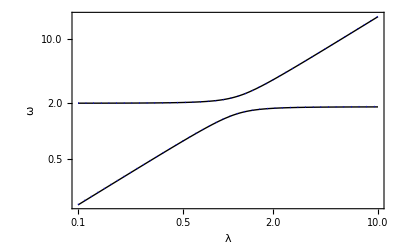

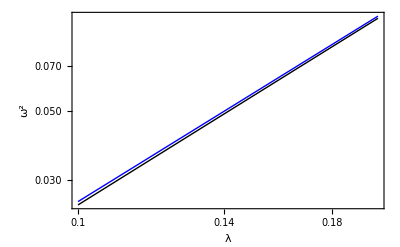

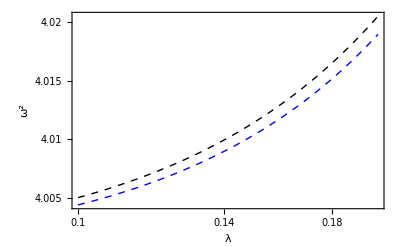

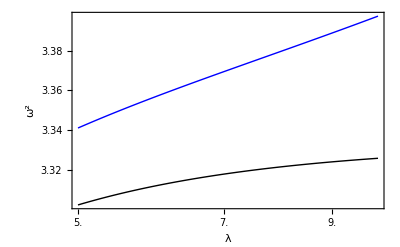

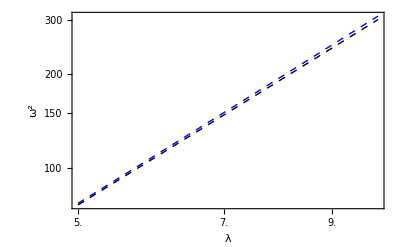

Dropbox/Trabalhos/SingleVortex/shiftG.eps

```mathematica
eqr1=ρ0==(15γ)/(ρ0^3 z0);
eqz1=λ^2 z0==(15γ)/(ρ0^2 z0^2);
a11[ρ1_,z1_,λ_,γ_]:=(45γ)/(ρ1^4 z1)+1;
a12[ρ1_,z1_,λ_,γ_]:=(15 γ)/(ρ1^3 z1^2);
a21[ρ1_,z1_,λ_,γ_]:=(30γ)/(ρ1^3 z1^2);
a22[ρ1_,z1_,λ_,γ_]:=(30γ)/(ρ1^2 z1^3)+λ^2;
ωTF1[ρ1_,z1_,λ_,γ_]:=1/2 (a11[ρ1,z1,λ,γ]+a22[ρ1,z1,λ,γ]-√(a11[ρ1,z1,λ,γ]^2+4 a12[ρ1,z1,λ,γ] a21[ρ1,z1,λ,γ]-2 a11[ρ1,z1,λ,γ] a22[ρ1,z1,λ,γ]+a22[ρ1,z1,λ,γ]^2))
ωTF2[ρ1_,z1_,λ_,γ_]:=1/2 (a11[ρ1,z1,λ,γ]+a22[ρ1,z1,λ,γ]+√(a11[ρ1,z1,λ,γ]^2+4 a12[ρ1,z1,λ,γ] a21[ρ1,z1,λ,γ]-2 a11[ρ1,z1,λ,γ] a22[ρ1,z1,λ,γ]+a22[ρ1,z1,λ,γ]^2))
eqr2=ρ0==1/ρ0^3+γ/(2 √(2π)ρ0^3 z0);
eqz2=λ^2 z0==1/z0^3+γ/(√(2π)ρ0^2 z0^2);
b11[ρ1_,z1_,λ_,γ_]:=(3γ)/(2 √(2π)ρ1^4 z1)+1+3/ρ1^4;
b12[ρ1_,z1_,λ_,γ_]:=γ/(2 √(2π)ρ1^3 z1^2);
b21[ρ1_,z1_,λ_,γ_]:=(2γ)/(√(2π)ρ1^3 z1^2);
b22[ρ1_,z1_,λ_,γ_]:=(2γ)/(√(2π)ρ1^2 z1^3)+3/z1^4+λ^2;
ωG1[ρ1_,z1_,λ_,γ_]:=1/2 (b11[ρ1,z1,λ,γ]+b22[ρ1,z1,λ,γ]-√(b11[ρ1,z1,λ,γ]^2+4 b12[ρ1,z1,λ,γ] b21[ρ1,z1,λ,γ]-2 b11[ρ1,z1,λ,γ] b22[ρ1,z1,λ,γ]+b22[ρ1,z1,λ,γ]^2))
ωG2[ρ1_,z1_,λ_,γ_]:=1/2 (b11[ρ1,z1,λ,γ]+b22[ρ1,z1,λ,γ]+√(b11[ρ1,z1,λ,γ]^2+4 b12[ρ1,z1,λ,γ] b21[ρ1,z1,λ,γ]-2 b11[ρ1,z1,λ,γ]b22[ρ1,z1,λ,γ]+b22[ρ1,z1,λ,γ]^2))
f1=LogLogPlot[{√ωTF1[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],√ωTF2[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],√ωG1[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],√ωG2[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800]},{x,0.1,10},PlotRange->All,Frame->True,Axes->False,FrameLabel->{"λ","ω"},PlotStyle->{Black,Black,Directive[Dotted,Blue],Directive[Dotted,Blue]}]
LogLogPlot[{ωTF1[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],ωG1[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800]},{x,0.1,0.2},PlotRange->All,Frame->True,Axes->False,FrameLabel->{λ,ω^2},PlotStyle->{Black, Blue},PlotLegend->{"QM(TF)","QM(G)"},LegendPosition->{-0.7,-0.2},LegendSize->{0.3,0.76},LegendShadow->{0,0}]
LogLogPlot[{ωTF2[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],ωG2[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800]},{x,0.1,0.2},PlotRange->All,Frame->True,Axes->False,FrameLabel->{"λ","ω^2"},PlotStyle->{ Directive[Dashed,Black], Directive[Dashed,Blue]},PlotLegend->{"BM(TF)","BM(G)"},LegendPosition->{-0.7,-0.2},LegendSize->{0.3,0.76},LegendShadow->{0,0}]
LogLogPlot[{ωTF1[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],ωG1[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800]},{x,5,10},PlotRange->All,Frame->True,Axes->False,FrameLabel->{λ,ω^2},PlotStyle->{Black, Blue},PlotLegend->{"QM(TF)","QM(G)"},LegendPosition->{-0.7,-0.2},LegendSize->{0.3,0.76},LegendShadow->{0,0}]
LogLogPlot[{ωTF2[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],ωG2[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800]},{x,5,10},PlotRange->All,Frame->True,Axes->False,FrameLabel->{λ,ω^2},PlotStyle->{ Directive[Dashed,Black], Directive[Dashed,Blue]},PlotLegend->{"BM(TF)","BM(G)"},LegendPosition->{-0.7,-0.2},LegendSize->{0.3,0.76},LegendShadow->{0,0}]
Export["Dropbox/Trabalhos/SingleVortex/shiftG.eps",f1]
ClearAll[b11,b12,b21,b22,a11,a22,a12,a21,eqr1,eqz1,ωTF1,ωTF2,ωG1,ωG2,eqr2,eqz2,f1]
```

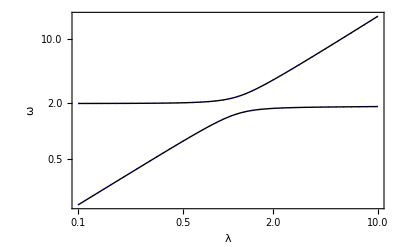

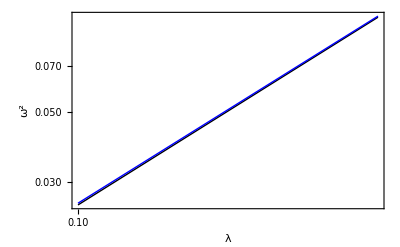

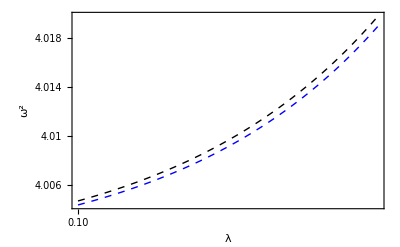

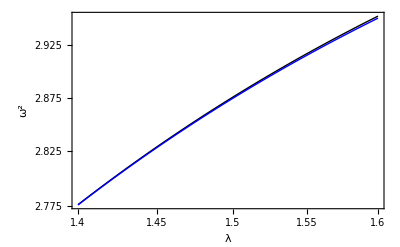

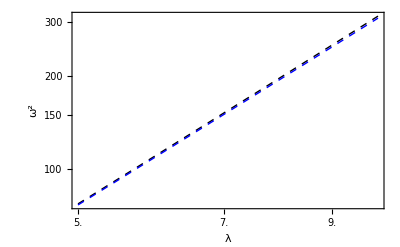

Dropbox/Trabalhos/rz-vortex oscilation/shiftG.eps

```mathematica
eqr1=ρ0==1/ρ0^3+γ/(√(2π)ρ0^3 z0);
eqz1=λ^2 z0==1/z0^3+γ/(√(2π)ρ0^2 z0^2);
a11[ρ1_,z1_,λ_,γ_]:=(3γ)/(√(2π)ρ1^4 z1)+1+3/ρ1^4;
a12[ρ1_,z1_,λ_,γ_]:=γ/(√(2π)ρ1^3 z1^2);
a21[ρ1_,z1_,λ_,γ_]:=(2γ)/(√(2π)ρ1^3 z1^2);
a22[ρ1_,z1_,λ_,γ_]:=(2γ)/(√(2π)ρ1^2 z1^3)+3/z1^4+λ^2;
ωTF1[ρ1_,z1_,λ_,γ_]:=1/2 (a11[ρ1,z1,λ,γ]+a22[ρ1,z1,λ,γ]-√(a11[ρ1,z1,λ,γ]^2+4 a12[ρ1,z1,λ,γ] a21[ρ1,z1,λ,γ]-2 a11[ρ1,z1,λ,γ] a22[ρ1,z1,λ,γ]+a22[ρ1,z1,λ,γ]^2))
ωTF2[ρ1_,z1_,λ_,γ_]:=1/2 (a11[ρ1,z1,λ,γ]+a22[ρ1,z1,λ,γ]+√(a11[ρ1,z1,λ,γ]^2+4 a12[ρ1,z1,λ,γ] a21[ρ1,z1,λ,γ]-2 a11[ρ1,z1,λ,γ] a22[ρ1,z1,λ,γ]+a22[ρ1,z1,λ,γ]^2))
eqr2=ρ0==1/ρ0^3+γ/(2 √(2π)ρ0^3 z0);
eqz2=λ^2 z0==1/z0^3+γ/(√(2π)ρ0^2 z0^2);
b11[ρ1_,z1_,λ_,γ_]:=(3γ)/(2 √(2π)ρ1^4 z1)+1+3/ρ1^4;
b12[ρ1_,z1_,λ_,γ_]:=γ/(2 √(2π)ρ1^3 z1^2);
b21[ρ1_,z1_,λ_,γ_]:=(2γ)/(√(2π)ρ1^3 z1^2);
b22[ρ1_,z1_,λ_,γ_]:=(2γ)/(√(2π)ρ1^2 z1^3)+3/z1^4+λ^2;
ωG1[ρ1_,z1_,λ_,γ_]:=1/2 (b11[ρ1,z1,λ,γ]+b22[ρ1,z1,λ,γ]-√(b11[ρ1,z1,λ,γ]^2+4 b12[ρ1,z1,λ,γ] b21[ρ1,z1,λ,γ]-2 b11[ρ1,z1,λ,γ] b22[ρ1,z1,λ,γ]+b22[ρ1,z1,λ,γ]^2))
ωG2[ρ1_,z1_,λ_,γ_]:=1/2 (b11[ρ1,z1,λ,γ]+b22[ρ1,z1,λ,γ]+√(b11[ρ1,z1,λ,γ]^2+4 b12[ρ1,z1,λ,γ] b21[ρ1,z1,λ,γ]-2 b11[ρ1,z1,λ,γ]b22[ρ1,z1,λ,γ]+b22[ρ1,z1,λ,γ]^2))
f1=LogLogPlot[{√ωTF1[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],√ωTF2[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],√ωG1[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],√ωG2[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800]},{x,0.1,10},PlotRange->All,Frame->True,Axes->False,FrameLabel->{"λ","ω"},PlotStyle->{Black,Black,Directive[Dotted,Blue],Directive[Dotted,Blue]}]
LogLogPlot[{ωTF1[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],ωG1[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800]},{x,0.1,0.2},PlotRange->All,Frame->True,Axes->False,FrameLabel->{λ,ω^2},PlotStyle->{Black, Blue},PlotLegend->{"QM(TF)","QM(G)"},LegendPosition->{-0.7,-0.2},LegendSize->{0.3,0.76},LegendShadow->{0,0}]
LogLogPlot[{ωTF2[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],ωG2[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800]},{x,0.1,0.2},PlotRange->All,Frame->True,Axes->False,FrameLabel->{"λ","ω^2"},PlotStyle->{ Directive[Dashed,Black], Directive[Dashed,Blue]},PlotLegend->{"BM(TF)","BM(G)"},LegendPosition->{-0.7,-0.2},LegendSize->{0.3,0.76},LegendShadow->{0,0}]
LogLogPlot[{ωTF1[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],ωG1[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800]},{x,1.4,1.6},PlotRange->All,Frame->True,Axes->False,FrameLabel->{λ,ω^2},PlotStyle->{Black, Blue},PlotLegend->{"QM(TF)","QM(G)"},LegendPosition->{-0.7,-0.2},LegendSize->{0.3,0.76},LegendShadow->{0,0}]
LogLogPlot[{ωTF2[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],ωG2[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800]},{x,5,10},PlotRange->All,Frame->True,Axes->False,FrameLabel->{λ,ω^2},PlotStyle->{ Directive[Dashed,Black], Directive[Dashed,Blue]},PlotLegend->{"BM(TF)","BM(G)"},LegendPosition->{-0.7,-0.2},LegendSize->{0.3,0.76},LegendShadow->{0,0}]
Export["Dropbox/Trabalhos/rz-vortex oscilation/shiftG.eps",f1]
ClearAll[b11,b12,b21,b22,a11,a22,a12,a21,eqr1,eqz1,ωTF1,ωTF2,ωG1,ωG2,eqr2,eqz2,f1]
```

### Freqüências e Modos (ℓ=2)

```mathematica
Needs["PlotLegends`"]
```

```mathematica
L=2;
d1[α_]:=(-(2 π (2 √(1+α^2) (-4+7 α^2 (4+45 (α^2+α^4)))-210 α^4 (2+5 α^2+3 α^4) ArcCoth[√(1+α^2)]))/(105 √(1+α^2)))/(-(4 π (-√(1+α^2) (6+95 α^2+105 α^4)+15 α^2 (1+α^2) (4+7 α^2) ArcCoth[√(1+α^2)]))/(45 √(1+α^2)))
d2[α_]:=(-(4 π (-30-7 α^2 (107+240 α^2+135 α^4)+105 α^2 (1+α^2)^(3/2) (4+9 α^2) ArcCoth[√(1+α^2)]))/1575)/(-(4 π (-√(1+α^2) (6+95 α^2+105 α^4)+15 α^2 (1+α^2) (4+7 α^2) ArcCoth[√(1+α^2)]))/(45 √(1+α^2)))
d3[α_]:=(-(2 π (-2 √(1+α^2) (16-72 α^2+378 α^4+3675 α^6+3465 α^8)+630 α^6 (1+α^2) (8+11 α^2) ArcCoth[√(1+α^2)]))/(945 √(1+α^2)))/(-(4 π (-√(1+α^2) (6+95 α^2+105 α^4)+15 α^2 (1+α^2) (4+7 α^2) ArcCoth[√(1+α^2)]))/(45 √(1+α^2)))
d4[α_]:=(-(π (√(1+α^2) (-4+8 α^2+15 α^4)-3 α^4 (6+5 α^2) ArcCoth[√(1+α^2)]))/(18 (1+α^2)^(3/2)))/(-(4 π (-√(1+α^2) (6+95 α^2+105 α^4)+15 α^2 (1+α^2) (4+7 α^2) ArcCoth[√(1+α^2)]))/(45 √(1+α^2)))
d5[α_]:=(-(π (4 √(1+α^2) (11+15 α^2)-3 (2+7 α^2+5 α^4) Log[(2+α^2+2 √(1+α^2))/((-1+√(1+α^2))^2)]))/(9 √(1+α^2)))/(-(4 π (-√(1+α^2) (6+95 α^2+105 α^4)+15 α^2 (1+α^2) (4+7 α^2) ArcCoth[√(1+α^2)]))/(45 √(1+α^2)))
d6[α_]:=(-(4 π (√(1+α^2) (-96+352 α^2-1188 α^4+5544 α^6+49665 α^8+45045 α^10)-3465 α^8 (10+23 α^2+13 α^4) ArcTanh[1/(√(1+α^2))]))/(10395 √(1+α^2)))/(-(4 π (-√(1+α^2) (6+95 α^2+105 α^4)+15 α^2 (1+α^2) (4+7 α^2) ArcCoth[√(1+α^2)]))/(45 √(1+α^2)))
d7[α_]:=((2 π (√(1+α^2) (80+4648 α^2+17710 α^4+15015 α^6)-35 α^2 (64+432 α^2+792 α^4+429 α^6) ArcTanh[1/(√(1+α^2))]))/(525 √(1+α^2)))/((-(4 π (-√(1+α^2) (6+95 α^2+105 α^4)+15 α^2 (1+α^2) (4+7 α^2) ArcCoth[√(1+α^2)]))/(45 √(1+α^2)))^2)
F1[α_]:=(d3[α]D[d3[α],α]-2d6[α]D[d1[α],α])/(4(d3[α]^2-d1[α]d6[α]))
F2[α_]:=D[d2[α],α]/(2d2[α])
F3[α_]:=(2d3[α]D[d1[α],α]-d1[α]D[d3[α],α])/(4(d3[α]^2-d1[α]d6[α]))
G1[α_]:=d1[α] F1[α]+d3[α] F3[α]
G2[α_]:=d1[α](F1[α]^2+D[F1[α],α])+d3[α](4F1[α]F3[α]+D[F3[α],α])+3d6[α] F3[α]^2
G3[α_]:=2G1[α]
G4[α_]:=d4[α] L^2+L^2 d5[α]
G5[α_]:=d2[α]F2[α]
G6[α_]:=d2[α](F2[α]^2+D[F2[α],α])
G7[α_]:=2G5[α]
G8[α_]:=D[d1[α],α]F1[α]+1/2 D[d3[α],α]F3[α]
G9[α_]:=D[d2[α],α]F2[α]
G10[α_]:=D[d1[α],α](F1[α]^2+D[F1[α],α])+D[d3[α],α](1/2 D[F3[α],α]+2F1[α]F3[α])+D[d6[α],α] F3[α]^2
G11[α_]:=D[d2[α],α](F2[α]^2+D[F2[α],α])
G12[α_]:=2D[d1[α],α]F1[α]+D[d3[α],α]F3[α]
G13[α_]:=2G9[α]
G14[α_]:=D[d4[α],α] L^2+L^2 D[d5[α],α]

M11[α0_]:=d1[α0]
M12=0;
M13[ρ0_,α0_]:=G1[α0]ρ0
M21=0;
M22[α0_]:=d2[α0]
M23[z0_,α0_]:=G5[α0]z0
M31[ρ0_,α0_]:=D[d1[α0],α0]ρ0
M32[z0_,α0_]:=D[d2[α0],α0]z0
M33[ρ0_,z0_,α0_]:=G8[α0] ρ0^2+G9[α0] z0^2

V11[ρ0_,z0_,α0_]:=d1[α0]+3G4[α0] ρ0^-4+12π γ d7[α0] ρ0^-4 z0^-1
V12[ρ0_,z0_,α0_]:=4π γ d7[α0] ρ0^-3 z0^-2
V13[ρ0_,z0_,α0_]:=D[d1[α0],α0]ρ0-D[G4[α0],α0] ρ0^-3-4π γ D[d7[α0]α0] ρ0^-3 z0^-1
V21[ρ0_,z0_,α0_]:=4π γ d7[α0] ρ0^-3 z0^-2
V22[ρ0_,z0_,α0_]:=d2[α0] λ^2+4π γ d7[α0] ρ0^-2 z0^-3
V23[ρ0_,z0_,α0_]:=D[d2[α0],α0] λ^2 z0-2π γ D[d7[α0],α0] ρ0^-2 z0^-2
V31[ρ0_,z0_,α0_]:=2D[d1[α0],α0]ρ0-2G14[α0] ρ0^-3-8π γ D[d7[α0],α0] ρ0^-3 z0^-1
V32[ρ0_,z0_,α0_]:=2D[d2[α0],α0] λ^2 z0-4π γ D[d7[α0],α0] ρ0^-2 z0^-2
V33[ρ0_,z0_,α0_]:=D[d1[α0],α0,α0] ρ0^2+D[d2[α0],α0,α0] λ^2 z0^2+D[G14[α0],α0] ρ0^-2+4π γ D[d7[α0],α0,α0] ρ0^-2 z0^-1


λ=0.1
γ=800;
eqρ=d1[α0]ρ0==G4[α0]/ρ0^3+(4π γ d7[α0])/(ρ0^3 z0);
eqz=d2[α0] λ^2 z0==(2π γ d7[α0])/(ρ0^2 z0^2);
eqα=D[d1[α0],α0] ρ0^2+D[d2[α0],α0] λ^2 z0^2+G14[α0]/ρ0^2+(4π γ D[d7[α0],α0])/(ρ0^2 z0)==0;
ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}]

ρ0=Evaluate[ρ0/.ss];
z0=Evaluate[z0/.ss];
a=Evaluate[α0/.ss];

Det[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a

Det[({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})]/.α->a
MatrixForm[{{val1,val2,val3},{{r1,z1,α1},{r2,z2,α2},{r3,z3,α3}}}=Eigensystem[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)]]
Print[MatrixForm[{{"val1"},{"δρ1","δz1","δξ1"}} ]]
MatrixForm[{{val1},{r1,z1,ρ0 α1+a r1}}]
Print[MatrixForm[{{"val2"},{"δρ2","δz2","δξ2"}} ]]
MatrixForm[{{val2},{r2,z2,ρ0 α2+a r2}}]
Print[MatrixForm[{{"val3"},{"δρ3","δz3","δξ3"}} ]]
MatrixForm[{{val3},{r3,z3,ρ0 α3+a r3}}]
ClearAll[r1,r2,r3,z1,z2,z3,val1,val2,val3,α1,α2,α3]
Det[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)-ω^2({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})]==0
Solve[Det[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)-ω^2({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})]==0,ω]

ClearAll[λ,γ,ss,a,z0,ρ0,eqρ,eqz,eqα]

λ=1
γ=800;

eqρ=d1[α0]ρ0==G4[α0]/ρ0^3+(4π γ d7[α0])/(ρ0^3 z0);
eqz=d2[α0] λ^2 z0==(2π γ d7[α0])/(ρ0^2 z0^2);
eqα=D[d1[α0],α0] ρ0^2+D[d2[α0],α0] λ^2 z0^2+G14[α0]/ρ0^2+(4π γ D[d7[α0],α0])/(ρ0^2 z0)==0;
ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}]

ρ0=Evaluate[ρ0/.ss];
z0=Evaluate[z0/.ss];
a=Evaluate[α0/.ss];

Det[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a

Det[({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})]/.α->a
MatrixForm[{{val1,val2,val3},{{r1,z1,α1},{r2,z2,α2},{r3,z3,α3}}}=Eigensystem[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)]]
Print[MatrixForm[{{"val1"},{"δρ1","δz1","δξ1"}} ]]
MatrixForm[{{val1},{r1,z1,ρ0 α1+a r1}}]
Print[MatrixForm[{{"val2"},{"δρ2","δz2","δξ2"}} ]]
MatrixForm[{{val2},{r2,z2,ρ0 α2+a r2}}]
Print[MatrixForm[{{"val3"},{"δρ3","δz3","δξ3"}} ]]
MatrixForm[{{val3},{r3,z3,ρ0 α3+a r3}}]
ClearAll[r1,r2,r3,z1,z2,z3,val1,val2,val3,α1,α2,α3]
Det[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)-ω^2({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})]==0
Solve[Det[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)-ω^2({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})]==0,ω]

ClearAll[ss,eqρ,eqz,eqα,ρ0,z0,a,λ,γ]

λ=10
γ=800;

eqρ=d1[α0]ρ0==G4[α0]/ρ0^3+(4π γ d7[α0])/(ρ0^3 z0);
eqz=d2[α0] λ^2 z0==(2π γ d7[α0])/(ρ0^2 z0^2);
eqα=D[d1[α0],α0] ρ0^2+D[d2[α0],α0] λ^2 z0^2+G14[α0]/ρ0^2+(4π γ D[d7[α0],α0])/(ρ0^2 z0)==0;
ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}]

ρ0=Evaluate[ρ0/.ss];
z0=Evaluate[z0/.ss];
a=Evaluate[α0/.ss];

Det[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a

Det[({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})]/.α->a

MatrixForm[{{val1,val2,val3},{{r1,z1,α1},{r2,z2,α2},{r3,z3,α3}}}=Eigensystem[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)]]
Print[MatrixForm[{{"val1"},{"δρ1","δz1","δξ1"}} ]]
MatrixForm[{{val1},{r1,z1,ρ0 α1+a r1}}]
Print[MatrixForm[{{"val2"},{"δρ2","δz2","δξ2"}} ]]
MatrixForm[{{val2},{r2,z2,ρ0 α2+a r2}}]
Print[MatrixForm[{{"val3"},{"δρ3","δz3","δξ3"}} ]]
MatrixForm[{{val3},{r3,z3,ρ0*α3+a*r3}}]
ClearAll[r1,r2,r3,z1,z2,z3,val1,val2,val3,α1,α2,α3]
Det[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)-ω^2({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})]==0
Solve[Det[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)-ω^2({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})]==0,ω]


ClearAll[d1,d2,a,d3,d4,d5,d6,F1,F2,F3,G1,G4,G5,G8,G9,G14,ss,eqρ,eqz,eqα,λ,γ,α0,ρ0,z0,M11,M12,M12,M13,M21,M22,M23,M31,M32,M33,V11,V12,V13,V21,V22,V23,V31,V32,V33,G2,G3,G6,G7,G10,G11,G12,G13,d7,L]
```

0.1

{ρ0→4.28303,z0→40.6747,α0→0.129432}

0.0885706

0.247048

(27.0389 | 4.00372 | 0.0257656
{-0.215532,0.972514,0.0881095} | {0.998812,0.0487264,0.0000889103} | {0.0230426,-0.999733,-0.00156019})

({val1}
{δρ1,δz1,δξ1})

({27.0389}
{-0.215532,0.972514,0.349479})

({val2}
{δρ2,δz2,δξ2})

({4.00372}
{0.998812,0.0487264,0.129659})

({val3}
{δρ3,δz3,δξ3})

({0.0257656}
{0.0230426,-0.999733,-0.00369992})

2.78928-109.056 ω^2+31.0684 ω^4-ω^6==0

{{ω→-5.19989},{ω→-2.00093},{ω→-0.160517},{ω→0.160517},{ω→2.00093},{ω→5.19989}}

1

{ρ0→6.59102,z0→6.5162,α0→0.0504205}

0.220303

108.263

(48.6422 | 4.93858 | 2.0457
{-0.901911,0.350753,0.252048} | {0.695004,0.718999,0.00315533} | {-0.437614,0.899155,0.00370237})

({val1}
{δρ1,δz1,δξ1})

({48.6422}
{-0.901911,0.350753,1.61578})

({val2}
{δρ2,δz2,δξ2})

({4.93858}
{0.695004,0.718999,0.0558393})

({val3}
{δρ3,δz3,δξ3})

({2.0457}
{-0.437614,0.899155,0.00233766})

491.426-349.834 ω^2+55.6264 ω^4-ω^6==0

{{ω→-6.97439},{ω→-2.22229},{ω→-1.43028},{ω→1.43028},{ω→2.22229},{ω→6.97439}}

10

{ρ0→10.3849,z0→1.036,α0→0.0195762}

0.293267

35574.6

(300.85 | 120.751 | 3.33914
{0.0579194,0.998301,-0.00642721} | {-0.964896,0.0798097,0.250213} | {-0.997746,0.0671004,0.000659218})

({val1}
{δρ1,δz1,δξ1})

({300.85}
{0.0579194,0.998301,-0.0656117})

({val2}
{δρ2,δz2,δξ2})

({120.751}
{-0.964896,0.0798097,2.57954})

({val3}
{δρ3,δz3,δξ3})

({3.33914}
{-0.997746,0.0671004,-0.0126862})

121305.-37735.9 ω^2+424.941 ω^4-ω^6==0

{{ω→-17.345},{ω→-10.9887},{ω→-1.82733},{ω→1.82733},{ω→10.9887},{ω→17.345}}

#### Solução da equação cúbica

```mathematica
a=-1;
b=76.1104445769892;
c=-664.4846878320106;
d=236.43718061500593;
p=c/a-b^2/(3 a^2);
q=(2 b^3)/(27 a^3)-(b c)/(3 a^2)+d/a;
t1=(-q/2+1/2 √(q^2+4 p^3/27))^(1/3)+(-q/2-1/2 √(q^2+4 p^3/27))^(1/3);
t2=-t1/2+√(t1^2/4+q/t1);
t3=-t1/2-√(t1^2/4+q/t1);
x1=t1-b/(3a)
x2=t2-b/(3a)
x3=t3-b/(3a)
ClearAll[a,b,c,d,q,p,t1,t2,t3,x1,x2,x3]

a=-1;
b=105.40530583944545;
c=-1163.0888844234873;
d=2707.123177696637;
p=c/a-b^2/(3 a^2);
q=(2 b^3)/(27 a^3)-(b c)/(3 a^2)+d/a;
t1=(-q/2+1/2 √(q^2+4 p^3/27))^(1/3)+(-q/2-1/2 √(q^2+4 p^3/27))^(1/3);
t2=-t1/2+√(t1^2/4+q/t1);
t3=-t1/2-√(t1^2/4+q/t1);
x1=t1-b/(3a)
x2=t2-b/(3a)
x3=t3-b/(3a)
ClearAll[a,b,c,d,q,p,t1,t2,t3,x1,x2,x3]

a=-1;
b=546.310502516647;
c=-75889.08447359763;
d=603739.6510152337;
p=c/a-b^2/(3 a^2);
q=(2 b^3)/(27 a^3)-(b c)/(3 a^2)+d/a;
t1=(-q/2+1/2 √(q^2+4 p^3/27))^(1/3)+(-q/2-1/2 √(q^2+4 p^3/27))^(1/3);
t2=-t1/2+√(t1^2/4+q/t1);
t3=-t1/2-√(t1^2/4+q/t1);
x1=t1-b/(3a)
x2=t2-b/(3a)
x3=t3-b/(3a)
ClearAll[a,b,c,d,q,p,t1,t2,t3,x1,x2,x3]
```

66.1139+0. ⅈ

9.62495+0. ⅈ

0.371556+0. ⅈ

93.2429+0. ⅈ

8.90038+0. ⅈ

3.262+0. ⅈ

300.273+0. ⅈ

237.575+0. ⅈ

8.46318+0. ⅈ

#### Cross Check (Gaussiana com vórtice e TF sem vórtice)

```mathematica
γ=800;
λ=0.1;
eqr2=ρ0==(15γ)/(ρ0^3 z0);
eqz2=λ^2 z0==(15γ)/(ρ0^2 z0^2);
ss2=FindRoot[{eqr2,eqz2},{ρ0,0.01},{z0,0.01}]
ρ1=Evaluate[ρ0/.ss2];
z1=Evaluate[z0/.ss2];
b11=(45γ)/(ρ1^4 z1)+1;
b12=(15 γ)/(ρ1^3 z1^2);
b21=(30γ)/(ρ1^3 z1^2);
b22=(30γ)/(ρ1^2 z1^3)+λ^2;
MatrixForm[Eigensystem[({{b11, b12}, {b21, b22}})]]
Solve[Det[({{b11, b12}, {b21, b22}})-ω^2({{1, 0}, {0, 1}})]==0,ω]
ClearAll[b11,b12,b21,b22,z1,ρ1,ss2,eqr2,eqz2,γ,λ]
γ=800;
λ=1;
eqr2=ρ0==(15γ)/(ρ0^3 z0);
eqz2=λ^2 z0==(15γ)/(ρ0^2 z0^2);
ss2=FindRoot[{eqr2,eqz2},{ρ0,0.01},{z0,0.01}]
ρ1=Evaluate[ρ0/.ss2];
z1=Evaluate[z0/.ss2];
b11=(45γ)/(ρ1^4 z1)+1;
b12=(15 γ)/(ρ1^3 z1^2);
b21=(30γ)/(ρ1^3 z1^2);
b22=(30γ)/(ρ1^2 z1^3)+λ^2;
MatrixForm[Eigensystem[({{b11, b12}, {b21, b22}})]]
Solve[Det[({{b11, b12}, {b21, b22}})-ω^2({{1, 0}, {0, 1}})]==0,ω]
ClearAll[b11,b12,b21,b22,z1,ρ1,ss2,eqr2,eqz2,γ,λ]
γ=800;
λ=10;
eqr2=ρ0==(15γ)/(ρ0^3 z0);
eqz2=λ^2 z0==(15γ)/(ρ0^2 z0^2);
ss2=FindRoot[{eqr2,eqz2},{ρ0,0.01},{z0,0.01}]
ρ1=Evaluate[ρ0/.ss2];
z1=Evaluate[z0/.ss2];
b11=(45γ)/(ρ1^4 z1)+1;
b12=(15 γ)/(ρ1^3 z1^2);
b21=(30γ)/(ρ1^3 z1^2);
b22=(30γ)/(ρ1^2 z1^3)+λ^2;
MatrixForm[Eigensystem[({{b11, b12}, {b21, b22}})]]
Solve[Det[({{b11, b12}, {b21, b22}})-ω^2({{1, 0}, {0, 1}})]==0,ω]
ClearAll[b11,b12,b21,b22,z1,ρ1,ss2,eqr2,eqz2,γ,λ]
```

{ρ0→4.12892,z0→41.2892}

(4.00503 | 0.0249686
{0.998737,0.0502505} | {-0.0251491,0.999684})

{{ω→-2.00126},{ω→-0.158015},{ω→0.158015},{ω→2.00126}}

{ρ0→6.54389,z0→6.54389}

(5. | 2.
{0.707107,0.707107} | {-0.447214,0.894427})

{{ω→-2.23607},{ω→-1.41421},{ω→1.41421},{ω→2.23607}}

{ρ0→10.3714,z0→1.03714}

(300.674 | 3.32586
{-0.0336879,-0.999432} | {-0.997735,0.0672614})

{{ω→-17.34},{ω→-1.82369},{ω→1.82369},{ω→17.34}}

```mathematica
γ=800;
λ=0.1;
eqr2=ρ0==1/ρ0^3+γ/(2 √(2π)ρ0^3 z0);
eqz2=λ^2 z0==1/z0^3+γ/(√(2π)ρ0^2 z0^2);
ss2=FindRoot[{eqr2,eqz2},{ρ0,0.01},{z0,0.01}]
ρ1=Evaluate[ρ0/.ss2];
z1=Evaluate[z0/.ss2];
b11=(3γ)/(2 √(2π)ρ1^4 z1)+1+3/ρ1^4;
b12=γ/(2 √(2π)ρ1^3 z1^2);
b21=(2γ)/(√(2π)ρ1^3 z1^2);
b22=(2γ)/(√(2π)ρ1^2 z1^3)+3/z1^4+λ^2;
MatrixForm[Eigensystem[({{b11, b12}, {b21, b22}})]]
Solve[Det[({{b11, b12}, {b21, b22}})-ω^2({{1, 0}, {0, 1}})]==0,ω]
ClearAll[b11,b12,b21,b22,z1,ρ1,ss2,eqr2,eqz2,γ,λ]
γ=800;
λ=1;
eqr2=ρ0==1/ρ0^3+γ/(2 √(2π)ρ0^3 z0);
eqz2=λ^2 z0==1/z0^3+γ/(√(2π)ρ0^2 z0^2);
ss2=FindRoot[{eqr2,eqz2},{ρ0,0.01},{z0,0.01}]
ρ1=Evaluate[ρ0/.ss2];
z1=Evaluate[z0/.ss2];
b11=(3γ)/(2 √(2π)ρ1^4 z1)+1+3/ρ1^4;
b12=γ/(2 √(2π)ρ1^3 z1^2);
b21=(2γ)/(√(2π)ρ1^3 z1^2);
b22=(2γ)/(√(2π)ρ1^2 z1^3)+3/z1^4+λ^2;
MatrixForm[Eigensystem[({{b11, b12}, {b21, b22}})]]
Solve[Det[({{b11, b12}, {b21, b22}})-ω^2({{1, 0}, {0, 1}})]==0,ω]
ClearAll[b11,b12,b21,b22,z1,ρ1,ss2,eqr2,eqz2,γ,λ]
γ=800;
λ=10;
eqr2=ρ0==1/ρ0^3+γ/(2 √(2π)ρ0^3 z0);
eqz2=λ^2 z0==1/z0^3+γ/(√(2π)ρ0^2 z0^2);
ss2=FindRoot[{eqr2,eqz2},{ρ0,0.01},{z0,0.01}]
ρ1=Evaluate[ρ0/.ss2];
z1=Evaluate[z0/.ss2];
b11=(3γ)/(2 √(2π)ρ1^4 z1)+1+3/ρ1^4;
b12=γ/(2 √(2π)ρ1^3 z1^2);
b21=(2γ)/(√(2π)ρ1^3 z1^2);
b22=(2γ)/(√(2π)ρ1^2 z1^3)+3/z1^4+λ^2;
MatrixForm[Eigensystem[({{b11, b12}, {b21, b22}})]]
Solve[Det[({{b11, b12}, {b21, b22}})-ω^2({{1, 0}, {0, 1}})]==0,ω]
ClearAll[b11,b12,b21,b22,z1,ρ1,ss2,eqr2,eqz2,γ,λ]
```

{ρ0→1.68875,z0→22.3707}

(4.00441 | 0.0255923
{0.997787,0.0664868} | {-0.0166563,0.999861})

{{ω→-2.0011},{ω→-0.159976},{ω→0.159976},{ω→2.0011}}

{ρ0→2.58924,z0→3.63123}

(4.98321 | 2.02254
{0.578428,0.815734} | {-0.332505,0.943102})

{{ω→-2.23231},{ω→-1.42216},{ω→1.42216},{ω→2.23231}}

{ρ0→4.04934,z0→0.595735}

(308.542 | 3.39766
{-0.022231,-0.999753} | {-0.996068,0.0885961})

{{ω→-17.5654},{ω→-1.84328},{ω→1.84328},{ω→17.5654}}

```mathematica
Needs["PlotLegends`"]
```

```mathematica
eqr1=ρ0==(15γ)/(ρ0^3 z0);
eqz1=λ^2 z0==(15γ)/(ρ0^2 z0^2);
a11[ρ1_,z1_,λ_,γ_]:=(45γ)/(ρ1^4 z1)+1;
a12[ρ1_,z1_,λ_,γ_]:=(15 γ)/(ρ1^3 z1^2);
a21[ρ1_,z1_,λ_,γ_]:=(30γ)/(ρ1^3 z1^2);
a22[ρ1_,z1_,λ_,γ_]:=(30γ)/(ρ1^2 z1^3)+λ^2;
ωTF1[ρ1_,z1_,λ_,γ_]:=1/2 (a11[ρ1,z1,λ,γ]+a22[ρ1,z1,λ,γ]-√(a11[ρ1,z1,λ,γ]^2+4 a12[ρ1,z1,λ,γ] a21[ρ1,z1,λ,γ]-2 a11[ρ1,z1,λ,γ] a22[ρ1,z1,λ,γ]+a22[ρ1,z1,λ,γ]^2))
ωTF2[ρ1_,z1_,λ_,γ_]:=1/2 (a11[ρ1,z1,λ,γ]+a22[ρ1,z1,λ,γ]+√(a11[ρ1,z1,λ,γ]^2+4 a12[ρ1,z1,λ,γ] a21[ρ1,z1,λ,γ]-2 a11[ρ1,z1,λ,γ] a22[ρ1,z1,λ,γ]+a22[ρ1,z1,λ,γ]^2))
eqr2=ρ0==1/ρ0^3+γ/(2 √(2π)ρ0^3 z0);
eqz2=λ^2 z0==1/z0^3+γ/(√(2π)ρ0^2 z0^2);
b11[ρ1_,z1_,λ_,γ_]:=(3γ)/(2 √(2π)ρ1^4 z1)+1+3/ρ1^4;
b12[ρ1_,z1_,λ_,γ_]:=γ/(2 √(2π)ρ1^3 z1^2);
b21[ρ1_,z1_,λ_,γ_]:=(2γ)/(√(2π)ρ1^3 z1^2);
b22[ρ1_,z1_,λ_,γ_]:=(2γ)/(√(2π)ρ1^2 z1^3)+3/z1^4+λ^2;
ωG1[ρ1_,z1_,λ_,γ_]:=1/2 (b11[ρ1,z1,λ,γ]+b22[ρ1,z1,λ,γ]-√(b11[ρ1,z1,λ,γ]^2+4 b12[ρ1,z1,λ,γ] b21[ρ1,z1,λ,γ]-2 b11[ρ1,z1,λ,γ] b22[ρ1,z1,λ,γ]+b22[ρ1,z1,λ,γ]^2))
ωG2[ρ1_,z1_,λ_,γ_]:=1/2 (b11[ρ1,z1,λ,γ]+b22[ρ1,z1,λ,γ]+√(b11[ρ1,z1,λ,γ]^2+4 b12[ρ1,z1,λ,γ] b21[ρ1,z1,λ,γ]-2 b11[ρ1,z1,λ,γ]b22[ρ1,z1,λ,γ]+b22[ρ1,z1,λ,γ]^2))
f1=LogLogPlot[{√ωTF1[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],√ωTF2[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],√ωG1[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],√ωG2[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800]},{x,0.1,10},PlotRange->All,Frame->True,Axes->False,FrameLabel->{"λ","ω"},PlotStyle->{Black,Black,Directive[Dotted,Blue],Directive[Dotted,Blue]}]
LogLogPlot[{ωTF1[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],ωG1[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800]},{x,0.1,0.2},PlotRange->All,Frame->True,Axes->False,FrameLabel->{λ,ω^2},PlotStyle->{Black, Blue},PlotLegend->{"QM(TF)","QM(G)"},LegendPosition->{-0.7,-0.2},LegendSize->{0.3,0.76},LegendShadow->{0,0}]
LogLogPlot[{ωTF2[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],ωG2[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800]},{x,0.1,0.2},PlotRange->All,Frame->True,Axes->False,FrameLabel->{"λ","ω^2"},PlotStyle->{ Directive[Dashed,Black], Directive[Dashed,Blue]},PlotLegend->{"BM(TF)","BM(G)"},LegendPosition->{-0.7,-0.2},LegendSize->{0.3,0.76},LegendShadow->{0,0}]
LogLogPlot[{ωTF1[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],ωG1[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800]},{x,5,10},PlotRange->All,Frame->True,Axes->False,FrameLabel->{λ,ω^2},PlotStyle->{Black, Blue},PlotLegend->{"QM(TF)","QM(G)"},LegendPosition->{-0.7,-0.2},LegendSize->{0.3,0.76},LegendShadow->{0,0}]
LogLogPlot[{ωTF2[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],ωG2[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800]},{x,5,10},PlotRange->All,Frame->True,Axes->False,FrameLabel->{λ,ω^2},PlotStyle->{ Directive[Dashed,Black], Directive[Dashed,Blue]},PlotLegend->{"BM(TF)","BM(G)"},LegendPosition->{-0.7,-0.2},LegendSize->{0.3,0.76},LegendShadow->{0,0}]
Export["Dropbox/Trabalhos/SingleVortex/shiftG.eps",f1]
ClearAll[b11,b12,b21,b22,a11,a22,a12,a21,eqr1,eqz1,ωTF1,ωTF2,ωG1,ωG2,eqr2,eqz2,f1]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

Dropbox/Trabalhos/SingleVortex/shiftG.eps

### Freqüências e Modos (ℓ=3)

```mathematica
Needs["PlotLegends`"]
```

```mathematica
L=3;
d1[α_]:=((π (-√(1+α^2) (-16+168 α^2+2730 α^4+3465 α^6)+105 α^4 (16+48 α^2+33 α^4) ArcTanh[1/(√(1+α^2))]))/(105 √(1+α^2)))/(-(π (-√(1+α^2) (8+210 α^2+315 α^4)+15 α^2 (8+28 α^2+21 α^4) ArcCoth[√(1+α^2)]))/(15 √(1+α^2)))
d2[α_]:=((π (√(-1-α^2) (40+1638 α^2+4935 α^4+3465 α^6)+105 α^2 (8+44 α^2+69 α^4+33 α^6) ArcTan[1/(√(-1-α^2))]))/(525 √(-1-α^2)))/(-(π (-√(1+α^2) (8+210 α^2+315 α^4)+15 α^2 (8+28 α^2+21 α^4) ArcCoth[√(1+α^2)]))/(15 √(1+α^2)))
d3[α_]:=((π (√(1+α^2) (64-432 α^2+3024 α^4+39270 α^6+45045 α^8)-315 α^6 (80+220 α^2+143 α^4) ArcTanh[1/(√(1+α^2))]))/(945 √(1+α^2)))/(-(π (-√(1+α^2) (8+210 α^2+315 α^4)+15 α^2 (8+28 α^2+21 α^4) ArcCoth[√(1+α^2)]))/(15 √(1+α^2)))
d4[α_]:=(-(π (2 √(1+α^2) (-16+40 α^2+170 α^4+105 α^6)-6 α^4 (48+80 α^2+35 α^4) ArcTanh[1/(√(1+α^2))]))/(288 (1+α^2)^(5/2)))/(-(π (-√(1+α^2) (8+210 α^2+315 α^4)+15 α^2 (8+28 α^2+21 α^4) ArcCoth[√(1+α^2)]))/(15 √(1+α^2)))
d5[α_]:=((π (-40 √(1+α^2) (10+21 α^2)-6 (8+40 α^2+35 α^4) Log[(-1+√(1+α^2))/(1+√(1+α^2))]+6 (8+40 α^2+35 α^4) Log[(1+√(1+α^2))/(-1+√(1+α^2))]))/(72 √(1+α^2)))/(-(π (-√(1+α^2) (8+210 α^2+315 α^4)+15 α^2 (8+28 α^2+21 α^4) ArcCoth[√(1+α^2)]))/(15 √(1+α^2)))
d6[α_]:=((π (-√(1+α^2) (-128+704 α^2-3168 α^4+18480 α^6+210210 α^8+225225 α^10)+3465 α^8 (40+104 α^2+65 α^4) ArcTanh[1/(√(1+α^2))]))/(3465 √(1+α^2)))/(-(π (-√(1+α^2) (8+210 α^2+315 α^4)+15 α^2 (8+28 α^2+21 α^4) ArcCoth[√(1+α^2)]))/(15 √(1+α^2)))
d7[α_]:=1/((-(π (-√(1+α^2) (8+210 α^2+315 α^4)+15 α^2 (8+28 α^2+21 α^4) ArcCoth[√(1+α^2)]))/(15 √(1+α^2)))^2)(1/(4200 (1+α^2)^(5/2))π (√(1+α^2) (1280+123968 α^2+906576 α^4+2210208 α^6+2192190 α^8+765765 α^10)-105 α^2 (512+5760 α^2+21120 α^4+34320 α^6+25740 α^8+7293 α^10) ArcTanh[1/(√(1+α^2))]))
F1[α_]:=(d3[α]D[d3[α],α]-2d6[α]D[d1[α],α])/(4(d3[α]^2-d1[α]d6[α]))
F2[α_]:=D[d2[α],α]/(2d2[α])
F3[α_]:=(2d3[α]D[d1[α],α]-d1[α]D[d3[α],α])/(4(d3[α]^2-d1[α]d6[α]))
G1[α_]:=d1[α] F1[α]+d3[α] F3[α]
G2[α_]:=d1[α](F1[α]^2+D[F1[α],α])+d3[α](4F1[α]F3[α]+D[F3[α],α])+3d6[α] F3[α]^2
G3[α_]:=2G1[α]
G4[α_]:=d4[α] L^2+L^2 d5[α]
G5[α_]:=d2[α]F2[α]
G6[α_]:=d2[α](F2[α]^2+D[F2[α],α])
G7[α_]:=2G5[α]
G8[α_]:=D[d1[α],α]F1[α]+1/2 D[d3[α],α]F3[α]
G9[α_]:=D[d2[α],α]F2[α]
G10[α_]:=D[d1[α],α](F1[α]^2+D[F1[α],α])+D[d3[α],α](1/2 D[F3[α],α]+2F1[α]F3[α])+D[d6[α],α] F3[α]^2
G11[α_]:=D[d2[α],α](F2[α]^2+D[F2[α],α])
G12[α_]:=2D[d1[α],α]F1[α]+D[d3[α],α]F3[α]
G13[α_]:=2G9[α]
G14[α_]:=D[d4[α],α] L^2+L^2 D[d5[α],α]

M11[α0_]:=d1[α0]
M12=0;
M13[ρ0_,α0_]:=G1[α0]ρ0
M21=0;
M22[α0_]:=d2[α0]
M23[z0_,α0_]:=G5[α0]z0
M31[ρ0_,α0_]:=D[d1[α0],α0]ρ0
M32[z0_,α0_]:=D[d2[α0],α0]z0
M33[ρ0_,z0_,α0_]:=G8[α0] ρ0^2+G9[α0] z0^2

V11[ρ0_,z0_,α0_]:=d1[α0]+3G4[α0] ρ0^-4+12π γ d7[α0] ρ0^-4 z0^-1
V12[ρ0_,z0_,α0_]:=4π γ d7[α0] ρ0^-3 z0^-2
V13[ρ0_,z0_,α0_]:=D[d1[α0],α0]ρ0-D[G4[α0],α0] ρ0^-3-4π γ D[d7[α0]α0] ρ0^-3 z0^-1
V21[ρ0_,z0_,α0_]:=4π γ d7[α0] ρ0^-3 z0^-2
V22[ρ0_,z0_,α0_]:=d2[α0] λ^2+4π γ d7[α0] ρ0^-2 z0^-3
V23[ρ0_,z0_,α0_]:=D[d2[α0],α0] λ^2 z0-2π γ D[d7[α0],α0] ρ0^-2 z0^-2
V31[ρ0_,z0_,α0_]:=2D[d1[α0],α0]ρ0-2G14[α0] ρ0^-3-8π γ D[d7[α0],α0] ρ0^-3 z0^-1
V32[ρ0_,z0_,α0_]:=2D[d2[α0],α0] λ^2 z0-4π γ D[d7[α0],α0] ρ0^-2 z0^-2
V33[ρ0_,z0_,α0_]:=D[d1[α0],α0,α0] ρ0^2+D[d2[α0],α0,α0] λ^2 z0^2+D[G14[α0],α0] ρ0^-2+4π γ D[d7[α0],α0,α0] ρ0^-2 z0^-1


λ=0.1
γ=800;
eqρ=d1[α0]ρ0==G4[α0]/ρ0^3+(4π γ d7[α0])/(ρ0^3 z0);
eqz=d2[α0] λ^2 z0==(2π γ d7[α0])/(ρ0^2 z0^2);
eqα=D[d1[α0],α0] ρ0^2+D[d2[α0],α0] λ^2 z0^2+G14[α0]/ρ0^2+(4π γ D[d7[α0],α0])/(ρ0^2 z0)==0;
ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}]

ρ0=Evaluate[ρ0/.ss];
z0=Evaluate[z0/.ss];
a=Evaluate[α0/.ss];

Det[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a

Det[({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})]/.α->a
MatrixForm[{{val1,val2,val3},{{r1,z1,α1},{r2,z2,α2},{r3,z3,α3}}}=Eigensystem[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)]]
Print[MatrixForm[{{"val1"},{"δρ1","δz1","δξ1"}} ]]
MatrixForm[{{val1},{r1,z1,ρ0 α1+a r1}}]
Print[MatrixForm[{{"val2"},{"δρ2","δz2","δξ2"}} ]]
MatrixForm[{{val2},{r2,z2,ρ0 α2+a r2}}]
Print[MatrixForm[{{"val3"},{"δρ3","δz3","δξ3"}} ]]
MatrixForm[{{val3},{r3,z3,ρ0 α3+a r3}}]
ClearAll[r1,r2,r3,z1,z2,z3,val1,val2,val3,α1,α2,α3]
Det[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)-ω^2({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})]==0
Solve[Det[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)-ω^2({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})]==0,ω]

ClearAll[λ,γ,ss,a,z0,ρ0,eqρ,eqz,eqα]

λ=1
γ=800;

eqρ=d1[α0]ρ0==G4[α0]/ρ0^3+(4π γ d7[α0])/(ρ0^3 z0);
eqz=d2[α0] λ^2 z0==(2π γ d7[α0])/(ρ0^2 z0^2);
eqα=D[d1[α0],α0] ρ0^2+D[d2[α0],α0] λ^2 z0^2+G14[α0]/ρ0^2+(4π γ D[d7[α0],α0])/(ρ0^2 z0)==0;
ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}]

ρ0=Evaluate[ρ0/.ss];
z0=Evaluate[z0/.ss];
a=Evaluate[α0/.ss];

Det[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a

Det[({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})]/.α->a
MatrixForm[{{val1,val2,val3},{{r1,z1,α1},{r2,z2,α2},{r3,z3,α3}}}=Eigensystem[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)]]
Print[MatrixForm[{{"val1"},{"δρ1","δz1","δξ1"}} ]]
MatrixForm[{{val1},{r1,z1,ρ0 α1+a r1}}]
Print[MatrixForm[{{"val2"},{"δρ2","δz2","δξ2"}} ]]
MatrixForm[{{val2},{r2,z2,ρ0 α2+a r2}}]
Print[MatrixForm[{{"val3"},{"δρ3","δz3","δξ3"}} ]]
MatrixForm[{{val3},{r3,z3,ρ0 α3+a r3}}]
ClearAll[r1,r2,r3,z1,z2,z3,val1,val2,val3,α1,α2,α3]
Det[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)-ω^2({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})]==0
Solve[Det[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)-ω^2({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})]==0,ω]

ClearAll[ss,eqρ,eqz,eqα,ρ0,z0,a,λ,γ]

λ=10
γ=800;

eqρ=d1[α0]ρ0==G4[α0]/ρ0^3+(4π γ d7[α0])/(ρ0^3 z0);
eqz=d2[α0] λ^2 z0==(2π γ d7[α0])/(ρ0^2 z0^2);
eqα=D[d1[α0],α0] ρ0^2+D[d2[α0],α0] λ^2 z0^2+G14[α0]/ρ0^2+(4π γ D[d7[α0],α0])/(ρ0^2 z0)==0;
ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}]

ρ0=Evaluate[ρ0/.ss];
z0=Evaluate[z0/.ss];
a=Evaluate[α0/.ss];

Det[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a

Det[({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})]/.α->a

MatrixForm[{{val1,val2,val3},{{r1,z1,α1},{r2,z2,α2},{r3,z3,α3}}}=Eigensystem[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)]]
Print[MatrixForm[{{"val1"},{"δρ1","δz1","δξ1"}} ]]
MatrixForm[{{val1},{r1,z1,ρ0 α1+a r1}}]
Print[MatrixForm[{{"val2"},{"δρ2","δz2","δξ2"}} ]]
MatrixForm[{{val2},{r2,z2,ρ0 α2+a r2}}]
Print[MatrixForm[{{"val3"},{"δρ3","δz3","δξ3"}} ]]
MatrixForm[{{val3},{r3,z3,ρ0 α3+a r3}}]
ClearAll[r1,r2,r3,z1,z2,z3,val1,val2,val3,α1,α2,α3]
Det[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)-ω^2({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})]==0
Solve[Det[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)-ω^2({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})]==0,ω]


ClearAll[d1,d2,a,d3,d4,d5,d6,F1,F2,F3,G1,G4,G5,G8,G9,G14,ss,eqρ,eqz,eqα,λ,γ,α0,ρ0,z0,M11,M12,M12,M13,M21,M22,M23,M31,M32,M33,V11,V12,V13,V21,V22,V23,V31,V32,V33,G2,G3,G6,G7,G10,G11,G12,G13,d7,L]
```

0.1

{ρ0→4.39744+0. ⅈ,z0→40.5146+0. ⅈ,α0→0.151935+0. ⅈ}

0.128902+0. ⅈ

0.303857+0. ⅈ

(22.6617 | 4.00319 | 0.0259843
{-0.198967,0.977698,0.0672284} | {0.998856,0.047824,0.000102845} | {-0.0221266,0.999754,0.001782})

({val1}
{δρ1,δz1,δξ1})

({22.6617}
{-0.198967,0.977698,0.265403+0. ⅈ})

({val2}
{δρ2,δz2,δξ2})

({4.00319}
{0.998856,0.047824,0.152214+0. ⅈ})

({val3}
{δρ3,δz3,δξ3})

({0.0259843}
{-0.0221266,0.999754,0.00447443+0. ⅈ})

(2.35727+0. ⅈ)-(91.412+0. ⅈ) ω^2+(26.6909+0. ⅈ) ω^4-ω^6==0

{{ω→-4.76043},{ω→-2.0008},{ω→-0.161196},{ω→0.161196},{ω→2.0008},{ω→4.76043}}

1

{ρ0→6.63673+0. ⅈ,z0→6.50137+0. ⅈ,α0→0.0603677+0. ⅈ}

0.397156+0. ⅈ

146.604+0. ⅈ

(36.3721 | 4.89626 | 2.07278
{0.915663,-0.356048,-0.186522} | {0.687473,0.726199,0.00395899} | {-0.431017,0.902332,0.00451814})

({val1}
{δρ1,δz1,δξ1})

({36.3721}
{0.915663,-0.356048,-1.18262+0. ⅈ})

({val2}
{δρ2,δz2,δξ2})

({4.89626}
{0.687473,0.726199,0.067776+0. ⅈ})

({val3}
{δρ3,δz3,δξ3})

({2.07278}
{-0.431017,0.902332,0.00396617+0. ⅈ})

(369.135+0. ⅈ)-(263.627+0. ⅈ) ω^2+(43.3411+0. ⅈ) ω^4-ω^6==0

{{ω→-6.03092},{ω→-2.21275},{ω→-1.43971},{ω→1.43971},{ω→2.21275},{ω→6.03092}}

10

{ρ0→10.4006+0. ⅈ,z0→1.03508+0. ⅈ,α0→0.0234303+0. ⅈ}

0.635357+0. ⅈ

52693.7+0. ⅈ

(300.876 | 82.2885 | 3.34977
{0.0577473,0.998322,-0.00433897} | {0.982155,-0.0804335,-0.170006} | {0.997755,-0.0669637,-0.000799722})

({val1}
{δρ1,δz1,δξ1})

({300.876}
{0.0577473,0.998322,-0.043775+0. ⅈ})

({val2}
{δρ2,δz2,δξ2})

({82.2885}
{0.982155,-0.0804335,-1.74516+0. ⅈ})

({val3}
{δρ3,δz3,δξ3})

({3.34977}
{0.997755,-0.0669637,0.01506+0. ⅈ})

(82935.7+0. ⅈ)-(26042.2+0. ⅈ) ω^2+(386.515+0. ⅈ) ω^4-ω^6==0

{{ω→-17.3458},{ω→-9.0713},{ω→-1.83024},{ω→1.83024},{ω→9.0713},{ω→17.3458}}

#### Solução da equação cúbica

```mathematica
a=-1;
b=76.1104445769892;
c=-664.4846878320106;
d=236.43718061500593;
p=c/a-b^2/(3 a^2);
q=(2 b^3)/(27 a^3)-(b c)/(3 a^2)+d/a;
t1=(-q/2+1/2 √(q^2+4 p^3/27))^(1/3)+(-q/2-1/2 √(q^2+4 p^3/27))^(1/3);
t2=-t1/2+√(t1^2/4+q/t1);
t3=-t1/2-√(t1^2/4+q/t1);
x1=t1-b/(3a)
x2=t2-b/(3a)
x3=t3-b/(3a)
ClearAll[a,b,c,d,q,p,t1,t2,t3,x1,x2,x3]

a=-1;
b=105.40530583944545;
c=-1163.0888844234873;
d=2707.123177696637;
p=c/a-b^2/(3 a^2);
q=(2 b^3)/(27 a^3)-(b c)/(3 a^2)+d/a;
t1=(-q/2+1/2 √(q^2+4 p^3/27))^(1/3)+(-q/2-1/2 √(q^2+4 p^3/27))^(1/3);
t2=-t1/2+√(t1^2/4+q/t1);
t3=-t1/2-√(t1^2/4+q/t1);
x1=t1-b/(3a)
x2=t2-b/(3a)
x3=t3-b/(3a)
ClearAll[a,b,c,d,q,p,t1,t2,t3,x1,x2,x3]

a=-1;
b=546.310502516647;
c=-75889.08447359763;
d=603739.6510152337;
p=c/a-b^2/(3 a^2);
q=(2 b^3)/(27 a^3)-(b c)/(3 a^2)+d/a;
t1=(-q/2+1/2 √(q^2+4 p^3/27))^(1/3)+(-q/2-1/2 √(q^2+4 p^3/27))^(1/3);
t2=-t1/2+√(t1^2/4+q/t1);
t3=-t1/2-√(t1^2/4+q/t1);
x1=t1-b/(3a)
x2=t2-b/(3a)
x3=t3-b/(3a)
ClearAll[a,b,c,d,q,p,t1,t2,t3,x1,x2,x3]
```

66.1139+0. ⅈ

9.62495+0. ⅈ

0.371556+0. ⅈ

93.2429+0. ⅈ

8.90038+0. ⅈ

3.262+0. ⅈ

300.273+0. ⅈ

237.575+0. ⅈ

8.46318+0. ⅈ

#### Cross Check (Gaussiana com vórtice e TF sem vórtice)

```mathematica
γ=800;
λ=0.1;
eqr2=ρ0==(15γ)/(ρ0^3 z0);
eqz2=λ^2 z0==(15γ)/(ρ0^2 z0^2);
ss2=FindRoot[{eqr2,eqz2},{ρ0,0.01},{z0,0.01}]
ρ1=Evaluate[ρ0/.ss2];
z1=Evaluate[z0/.ss2];
b11=(45γ)/(ρ1^4 z1)+1;
b12=(15 γ)/(ρ1^3 z1^2);
b21=(30γ)/(ρ1^3 z1^2);
b22=(30γ)/(ρ1^2 z1^3)+λ^2;
MatrixForm[Eigensystem[({{b11, b12}, {b21, b22}})]]
Solve[Det[({{b11, b12}, {b21, b22}})-ω^2({{1, 0}, {0, 1}})]==0,ω]
ClearAll[b11,b12,b21,b22,z1,ρ1,ss2,eqr2,eqz2,γ,λ]
γ=800;
λ=1;
eqr2=ρ0==(15γ)/(ρ0^3 z0);
eqz2=λ^2 z0==(15γ)/(ρ0^2 z0^2);
ss2=FindRoot[{eqr2,eqz2},{ρ0,0.01},{z0,0.01}]
ρ1=Evaluate[ρ0/.ss2];
z1=Evaluate[z0/.ss2];
b11=(45γ)/(ρ1^4 z1)+1;
b12=(15 γ)/(ρ1^3 z1^2);
b21=(30γ)/(ρ1^3 z1^2);
b22=(30γ)/(ρ1^2 z1^3)+λ^2;
MatrixForm[Eigensystem[({{b11, b12}, {b21, b22}})]]
Solve[Det[({{b11, b12}, {b21, b22}})-ω^2({{1, 0}, {0, 1}})]==0,ω]
ClearAll[b11,b12,b21,b22,z1,ρ1,ss2,eqr2,eqz2,γ,λ]
γ=800;
λ=10;
eqr2=ρ0==(15γ)/(ρ0^3 z0);
eqz2=λ^2 z0==(15γ)/(ρ0^2 z0^2);
ss2=FindRoot[{eqr2,eqz2},{ρ0,0.01},{z0,0.01}]
ρ1=Evaluate[ρ0/.ss2];
z1=Evaluate[z0/.ss2];
b11=(45γ)/(ρ1^4 z1)+1;
b12=(15 γ)/(ρ1^3 z1^2);
b21=(30γ)/(ρ1^3 z1^2);
b22=(30γ)/(ρ1^2 z1^3)+λ^2;
MatrixForm[Eigensystem[({{b11, b12}, {b21, b22}})]]
Solve[Det[({{b11, b12}, {b21, b22}})-ω^2({{1, 0}, {0, 1}})]==0,ω]
ClearAll[b11,b12,b21,b22,z1,ρ1,ss2,eqr2,eqz2,γ,λ]
```

{ρ0→4.12892,z0→41.2892}

(4.00503 | 0.0249686
{0.998737,0.0502505} | {-0.0251491,0.999684})

{{ω→-2.00126},{ω→-0.158015},{ω→0.158015},{ω→2.00126}}

{ρ0→6.54389,z0→6.54389}

(5. | 2.
{0.707107,0.707107} | {-0.447214,0.894427})

{{ω→-2.23607},{ω→-1.41421},{ω→1.41421},{ω→2.23607}}

{ρ0→10.3714,z0→1.03714}

(300.674 | 3.32586
{-0.0336879,-0.999432} | {-0.997735,0.0672614})

{{ω→-17.34},{ω→-1.82369},{ω→1.82369},{ω→17.34}}

```mathematica
γ=800;
λ=0.1;
eqr2=ρ0==1/ρ0^3+γ/(2 √(2π)ρ0^3 z0);
eqz2=λ^2 z0==1/z0^3+γ/(√(2π)ρ0^2 z0^2);
ss2=FindRoot[{eqr2,eqz2},{ρ0,0.01},{z0,0.01}]
ρ1=Evaluate[ρ0/.ss2];
z1=Evaluate[z0/.ss2];
b11=(3γ)/(2 √(2π)ρ1^4 z1)+1+3/ρ1^4;
b12=γ/(2 √(2π)ρ1^3 z1^2);
b21=(2γ)/(√(2π)ρ1^3 z1^2);
b22=(2γ)/(√(2π)ρ1^2 z1^3)+3/z1^4+λ^2;
MatrixForm[Eigensystem[({{b11, b12}, {b21, b22}})]]
Solve[Det[({{b11, b12}, {b21, b22}})-ω^2({{1, 0}, {0, 1}})]==0,ω]
ClearAll[b11,b12,b21,b22,z1,ρ1,ss2,eqr2,eqz2,γ,λ]
γ=800;
λ=1;
eqr2=ρ0==1/ρ0^3+γ/(2 √(2π)ρ0^3 z0);
eqz2=λ^2 z0==1/z0^3+γ/(√(2π)ρ0^2 z0^2);
ss2=FindRoot[{eqr2,eqz2},{ρ0,0.01},{z0,0.01}]
ρ1=Evaluate[ρ0/.ss2];
z1=Evaluate[z0/.ss2];
b11=(3γ)/(2 √(2π)ρ1^4 z1)+1+3/ρ1^4;
b12=γ/(2 √(2π)ρ1^3 z1^2);
b21=(2γ)/(√(2π)ρ1^3 z1^2);
b22=(2γ)/(√(2π)ρ1^2 z1^3)+3/z1^4+λ^2;
MatrixForm[Eigensystem[({{b11, b12}, {b21, b22}})]]
Solve[Det[({{b11, b12}, {b21, b22}})-ω^2({{1, 0}, {0, 1}})]==0,ω]
ClearAll[b11,b12,b21,b22,z1,ρ1,ss2,eqr2,eqz2,γ,λ]
γ=800;
λ=10;
eqr2=ρ0==1/ρ0^3+γ/(2 √(2π)ρ0^3 z0);
eqz2=λ^2 z0==1/z0^3+γ/(√(2π)ρ0^2 z0^2);
ss2=FindRoot[{eqr2,eqz2},{ρ0,0.01},{z0,0.01}]
ρ1=Evaluate[ρ0/.ss2];
z1=Evaluate[z0/.ss2];
b11=(3γ)/(2 √(2π)ρ1^4 z1)+1+3/ρ1^4;
b12=γ/(2 √(2π)ρ1^3 z1^2);
b21=(2γ)/(√(2π)ρ1^3 z1^2);
b22=(2γ)/(√(2π)ρ1^2 z1^3)+3/z1^4+λ^2;
MatrixForm[Eigensystem[({{b11, b12}, {b21, b22}})]]
Solve[Det[({{b11, b12}, {b21, b22}})-ω^2({{1, 0}, {0, 1}})]==0,ω]
ClearAll[b11,b12,b21,b22,z1,ρ1,ss2,eqr2,eqz2,γ,λ]
```

{ρ0→1.68875,z0→22.3707}

(4.00441 | 0.0255923
{0.997787,0.0664868} | {-0.0166563,0.999861})

{{ω→-2.0011},{ω→-0.159976},{ω→0.159976},{ω→2.0011}}

{ρ0→2.58924,z0→3.63123}

(4.98321 | 2.02254
{0.578428,0.815734} | {-0.332505,0.943102})

{{ω→-2.23231},{ω→-1.42216},{ω→1.42216},{ω→2.23231}}

{ρ0→4.04934,z0→0.595735}

(308.542 | 3.39766
{-0.022231,-0.999753} | {-0.996068,0.0885961})

{{ω→-17.5654},{ω→-1.84328},{ω→1.84328},{ω→17.5654}}

```mathematica
Needs["PlotLegends`"]
```

```mathematica
eqr1=ρ0==(15γ)/(ρ0^3 z0);
eqz1=λ^2 z0==(15γ)/(ρ0^2 z0^2);
a11[ρ1_,z1_,λ_,γ_]:=(45γ)/(ρ1^4 z1)+1;
a12[ρ1_,z1_,λ_,γ_]:=(15 γ)/(ρ1^3 z1^2);
a21[ρ1_,z1_,λ_,γ_]:=(30γ)/(ρ1^3 z1^2);
a22[ρ1_,z1_,λ_,γ_]:=(30γ)/(ρ1^2 z1^3)+λ^2;
ωTF1[ρ1_,z1_,λ_,γ_]:=1/2 (a11[ρ1,z1,λ,γ]+a22[ρ1,z1,λ,γ]-√(a11[ρ1,z1,λ,γ]^2+4 a12[ρ1,z1,λ,γ] a21[ρ1,z1,λ,γ]-2 a11[ρ1,z1,λ,γ] a22[ρ1,z1,λ,γ]+a22[ρ1,z1,λ,γ]^2))
ωTF2[ρ1_,z1_,λ_,γ_]:=1/2 (a11[ρ1,z1,λ,γ]+a22[ρ1,z1,λ,γ]+√(a11[ρ1,z1,λ,γ]^2+4 a12[ρ1,z1,λ,γ] a21[ρ1,z1,λ,γ]-2 a11[ρ1,z1,λ,γ] a22[ρ1,z1,λ,γ]+a22[ρ1,z1,λ,γ]^2))
eqr2=ρ0==1/ρ0^3+γ/(2 √(2π)ρ0^3 z0);
eqz2=λ^2 z0==1/z0^3+γ/(√(2π)ρ0^2 z0^2);
b11[ρ1_,z1_,λ_,γ_]:=(3γ)/(2 √(2π)ρ1^4 z1)+1+3/ρ1^4;
b12[ρ1_,z1_,λ_,γ_]:=γ/(2 √(2π)ρ1^3 z1^2);
b21[ρ1_,z1_,λ_,γ_]:=(2γ)/(√(2π)ρ1^3 z1^2);
b22[ρ1_,z1_,λ_,γ_]:=(2γ)/(√(2π)ρ1^2 z1^3)+3/z1^4+λ^2;
ωG1[ρ1_,z1_,λ_,γ_]:=1/2 (b11[ρ1,z1,λ,γ]+b22[ρ1,z1,λ,γ]-√(b11[ρ1,z1,λ,γ]^2+4 b12[ρ1,z1,λ,γ] b21[ρ1,z1,λ,γ]-2 b11[ρ1,z1,λ,γ] b22[ρ1,z1,λ,γ]+b22[ρ1,z1,λ,γ]^2))
ωG2[ρ1_,z1_,λ_,γ_]:=1/2 (b11[ρ1,z1,λ,γ]+b22[ρ1,z1,λ,γ]+√(b11[ρ1,z1,λ,γ]^2+4 b12[ρ1,z1,λ,γ] b21[ρ1,z1,λ,γ]-2 b11[ρ1,z1,λ,γ]b22[ρ1,z1,λ,γ]+b22[ρ1,z1,λ,γ]^2))
f1=LogLogPlot[{√ωTF1[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],√ωTF2[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],√ωG1[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],√ωG2[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800]},{x,0.1,10},PlotRange->All,Frame->True,Axes->False,FrameLabel->{"λ","ω"},PlotStyle->{Black,Black,Directive[Dotted,Blue],Directive[Dotted,Blue]}]
LogLogPlot[{ωTF1[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],ωG1[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800]},{x,0.1,0.2},PlotRange->All,Frame->True,Axes->False,FrameLabel->{λ,ω^2},PlotStyle->{Black, Blue},PlotLegend->{"QM(TF)","QM(G)"},LegendPosition->{-0.7,-0.2},LegendSize->{0.3,0.76},LegendShadow->{0,0}]
LogLogPlot[{ωTF2[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],ωG2[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800]},{x,0.1,0.2},PlotRange->All,Frame->True,Axes->False,FrameLabel->{"λ","ω^2"},PlotStyle->{ Directive[Dashed,Black], Directive[Dashed,Blue]},PlotLegend->{"BM(TF)","BM(G)"},LegendPosition->{-0.7,-0.2},LegendSize->{0.3,0.76},LegendShadow->{0,0}]
LogLogPlot[{ωTF1[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],ωG1[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800]},{x,5,10},PlotRange->All,Frame->True,Axes->False,FrameLabel->{λ,ω^2},PlotStyle->{Black, Blue},PlotLegend->{"QM(TF)","QM(G)"},LegendPosition->{-0.7,-0.2},LegendSize->{0.3,0.76},LegendShadow->{0,0}]
LogLogPlot[{ωTF2[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],ωG2[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800]},{x,5,10},PlotRange->All,Frame->True,Axes->False,FrameLabel->{λ,ω^2},PlotStyle->{ Directive[Dashed,Black], Directive[Dashed,Blue]},PlotLegend->{"BM(TF)","BM(G)"},LegendPosition->{-0.7,-0.2},LegendSize->{0.3,0.76},LegendShadow->{0,0}]
Export["Dropbox/Trabalhos/SingleVortex/shiftG.eps",f1]
ClearAll[b11,b12,b21,b22,a11,a22,a12,a21,eqr1,eqz1,ωTF1,ωTF2,ωG1,ωG2,eqr2,eqz2,f1]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

Dropbox/Trabalhos/SingleVortex/shiftG.eps

### Freqüências e Modos (ℓ=10)

```mathematica
Needs["PlotLegends`"]
```

```mathematica
L=10;
d1[α_]:=(-1/(15482880 (1+α^2)^(15/2))π (2 √(1+α^2) (-1179648+33030144 α^2+2640965632 α^4+25478410240 α^6+107904883200 α^8+255636978688 α^10+370964610016 α^12+338799640608 α^14+190754103540 α^16+60681260640 α^18+8365982625 α^20)+3465 α^4 (327680+4423680 α^2+24330240 α^4+73801728 α^6+138378240 α^8+168030720 α^10+133024320 α^12+66512160 α^14+19122246 α^16+2414425 α^18) Log[1-1/(√(1+α^2))]-3465 α^4 (327680+4423680 α^2+24330240 α^4+73801728 α^6+138378240 α^8+168030720 α^10+133024320 α^12+66512160 α^14+19122246 α^16+2414425 α^18) Log[1+1/(√(1+α^2))]))/(1/(15482880 (1+α^2)^(15/2))π (2 √(1+α^2) (4128768+503259136 α^2+5604640768 α^4+25698508800 α^6+64060422400 α^8+96320416192 α^10+90306360144 α^12+51881701872 α^14+16770764010 α^16+2342475135 α^18)+315 α^2 (655360+10321920 α^2+61931520 α^4+198696960 α^6+387459072 α^8+484323840 α^10+392071680 α^12+199536480 α^14+58198140 α^16+7436429 α^18) Log[1-1/(√(1+α^2))]-315 α^2 (655360+10321920 α^2+61931520 α^4+198696960 α^6+387459072 α^8+484323840 α^10+392071680 α^12+199536480 α^14+58198140 α^16+7436429 α^18) Log[1+1/(√(1+α^2))]))
d2[α_]:=(1/(7741440 (-1-α^2)^(13/2))π (√(-1-α^2) (589824+106668032 α^2+1542453248 α^4+8692930560 α^6+25700130560 α^8+44691348416 α^10+47562845616 α^12+30573422880 α^14+10931550630 α^16+1673196525 α^18)+315 α^2 (131072+2654208 α^2+19464192 α^4+73801728 α^6+166053888 α^8+235243008 α^10+212838912 α^12+119721888 α^14+38244492 α^16+5311735 α^18) ArcTan[1/(√(-1-α^2))]))/(1/(15482880 (1+α^2)^(15/2))π (2 √(1+α^2) (4128768+503259136 α^2+5604640768 α^4+25698508800 α^6+64060422400 α^8+96320416192 α^10+90306360144 α^12+51881701872 α^14+16770764010 α^16+2342475135 α^18)+315 α^2 (655360+10321920 α^2+61931520 α^4+198696960 α^6+387459072 α^8+484323840 α^10+392071680 α^12+199536480 α^14+58198140 α^16+7436429 α^18) Log[1-1/(√(1+α^2))]-315 α^2 (655360+10321920 α^2+61931520 α^4+198696960 α^6+387459072 α^8+484323840 α^10+392071680 α^12+199536480 α^14+58198140 α^16+7436429 α^18) Log[1+1/(√(1+α^2))]))
d3[α_]:=(1/(15482880 (1+α^2)^(15/2))π (2 √(1+α^2) (524288-8126464 α^2+155516928 α^4+10299392000 α^6+91296081920 α^8+366690358272 α^10+837487682304 α^12+1183065092352 α^14+1058441258160 α^16+586288062360 α^18+184051617750 α^20+25097947875 α^22)+3465 α^6 (1310720+16220160 α^2+84344832 α^4+246005760 α^6+448081920 α^8+532097280 α^10+413853440 α^12+203970624 α^14+57946200 α^16+7243275 α^18) Log[1-1/(√(1+α^2))]-3465 α^6 (1310720+16220160 α^2+84344832 α^4+246005760 α^6+448081920 α^8+532097280 α^10+413853440 α^12+203970624 α^14+57946200 α^16+7243275 α^18) Log[1+1/(√(1+α^2))]))/(1/(15482880 (1+α^2)^(15/2))π (2 √(1+α^2) (4128768+503259136 α^2+5604640768 α^4+25698508800 α^6+64060422400 α^8+96320416192 α^10+90306360144 α^12+51881701872 α^14+16770764010 α^16+2342475135 α^18)+315 α^2 (655360+10321920 α^2+61931520 α^4+198696960 α^6+387459072 α^8+484323840 α^10+392071680 α^12+199536480 α^14+58198140 α^16+7436429 α^18) Log[1-1/(√(1+α^2))]-315 α^2 (655360+10321920 α^2+61931520 α^4+198696960 α^6+387459072 α^8+484323840 α^10+392071680 α^12+199536480 α^14+58198140 α^16+7436429 α^18) Log[1+1/(√(1+α^2))]))
d4[α_]:=(-1/(454164480 (1+α^2)^(19/2))π (2 √(1+α^2) (-2752512+16515072 α^2+445067264 α^4+2349584384 α^6+6323741184 α^8+10388805632 α^10+11082033248 α^12+7759271520 α^14+3457377924 α^16+892371480 α^18+101846745 α^20)+3465 α^4 (65536+491520 α^2+1720320 α^4+3612672 α^6+4967424 α^8+4612608 α^10+2882880 α^12+1166880 α^14+277134 α^16+29393 α^18) Log[1-1/(√(1+α^2))]-3465 α^4 (65536+491520 α^2+1720320 α^4+3612672 α^6+4967424 α^8+4612608 α^10+2882880 α^12+1166880 α^14+277134 α^16+29393 α^18) Log[1+1/(√(1+α^2))]))/(1/(15482880 (1+α^2)^(15/2))π (2 √(1+α^2) (4128768+503259136 α^2+5604640768 α^4+25698508800 α^6+64060422400 α^8+96320416192 α^10+90306360144 α^12+51881701872 α^14+16770764010 α^16+2342475135 α^18)+315 α^2 (655360+10321920 α^2+61931520 α^4+198696960 α^6+387459072 α^8+484323840 α^10+392071680 α^12+199536480 α^14+58198140 α^16+7436429 α^18) Log[1-1/(√(1+α^2))]-315 α^2 (655360+10321920 α^2+61931520 α^4+198696960 α^6+387459072 α^8+484323840 α^10+392071680 α^12+199536480 α^14+58198140 α^16+7436429 α^18) Log[1+1/(√(1+α^2))]))
d5[α_]:=(-1/(15482880 (1+α^2)^(15/2))π (2 √(1+α^2) (56725504+855728128 α^2+4481493504 α^4+12049615360 α^6+19029456160 α^8+18467729280 α^10+10885094220 α^12+3588885300 α^14+509233725 α^16)+315 (65536+1474560 α^2+10321920 α^4+36126720 α^6+74511360 α^8+96864768 α^10+80720640 α^12+42007680 α^14+12471030 α^16+1616615 α^18) Log[(-1+√(1+α^2))/(1+√(1+α^2))]))/(1/(15482880 (1+α^2)^(15/2))π (2 √(1+α^2) (4128768+503259136 α^2+5604640768 α^4+25698508800 α^6+64060422400 α^8+96320416192 α^10+90306360144 α^12+51881701872 α^14+16770764010 α^16+2342475135 α^18)+315 α^2 (655360+10321920 α^2+61931520 α^4+198696960 α^6+387459072 α^8+484323840 α^10+392071680 α^12+199536480 α^14+58198140 α^16+7436429 α^18) Log[1-1/(√(1+α^2))]-315 α^2 (655360+10321920 α^2+61931520 α^4+198696960 α^6+387459072 α^8+484323840 α^10+392071680 α^12+199536480 α^14+58198140 α^16+7436429 α^18) Log[1+1/(√(1+α^2))]))
d6[α_]:=(-1/(170311680 (1+α^2)^(15/2))π (2 √(1+α^2) (-3145728+35651584 α^2-376045568 α^4+6096814080 α^6+362387722240 α^8+3037161422848 α^10+11744381784576 α^12+26091902873088 α^14+36089431503840 α^16+31755166597440 α^18+17354394357300 α^20+5387692810500 α^22+727840488375 α^24)+45045 α^8 (3604480+42172416 α^2+210862080 α^4+597442560 α^6+1064194560 α^8+1241560320 α^10+951862912 α^12+463569600 α^14+130378950 α^16+16158075 α^18) Log[1-1/(√(1+α^2))]-45045 α^8 (3604480+42172416 α^2+210862080 α^4+597442560 α^6+1064194560 α^8+1241560320 α^10+951862912 α^12+463569600 α^14+130378950 α^16+16158075 α^18) Log[1+1/(√(1+α^2))]))/(1/(15482880 (1+α^2)^(15/2))π (2 √(1+α^2) (4128768+503259136 α^2+5604640768 α^4+25698508800 α^6+64060422400 α^8+96320416192 α^10+90306360144 α^12+51881701872 α^14+16770764010 α^16+2342475135 α^18)+315 α^2 (655360+10321920 α^2+61931520 α^4+198696960 α^6+387459072 α^8+484323840 α^10+392071680 α^12+199536480 α^14+58198140 α^16+7436429 α^18) Log[1-1/(√(1+α^2))]-315 α^2 (655360+10321920 α^2+61931520 α^4+198696960 α^6+387459072 α^8+484323840 α^10+392071680 α^12+199536480 α^14+58198140 α^16+7436429 α^18) Log[1+1/(√(1+α^2))]))
d7[α_]:=1/(1/(15482880 (1+α^2)^(15/2))π (2 √(1+α^2) (4128768+503259136 α^2+5604640768 α^4+25698508800 α^6+64060422400 α^8+96320416192 α^10+90306360144 α^12+51881701872 α^14+16770764010 α^16+2342475135 α^18)+315 α^2 (655360+10321920 α^2+61931520 α^4+198696960 α^6+387459072 α^8+484323840 α^10+392071680 α^12+199536480 α^14+58198140 α^16+7436429 α^18) Log[1-1/(√(1+α^2))]-315 α^2 (655360+10321920 α^2+61931520 α^4+198696960 α^6+387459072 α^8+484323840 α^10+392071680 α^12+199536480 α^14+58198140 α^16+7436429 α^18) Log[1+1/(√(1+α^2))]))^2((π (19044503465754624 √(1+α^2)+7856018466019475456 α^2 √(1+α^2)+257171865212102377472 α^4 √(1+α^2)+3532859479679702138880 α^6 √(1+α^2)+27943245361459243253760 α^8 √(1+α^2)+146224342284163627352064 α^10 √(1+α^2)+546259367244893264019456 α^12 √(1+α^2)+1525801267593682188500992 α^14 √(1+α^2)+3281878401880437167226880 α^16 √(1+α^2)+5539277415279993146572800 α^18 √(1+α^2)+7419757434057371311800320 α^20 √(1+α^2)+7929149191820128697384960 α^22 √(1+α^2)+6759518202512549865431040 α^24 √(1+α^2)+4570882108479540998144000 α^26 √(1+α^2)+2422021032143465260851200 α^28 √(1+α^2)+984701832774782339543040 α^30 √(1+α^2)+296686195573899079291200 α^32 √(1+α^2)+62433327264799652921760 α^34 √(1+α^2)+8194256732478206590200 α^36 √(1+α^2)+505125415015779858300 α^38 √(1+α^2)-4849845 α^2 (137438953472+5875515260928 α^2+96946001805312 α^4+892711099957248 α^6+5356266599743488 α^8+22764133048909824 α^10+72086421321547776 α^12+175710651971272704 α^14+336778749611606016 α^16+514523089684398080 α^18+631460155521761280 α^20+624284471936286720 α^22+496226118718586880 α^24+314912729186795520 α^26+157456364593397760 α^28+60686307187038720 α^30+17402691031577280 α^32+3497599668111120 α^34+439756683417480 α^36+26038224676035 α^38) Log[-1-√(1+α^2)]+4849845 α^2 (137438953472+5875515260928 α^2+96946001805312 α^4+892711099957248 α^6+5356266599743488 α^8+22764133048909824 α^10+72086421321547776 α^12+175710651971272704 α^14+336778749611606016 α^16+514523089684398080 α^18+631460155521761280 α^20+624284471936286720 α^22+496226118718586880 α^24+314912729186795520 α^26+157456364593397760 α^28+60686307187038720 α^30+17402691031577280 α^32+3497599668111120 α^34+439756683417480 α^36+26038224676035 α^38) Log[1-√(1+α^2)]+666557621301411840 α^2 Log[-1+√(1+α^2)]+28495338310635356160 α^4 Log[-1+√(1+α^2)]+470173082125483376640 α^6 Log[-1+√(1+α^2)]+4329510464572159426560 α^8 Log[-1+√(1+α^2)]+25977062787432956559360 α^10 Log[-1+√(1+α^2)]+110402516846590065377280 α^12 Log[-1+√(1+α^2)]+349607970014201873694720 α^14 Log[-1+√(1+α^2)]+852169426909617067130880 α^16 Log[-1+√(1+α^2)]+1633324734910099378667520 α^18 Log[-1+√(1+α^2)]+2495357233890429606297600 α^20 Log[-1+√(1+α^2)]+3062483877956436335001600 α^22 Log[-1+√(1+α^2)]+3027682924797840467558400 α^24 Log[-1+√(1+α^2)]+2406619760736744987033600 α^26 Log[-1+√(1+α^2)]+1527277925082934318694400 α^28 Log[-1+√(1+α^2)]+763638962541467159347200 α^30 Log[-1+√(1+α^2)]+294319183479523800998400 α^32 Log[-1+√(1+α^2)]+84400354086039913521600 α^34 Log[-1+√(1+α^2)]+16962816262390374776400 α^36 Log[-1+√(1+α^2)]+2132751752288848290600 α^38 Log[-1+√(1+α^2)]+126281353753944964575 α^40 Log[-1+√(1+α^2)]-666557621301411840 α^2 Log[1+√(1+α^2)]-28495338310635356160 α^4 Log[1+√(1+α^2)]-470173082125483376640 α^6 Log[1+√(1+α^2)]-4329510464572159426560 α^8 Log[1+√(1+α^2)]-25977062787432956559360 α^10 Log[1+√(1+α^2)]-110402516846590065377280 α^12 Log[1+√(1+α^2)]-349607970014201873694720 α^14 Log[1+√(1+α^2)]-852169426909617067130880 α^16 Log[1+√(1+α^2)]-1633324734910099378667520 α^18 Log[1+√(1+α^2)]-2495357233890429606297600 α^20 Log[1+√(1+α^2)]-3062483877956436335001600 α^22 Log[1+√(1+α^2)]-3027682924797840467558400 α^24 Log[1+√(1+α^2)]-2406619760736744987033600 α^26 Log[1+√(1+α^2)]-1527277925082934318694400 α^28 Log[1+√(1+α^2)]-763638962541467159347200 α^30 Log[1+√(1+α^2)]-294319183479523800998400 α^32 Log[1+√(1+α^2)]-84400354086039913521600 α^34 Log[1+√(1+α^2)]-16962816262390374776400 α^36 Log[1+√(1+α^2)]-2132751752288848290600 α^38 Log[1+√(1+α^2)]-126281353753944964575 α^40 Log[1+√(1+α^2)]))/(62489776997007360 (1+α^2)^(33/2)))
F1[α_]:=(d3[α]D[d3[α],α]-2d6[α]D[d1[α],α])/(4(d3[α]^2-d1[α]d6[α]))
F2[α_]:=D[d2[α],α]/(2d2[α])
F3[α_]:=(2d3[α]D[d1[α],α]-d1[α]D[d3[α],α])/(4(d3[α]^2-d1[α]d6[α]))
G1[α_]:=d1[α] F1[α]+d3[α] F3[α]
G2[α_]:=d1[α](F1[α]^2+D[F1[α],α])+d3[α](4F1[α]F3[α]+D[F3[α],α])+3d6[α] F3[α]^2
G3[α_]:=2G1[α]
G4[α_]:=d4[α] L^2+L^2 d5[α]
G5[α_]:=d2[α]F2[α]
G6[α_]:=d2[α](F2[α]^2+D[F2[α],α])
G7[α_]:=2G5[α]
G8[α_]:=D[d1[α],α]F1[α]+1/2 D[d3[α],α]F3[α]
G9[α_]:=D[d2[α],α]F2[α]
G10[α_]:=D[d1[α],α](F1[α]^2+D[F1[α],α])+D[d3[α],α](1/2 D[F3[α],α]+2F1[α]F3[α])+D[d6[α],α] F3[α]^2
G11[α_]:=D[d2[α],α](F2[α]^2+D[F2[α],α])
G12[α_]:=2D[d1[α],α]F1[α]+D[d3[α],α]F3[α]
G13[α_]:=2G9[α]
G14[α_]:=D[d4[α],α] L^2+L^2 D[d5[α],α]

M11[α0_]:=d1[α0]
M12=0;
M13[ρ0_,α0_]:=G1[α0]ρ0
M21=0;
M22[α0_]:=d2[α0]
M23[z0_,α0_]:=G5[α0]z0
M31[ρ0_,α0_]:=D[d1[α0],α0]ρ0
M32[z0_,α0_]:=D[d2[α0],α0]z0
M33[ρ0_,z0_,α0_]:=G8[α0] ρ0^2+G9[α0] z0^2

V11[ρ0_,z0_,α0_]:=d1[α0]+3G4[α0] ρ0^-4+12π γ d7[α0] ρ0^-4 z0^-1
V12[ρ0_,z0_,α0_]:=4π γ d7[α0] ρ0^-3 z0^-2
V13[ρ0_,z0_,α0_]:=D[d1[α0],α0]ρ0-D[G4[α0],α0] ρ0^-3-4π γ D[d7[α0]α0] ρ0^-3 z0^-1
V21[ρ0_,z0_,α0_]:=4π γ d7[α0] ρ0^-3 z0^-2
V22[ρ0_,z0_,α0_]:=d2[α0] λ^2+4π γ d7[α0] ρ0^-2 z0^-3
V23[ρ0_,z0_,α0_]:=D[d2[α0],α0] λ^2 z0-2π γ D[d7[α0],α0] ρ0^-2 z0^-2
V31[ρ0_,z0_,α0_]:=2D[d1[α0],α0]ρ0-2G14[α0] ρ0^-3-8π γ D[d7[α0],α0] ρ0^-3 z0^-1
V32[ρ0_,z0_,α0_]:=2D[d2[α0],α0] λ^2 z0-4π γ D[d7[α0],α0] ρ0^-2 z0^-2
V33[ρ0_,z0_,α0_]:=D[d1[α0],α0,α0] ρ0^2+D[d2[α0],α0,α0] λ^2 z0^2+D[G14[α0],α0] ρ0^-2+4π γ D[d7[α0],α0,α0] ρ0^-2 z0^-1


λ=0.1
γ=800;
eqρ=d1[α0]ρ0==G4[α0]/ρ0^3+(4π γ d7[α0])/(ρ0^3 z0);
eqz=d2[α0] λ^2 z0==(2π γ d7[α0])/(ρ0^2 z0^2);
eqα=D[d1[α0],α0] ρ0^2+D[d2[α0],α0] λ^2 z0^2+G14[α0]/ρ0^2+(4π γ D[d7[α0],α0])/(ρ0^2 z0)==0;
ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}]

ρ0=Evaluate[ρ0/.ss];
z0=Evaluate[z0/.ss];
a=Evaluate[α0/.ss];

Det[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a

Det[({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})]/.α->a
MatrixForm[{{val1,val2,val3},{{r1,z1,α1},{r2,z2,α2},{r3,z3,α3}}}=Eigensystem[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)]]
Print[MatrixForm[{{"val1"},{"δρ1","δz1","δξ1"}} ]]
MatrixForm[{{val1},{r1,z1,ρ0 α1+a r1}}]
Print[MatrixForm[{{"val2"},{"δρ2","δz2","δξ2"}} ]]
MatrixForm[{{val2},{r2,z2,ρ0 α2+a r2}}]
Print[MatrixForm[{{"val3"},{"δρ3","δz3","δξ3"}} ]]
MatrixForm[{{val3},{r3,z3,ρ0 α3+a r3}}]
ClearAll[r1,r2,r3,z1,z2,z3,val1,val2,val3,α1,α2,α3]
Det[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)-ω^2({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})]==0
Solve[Det[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)-ω^2({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})]==0,ω]

ClearAll[λ,γ,ss,a,z0,ρ0,eqρ,eqz,eqα]

λ=1
γ=800;

eqρ=d1[α0]ρ0==G4[α0]/ρ0^3+(4π γ d7[α0])/(ρ0^3 z0);
eqz=d2[α0] λ^2 z0==(2π γ d7[α0])/(ρ0^2 z0^2);
eqα=D[d1[α0],α0] ρ0^2+D[d2[α0],α0] λ^2 z0^2+G14[α0]/ρ0^2+(4π γ D[d7[α0],α0])/(ρ0^2 z0)==0;
ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}]

ρ0=Evaluate[ρ0/.ss];
z0=Evaluate[z0/.ss];
a=Evaluate[α0/.ss];

Det[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a

Det[({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})]/.α->a
MatrixForm[{{val1,val2,val3},{{r1,z1,α1},{r2,z2,α2},{r3,z3,α3}}}=Eigensystem[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)]]
Print[MatrixForm[{{"val1"},{"δρ1","δz1","δξ1"}} ]]
MatrixForm[{{val1},{r1,z1,ρ0 α1+a r1}}]
Print[MatrixForm[{{"val2"},{"δρ2","δz2","δξ2"}} ]]
MatrixForm[{{val2},{r2,z2,ρ0 α2+a r2}}]
Print[MatrixForm[{{"val3"},{"δρ3","δz3","δξ3"}} ]]
MatrixForm[{{val3},{r3,z3,ρ0 α3+a r3}}]
ClearAll[r1,r2,r3,z1,z2,z3,val1,val2,val3,α1,α2,α3]
Det[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)-ω^2({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})]==0
Solve[Det[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)-ω^2({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})]==0,ω]

ClearAll[ss,eqρ,eqz,eqα,ρ0,z0,a,λ,γ]

λ=10
γ=800;

eqρ=d1[α0]ρ0==G4[α0]/ρ0^3+(4π γ d7[α0])/(ρ0^3 z0);
eqz=d2[α0] λ^2 z0==(2π γ d7[α0])/(ρ0^2 z0^2);
eqα=D[d1[α0],α0] ρ0^2+D[d2[α0],α0] λ^2 z0^2+G14[α0]/ρ0^2+(4π γ D[d7[α0],α0])/(ρ0^2 z0)==0;
ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}]

ρ0=Evaluate[ρ0/.ss];
z0=Evaluate[z0/.ss];
a=Evaluate[α0/.ss];

Det[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a

Det[({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})]/.α->a
MatrixForm[{{val1,val2,val3},{{r1,z1,α1},{r2,z2,α2},{r3,z3,α3}}}=Eigensystem[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)]]
Print[MatrixForm[{{"val1"},{"δρ1","δz1","δξ1"}} ]]
MatrixForm[{{val1},{r1,z1,ρ0 α1+a r1}}]
Print[MatrixForm[{{"val2"},{"δρ2","δz2","δξ2"}} ]]
MatrixForm[{{val2},{r2,z2,ρ0 α2+a r2}}]
Print[MatrixForm[{{"val3"},{"δρ3","δz3","δξ3"}} ]]
MatrixForm[{{val3},{r3,z3,ρ0 α3+a r3}}]
ClearAll[r1,r2,r3,z1,z2,z3,val1,val2,val3,α1,α2,α3]
Det[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)-ω^2({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})]==0
Solve[Det[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)-ω^2({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})]==0,ω]


ClearAll[d1,d2,a,d3,d4,d5,d6,F1,F2,F3,G1,G4,G5,G8,G9,G14,ss,eqρ,eqz,eqα,λ,γ,α0,ρ0,z0,M11,M12,M12,M13,M21,M22,M23,M31,M32,M33,V11,V12,V13,V21,V22,V23,V31,V32,V33,G2,G3,G6,G7,G10,G11,G12,G13,d7,L]
```

0.1

{ρ0→5.23962+0. ⅈ,z0→40.8465+0. ⅈ,α0→0.22488+0. ⅈ}

0.26001+0. ⅈ

0.453893+0. ⅈ

(16.4308 | 4.00152 | 0.0265509
{-0.135261,0.990236,0.0337197} | {0.999094,0.0425618,0.000113749} | {-0.0174239,0.999846,0.00206391})

({val1}
{δρ1,δz1,δξ1})

({16.4308}
{-0.135261,0.990236,0.146261+0. ⅈ})

({val2}
{δρ2,δz2,δξ2})

({4.00152}
{0.999094,0.0425618,0.225272+0. ⅈ})

({val3}
{δρ3,δz3,δξ3})

({0.0265509}
{-0.0174239,0.999846,0.00689583+0. ⅈ})

(1.74567+0. ⅈ)-(66.2906+0. ⅈ) ω^2+(20.4589+0. ⅈ) ω^4-ω^6==0

$Aborted

1

$Aborted

(-((((((15482880 «1» ((«1»«1»)^(«1»))/(π («1»))-(«1»)/(π «1»)) ((π («1»)) «1»))/((15482880 (1+(«1»)^2)^(15/2)) (π (2 («1») √(1+(«1»)^2)+«1»-«1»)))-2 «1» ∂_(«1») «1») «1»)/(((4 (d3[a]^2-d1[a] d6[a])) ((15482880 (1+«1»)^(15/2)) («1»)))/(15482880 (1+a^2)^(15/2)))+d3[a] F3[a]) (((«1»)/(π «1»)+(«1»)/(«1»)) «1») («1»/.ss/.ss/.ss/.ss/.ss)-«1») «1»«1»«1»

«1»

$Aborted

({val1}
{δρ1,δz1,δξ1})

({val1}
{r1,z1,α1 (Hold[ρ0/.ss]/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss)+a r1})

({val2}
{δρ2,δz2,δξ2})

({val2}
{r2,z2,α2 (Hold[ρ0/.ss]/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss)+a r2})

({val3}
{δρ3,δz3,δξ3})

$Aborted

$Aborted

$Aborted

10

{ρ0→10.599+0. ⅈ,z0→1.02915+0. ⅈ,α0→0.0416371+0. ⅈ}

3.95411+0. ⅈ

$Aborted

$Aborted

({val1}
{δρ1,δz1,δξ1})

({val1}
{r1,z1,(0.0416371+0. ⅈ) r1+(10.599+0. ⅈ) α1})

({val2}
{δρ2,δz2,δξ2})

({val2}
{r2,z2,(0.0416371+0. ⅈ) r2+(10.599+0. ⅈ) α2})

({val3}
{δρ3,δz3,δξ3})

({val3}
{r3,z3,(0.0416371+0. ⅈ) r3+(10.599+0. ⅈ) α3})

$Aborted

$Aborted

#### Solução da equação cúbica

```mathematica
a=-1;
b=76.1104445769892;
c=-664.4846878320106;
d=236.43718061500593;
p=c/a-b^2/(3 a^2);
q=(2 b^3)/(27 a^3)-(b c)/(3 a^2)+d/a;
t1=(-q/2+1/2 √(q^2+4 p^3/27))^(1/3)+(-q/2-1/2 √(q^2+4 p^3/27))^(1/3);
t2=-t1/2+√(t1^2/4+q/t1);
t3=-t1/2-√(t1^2/4+q/t1);
x1=t1-b/(3a)
x2=t2-b/(3a)
x3=t3-b/(3a)
ClearAll[a,b,c,d,q,p,t1,t2,t3,x1,x2,x3]

a=-1;
b=105.40530583944545;
c=-1163.0888844234873;
d=2707.123177696637;
p=c/a-b^2/(3 a^2);
q=(2 b^3)/(27 a^3)-(b c)/(3 a^2)+d/a;
t1=(-q/2+1/2 √(q^2+4 p^3/27))^(1/3)+(-q/2-1/2 √(q^2+4 p^3/27))^(1/3);
t2=-t1/2+√(t1^2/4+q/t1);
t3=-t1/2-√(t1^2/4+q/t1);
x1=t1-b/(3a)
x2=t2-b/(3a)
x3=t3-b/(3a)
ClearAll[a,b,c,d,q,p,t1,t2,t3,x1,x2,x3]

a=-1;
b=546.310502516647;
c=-75889.08447359763;
d=603739.6510152337;
p=c/a-b^2/(3 a^2);
q=(2 b^3)/(27 a^3)-(b c)/(3 a^2)+d/a;
t1=(-q/2+1/2 √(q^2+4 p^3/27))^(1/3)+(-q/2-1/2 √(q^2+4 p^3/27))^(1/3);
t2=-t1/2+√(t1^2/4+q/t1);
t3=-t1/2-√(t1^2/4+q/t1);
x1=t1-b/(3a)
x2=t2-b/(3a)
x3=t3-b/(3a)
ClearAll[a,b,c,d,q,p,t1,t2,t3,x1,x2,x3]
```

66.1139+0. ⅈ

9.62495+0. ⅈ

0.371556+0. ⅈ

93.2429+0. ⅈ

8.90038+0. ⅈ

3.262+0. ⅈ

300.273+0. ⅈ

237.575+0. ⅈ

8.46318+0. ⅈ

#### Cross Check (Gaussiana com vórtice e TF sem vórtice)

```mathematica
γ=800;
λ=0.1;
eqr2=ρ0==(15γ)/(ρ0^3 z0);
eqz2=λ^2 z0==(15γ)/(ρ0^2 z0^2);
ss2=FindRoot[{eqr2,eqz2},{ρ0,0.01},{z0,0.01}]
ρ1=Evaluate[ρ0/.ss2];
z1=Evaluate[z0/.ss2];
b11=(45γ)/(ρ1^4 z1)+1;
b12=(15 γ)/(ρ1^3 z1^2);
b21=(30γ)/(ρ1^3 z1^2);
b22=(30γ)/(ρ1^2 z1^3)+λ^2;
MatrixForm[Eigensystem[({{b11, b12}, {b21, b22}})]]
Solve[Det[({{b11, b12}, {b21, b22}})-ω^2({{1, 0}, {0, 1}})]==0,ω]
ClearAll[b11,b12,b21,b22,z1,ρ1,ss2,eqr2,eqz2,γ,λ]
γ=800;
λ=1;
eqr2=ρ0==(15γ)/(ρ0^3 z0);
eqz2=λ^2 z0==(15γ)/(ρ0^2 z0^2);
ss2=FindRoot[{eqr2,eqz2},{ρ0,0.01},{z0,0.01}]
ρ1=Evaluate[ρ0/.ss2];
z1=Evaluate[z0/.ss2];
b11=(45γ)/(ρ1^4 z1)+1;
b12=(15 γ)/(ρ1^3 z1^2);
b21=(30γ)/(ρ1^3 z1^2);
b22=(30γ)/(ρ1^2 z1^3)+λ^2;
MatrixForm[Eigensystem[({{b11, b12}, {b21, b22}})]]
Solve[Det[({{b11, b12}, {b21, b22}})-ω^2({{1, 0}, {0, 1}})]==0,ω]
ClearAll[b11,b12,b21,b22,z1,ρ1,ss2,eqr2,eqz2,γ,λ]
γ=800;
λ=10;
eqr2=ρ0==(15γ)/(ρ0^3 z0);
eqz2=λ^2 z0==(15γ)/(ρ0^2 z0^2);
ss2=FindRoot[{eqr2,eqz2},{ρ0,0.01},{z0,0.01}]
ρ1=Evaluate[ρ0/.ss2];
z1=Evaluate[z0/.ss2];
b11=(45γ)/(ρ1^4 z1)+1;
b12=(15 γ)/(ρ1^3 z1^2);
b21=(30γ)/(ρ1^3 z1^2);
b22=(30γ)/(ρ1^2 z1^3)+λ^2;
MatrixForm[Eigensystem[({{b11, b12}, {b21, b22}})]]
Solve[Det[({{b11, b12}, {b21, b22}})-ω^2({{1, 0}, {0, 1}})]==0,ω]
ClearAll[b11,b12,b21,b22,z1,ρ1,ss2,eqr2,eqz2,γ,λ]
```

{ρ0→4.12892,z0→41.2892}

(4.00503 | 0.0249686
{0.998737,0.0502505} | {-0.0251491,0.999684})

{{ω→-2.00126},{ω→-0.158015},{ω→0.158015},{ω→2.00126}}

{ρ0→6.54389,z0→6.54389}

(5. | 2.
{0.707107,0.707107} | {-0.447214,0.894427})

{{ω→-2.23607},{ω→-1.41421},{ω→1.41421},{ω→2.23607}}

{ρ0→10.3714,z0→1.03714}

(300.674 | 3.32586
{-0.0336879,-0.999432} | {-0.997735,0.0672614})

{{ω→-17.34},{ω→-1.82369},{ω→1.82369},{ω→17.34}}

```mathematica
γ=800;
λ=0.1;
eqr2=ρ0==1/ρ0^3+γ/(2 √(2π)ρ0^3 z0);
eqz2=λ^2 z0==1/z0^3+γ/(√(2π)ρ0^2 z0^2);
ss2=FindRoot[{eqr2,eqz2},{ρ0,0.01},{z0,0.01}]
ρ1=Evaluate[ρ0/.ss2];
z1=Evaluate[z0/.ss2];
b11=(3γ)/(2 √(2π)ρ1^4 z1)+1+3/ρ1^4;
b12=γ/(2 √(2π)ρ1^3 z1^2);
b21=(2γ)/(√(2π)ρ1^3 z1^2);
b22=(2γ)/(√(2π)ρ1^2 z1^3)+3/z1^4+λ^2;
MatrixForm[Eigensystem[({{b11, b12}, {b21, b22}})]]
Solve[Det[({{b11, b12}, {b21, b22}})-ω^2({{1, 0}, {0, 1}})]==0,ω]
ClearAll[b11,b12,b21,b22,z1,ρ1,ss2,eqr2,eqz2,γ,λ]
γ=800;
λ=1;
eqr2=ρ0==1/ρ0^3+γ/(2 √(2π)ρ0^3 z0);
eqz2=λ^2 z0==1/z0^3+γ/(√(2π)ρ0^2 z0^2);
ss2=FindRoot[{eqr2,eqz2},{ρ0,0.01},{z0,0.01}]
ρ1=Evaluate[ρ0/.ss2];
z1=Evaluate[z0/.ss2];
b11=(3γ)/(2 √(2π)ρ1^4 z1)+1+3/ρ1^4;
b12=γ/(2 √(2π)ρ1^3 z1^2);
b21=(2γ)/(√(2π)ρ1^3 z1^2);
b22=(2γ)/(√(2π)ρ1^2 z1^3)+3/z1^4+λ^2;
MatrixForm[Eigensystem[({{b11, b12}, {b21, b22}})]]
Solve[Det[({{b11, b12}, {b21, b22}})-ω^2({{1, 0}, {0, 1}})]==0,ω]
ClearAll[b11,b12,b21,b22,z1,ρ1,ss2,eqr2,eqz2,γ,λ]
γ=800;
λ=10;
eqr2=ρ0==1/ρ0^3+γ/(2 √(2π)ρ0^3 z0);
eqz2=λ^2 z0==1/z0^3+γ/(√(2π)ρ0^2 z0^2);
ss2=FindRoot[{eqr2,eqz2},{ρ0,0.01},{z0,0.01}]
ρ1=Evaluate[ρ0/.ss2];
z1=Evaluate[z0/.ss2];
b11=(3γ)/(2 √(2π)ρ1^4 z1)+1+3/ρ1^4;
b12=γ/(2 √(2π)ρ1^3 z1^2);
b21=(2γ)/(√(2π)ρ1^3 z1^2);
b22=(2γ)/(√(2π)ρ1^2 z1^3)+3/z1^4+λ^2;
MatrixForm[Eigensystem[({{b11, b12}, {b21, b22}})]]
Solve[Det[({{b11, b12}, {b21, b22}})-ω^2({{1, 0}, {0, 1}})]==0,ω]
ClearAll[b11,b12,b21,b22,z1,ρ1,ss2,eqr2,eqz2,γ,λ]
```

{ρ0→1.68875,z0→22.3707}

(4.00441 | 0.0255923
{0.997787,0.0664868} | {-0.0166563,0.999861})

{{ω→-2.0011},{ω→-0.159976},{ω→0.159976},{ω→2.0011}}

{ρ0→2.58924,z0→3.63123}

(4.98321 | 2.02254
{0.578428,0.815734} | {-0.332505,0.943102})

{{ω→-2.23231},{ω→-1.42216},{ω→1.42216},{ω→2.23231}}

{ρ0→4.04934,z0→0.595735}

(308.542 | 3.39766
{-0.022231,-0.999753} | {-0.996068,0.0885961})

{{ω→-17.5654},{ω→-1.84328},{ω→1.84328},{ω→17.5654}}

```mathematica
Needs["PlotLegends`"]
```

```mathematica
eqr1=ρ0==(15γ)/(ρ0^3 z0);
eqz1=λ^2 z0==(15γ)/(ρ0^2 z0^2);
a11[ρ1_,z1_,λ_,γ_]:=(45γ)/(ρ1^4 z1)+1;
a12[ρ1_,z1_,λ_,γ_]:=(15 γ)/(ρ1^3 z1^2);
a21[ρ1_,z1_,λ_,γ_]:=(30γ)/(ρ1^3 z1^2);
a22[ρ1_,z1_,λ_,γ_]:=(30γ)/(ρ1^2 z1^3)+λ^2;
ωTF1[ρ1_,z1_,λ_,γ_]:=1/2 (a11[ρ1,z1,λ,γ]+a22[ρ1,z1,λ,γ]-√(a11[ρ1,z1,λ,γ]^2+4 a12[ρ1,z1,λ,γ] a21[ρ1,z1,λ,γ]-2 a11[ρ1,z1,λ,γ] a22[ρ1,z1,λ,γ]+a22[ρ1,z1,λ,γ]^2))
ωTF2[ρ1_,z1_,λ_,γ_]:=1/2 (a11[ρ1,z1,λ,γ]+a22[ρ1,z1,λ,γ]+√(a11[ρ1,z1,λ,γ]^2+4 a12[ρ1,z1,λ,γ] a21[ρ1,z1,λ,γ]-2 a11[ρ1,z1,λ,γ] a22[ρ1,z1,λ,γ]+a22[ρ1,z1,λ,γ]^2))
eqr2=ρ0==1/ρ0^3+γ/(2 √(2π)ρ0^3 z0);
eqz2=λ^2 z0==1/z0^3+γ/(√(2π)ρ0^2 z0^2);
b11[ρ1_,z1_,λ_,γ_]:=(3γ)/(2 √(2π)ρ1^4 z1)+1+3/ρ1^4;
b12[ρ1_,z1_,λ_,γ_]:=γ/(2 √(2π)ρ1^3 z1^2);
b21[ρ1_,z1_,λ_,γ_]:=(2γ)/(√(2π)ρ1^3 z1^2);
b22[ρ1_,z1_,λ_,γ_]:=(2γ)/(√(2π)ρ1^2 z1^3)+3/z1^4+λ^2;
ωG1[ρ1_,z1_,λ_,γ_]:=1/2 (b11[ρ1,z1,λ,γ]+b22[ρ1,z1,λ,γ]-√(b11[ρ1,z1,λ,γ]^2+4 b12[ρ1,z1,λ,γ] b21[ρ1,z1,λ,γ]-2 b11[ρ1,z1,λ,γ] b22[ρ1,z1,λ,γ]+b22[ρ1,z1,λ,γ]^2))
ωG2[ρ1_,z1_,λ_,γ_]:=1/2 (b11[ρ1,z1,λ,γ]+b22[ρ1,z1,λ,γ]+√(b11[ρ1,z1,λ,γ]^2+4 b12[ρ1,z1,λ,γ] b21[ρ1,z1,λ,γ]-2 b11[ρ1,z1,λ,γ]b22[ρ1,z1,λ,γ]+b22[ρ1,z1,λ,γ]^2))
f1=LogLogPlot[{√ωTF1[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],√ωTF2[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],√ωG1[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],√ωG2[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800]},{x,0.1,10},PlotRange->All,Frame->True,Axes->False,FrameLabel->{"λ","ω"},PlotStyle->{Black,Black,Directive[Dotted,Blue],Directive[Dotted,Blue]}]
LogLogPlot[{ωTF1[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],ωG1[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800]},{x,0.1,0.2},PlotRange->All,Frame->True,Axes->False,FrameLabel->{λ,ω^2},PlotStyle->{Black, Blue},PlotLegend->{"QM(TF)","QM(G)"},LegendPosition->{-0.7,-0.2},LegendSize->{0.3,0.76},LegendShadow->{0,0}]
LogLogPlot[{ωTF2[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],ωG2[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800]},{x,0.1,0.2},PlotRange->All,Frame->True,Axes->False,FrameLabel->{"λ","ω^2"},PlotStyle->{ Directive[Dashed,Black], Directive[Dashed,Blue]},PlotLegend->{"BM(TF)","BM(G)"},LegendPosition->{-0.7,-0.2},LegendSize->{0.3,0.76},LegendShadow->{0,0}]
LogLogPlot[{ωTF1[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],ωG1[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800]},{x,5,10},PlotRange->All,Frame->True,Axes->False,FrameLabel->{λ,ω^2},PlotStyle->{Black, Blue},PlotLegend->{"QM(TF)","QM(G)"},LegendPosition->{-0.7,-0.2},LegendSize->{0.3,0.76},LegendShadow->{0,0}]
LogLogPlot[{ωTF2[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],ωG2[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800]},{x,5,10},PlotRange->All,Frame->True,Axes->False,FrameLabel->{λ,ω^2},PlotStyle->{ Directive[Dashed,Black], Directive[Dashed,Blue]},PlotLegend->{"BM(TF)","BM(G)"},LegendPosition->{-0.7,-0.2},LegendSize->{0.3,0.76},LegendShadow->{0,0}]
Export["Dropbox/Trabalhos/SingleVortex/shiftG.eps",f1]
ClearAll[b11,b12,b21,b22,a11,a22,a12,a21,eqr1,eqz1,ωTF1,ωTF2,ωG1,ωG2,eqr2,eqz2,f1]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

Dropbox/Trabalhos/SingleVortex/shiftG.eps

### Freqüências e Modos (ℓ=20)

```mathematica
Needs["PlotLegends`"]
```

```mathematica
L=20;
d1[α_]:=(-(π (2 √(1+α^2) (-3174083910959104+168226447280832512 α^2+31411041062843580416 α^4+691414524238139228160 α^6+7171454049667703111680 α^8+45598217502091710038016 α^10+199568293751280487104512 α^12+640861750982778495696896 α^14+1569912498507578736640000 α^16+3007327195856034904145920 α^18+4575718675342875974369280 α^20+5579692939285426743541760 α^22+5472528487718826211758080 α^24+4311038968444205437440000 α^26+2709550139018792172646400 α^28+1341173414583248548290560 α^30+511587939169661518713120 α^32+145174624805829199083360 α^34+28871332829485043597700 α^36+3592002951223323436800 α^38+210468922923241607625 α^40)+4849845 α^4 (2405181685760+68547678044160 α^2+848277515796480 α^4+6248977699700736 α^6+31244888498503680 α^8+113820665244549120 α^10+315378093281771520 α^12+683319202110504960 α^14+1178725623640621056 α^16+1637118921723084800 α^18+1841758786938470400 α^20+1680765885982310400 α^22+1240565296796467200 α^24+734796368102522880 α^26+344435797548057600 α^28+124942397149785600 α^30+33838565894733600 α^32+6442946757046800 α^34+769574195980590 α^36+43397041126725 α^38) Log[-1+√(1+α^2)]-4849845 α^4 (2405181685760+68547678044160 α^2+848277515796480 α^4+6248977699700736 α^6+31244888498503680 α^8+113820665244549120 α^10+315378093281771520 α^12+683319202110504960 α^14+1178725623640621056 α^16+1637118921723084800 α^18+1841758786938470400 α^20+1680765885982310400 α^22+1240565296796467200 α^24+734796368102522880 α^26+344435797548057600 α^28+124942397149785600 α^30+33838565894733600 α^32+6442946757046800 α^34+769574195980590 α^36+43397041126725 α^38) Log[1+√(1+α^2)]))/(41659851331338240 (1+α^2)^(35/2)))/(π (2 √(1+α^2) (33327881065070592+9339149370014040064 α^2+237051731409121574912 α^4+2663295608400337960960 α^6+17830768902420572405760 α^8+80914832050753458143232 α^10+266899755657479652900864 α^12+667490540599883828559872 α^14+1299862091319912984739840 α^16+2004463183882433179811840 α^18+2471637535643077649858560 α^20+2447054464490594780856320 α^22+1943248779759369568245760 α^24+1229883483407497267148800 α^26+612478508722381305804800 α^28+234883337398063855621120 α^30+66971217926867217403440 α^32+13375529130885818016120 α^34+1670481508142193596850 α^36+98218830697512750225 α^38)+4849845 α^2 (687194767360+22849226014720 α^2+308464551198720 α^4+2403452961423360 α^6+12497955399401472 α^8+46867332747755520 α^10+132790776118640640 α^12+292851086618787840 α^14+512489401582878720 α^16+720332325558157312 α^18+818559460861542400 α^20+753446776474828800 α^22+560255295327436800 α^24+333998349137510400 α^26+157456364593397760 α^28+57405966258009600 α^30+15617799643723200 α^32+2985755814241200 α^34+357941486502600 α^36+20251952525805 α^38) Log[-1+√(1+α^2)]-4849845 α^2 (687194767360+22849226014720 α^2+308464551198720 α^4+2403452961423360 α^6+12497955399401472 α^8+46867332747755520 α^10+132790776118640640 α^12+292851086618787840 α^14+512489401582878720 α^16+720332325558157312 α^18+818559460861542400 α^20+753446776474828800 α^22+560255295327436800 α^24+333998349137510400 α^26+157456364593397760 α^28+57405966258009600 α^30+15617799643723200 α^32+2985755814241200 α^34+357941486502600 α^36+20251952525805 α^38) Log[1+√(1+α^2)]))/(124979553994014720 (1+α^2)^(35/2))
d2[α_]:=((π (2 √(1+α^2) (4761125866438656+1964004616504868864 α^2+64292966303025594368 α^4+883214869919925534720 α^6+6985811340364810813440 α^8+36556085571040906838016 α^10+136564841811223316004864 α^12+381450316898420547125248 α^14+820469600470109291806720 α^16+1384819353819998286643200 α^18+1854939358514342827950080 α^20+1982287297955032174346240 α^22+1689879550628137466357760 α^24+1142720527119885249536000 α^26+605505258035866315212800 α^28+246175458193695584885760 α^30+74171548893474769822800 α^32+15608331816199913230440 α^34+2048564183119551647550 α^36+126281353753944964575 α^38)+4849845 α^2 (137438953472+5875515260928 α^2+96946001805312 α^4+892711099957248 α^6+5356266599743488 α^8+22764133048909824 α^10+72086421321547776 α^12+175710651971272704 α^14+336778749611606016 α^16+514523089684398080 α^18+631460155521761280 α^20+624284471936286720 α^22+496226118718586880 α^24+314912729186795520 α^26+157456364593397760 α^28+60686307187038720 α^30+17402691031577280 α^32+3497599668111120 α^34+439756683417480 α^36+26038224676035 α^38) Log[-1+√(1+α^2)]-4849845 α^2 (137438953472+5875515260928 α^2+96946001805312 α^4+892711099957248 α^6+5356266599743488 α^8+22764133048909824 α^10+72086421321547776 α^12+175710651971272704 α^14+336778749611606016 α^16+514523089684398080 α^18+631460155521761280 α^20+624284471936286720 α^22+496226118718586880 α^24+314912729186795520 α^26+157456364593397760 α^28+60686307187038720 α^30+17402691031577280 α^32+3497599668111120 α^34+439756683417480 α^36+26038224676035 α^38) Log[1+√(1+α^2)]))/(124979553994014720 (1+α^2)^(33/2)))/(π (2 √(1+α^2) (33327881065070592+9339149370014040064 α^2+237051731409121574912 α^4+2663295608400337960960 α^6+17830768902420572405760 α^8+80914832050753458143232 α^10+266899755657479652900864 α^12+667490540599883828559872 α^14+1299862091319912984739840 α^16+2004463183882433179811840 α^18+2471637535643077649858560 α^20+2447054464490594780856320 α^22+1943248779759369568245760 α^24+1229883483407497267148800 α^26+612478508722381305804800 α^28+234883337398063855621120 α^30+66971217926867217403440 α^32+13375529130885818016120 α^34+1670481508142193596850 α^36+98218830697512750225 α^38)+4849845 α^2 (687194767360+22849226014720 α^2+308464551198720 α^4+2403452961423360 α^6+12497955399401472 α^8+46867332747755520 α^10+132790776118640640 α^12+292851086618787840 α^14+512489401582878720 α^16+720332325558157312 α^18+818559460861542400 α^20+753446776474828800 α^22+560255295327436800 α^24+333998349137510400 α^26+157456364593397760 α^28+57405966258009600 α^30+15617799643723200 α^32+2985755814241200 α^34+357941486502600 α^36+20251952525805 α^38) Log[-1+√(1+α^2)]-4849845 α^2 (687194767360+22849226014720 α^2+308464551198720 α^4+2403452961423360 α^6+12497955399401472 α^8+46867332747755520 α^10+132790776118640640 α^12+292851086618787840 α^14+512489401582878720 α^16+720332325558157312 α^18+818559460861542400 α^20+753446776474828800 α^22+560255295327436800 α^24+333998349137510400 α^26+157456364593397760 α^28+57405966258009600 α^30+15617799643723200 α^32+2985755814241200 α^34+357941486502600 α^36+20251952525805 α^38) Log[1+√(1+α^2)]))/(124979553994014720 (1+α^2)^(35/2))
d3[α_]:=(1/(34085332907458560 (1+α^2)^(35/2))π (2 √(1+α^2) (1154212331257856-32317945275219968 α^2+1182779086456487936 α^4+184489552066253946880 α^6+3736073178011496611840 α^8+36754203178173019979776 α^10+225240972391248803397632 α^12+959350852871253095612416 α^14+3016883624596240722821120 α^16+7268604356810076617441280 α^18+13736726188928745555886080 α^20+20667539225725140992655360 α^22+24964928790764370821038080 α^24+24288196905967198559846400 α^26+18999909066227949873561600 α^28+11868987454333052382044160 α^30+5843378677482448152136320 α^32+2218321062975174147893760 α^34+626816312944403057704800 α^36+124179215663172224154600 α^38+15396120604142583054750 α^40+899276307035668687125 α^42)+14549535 α^6 (4810363371520+125670743080960 α^2+1470347694047232 α^4+10414962832834560 α^6+50586962330910720 α^8+180216053303869440 α^10+490588145104977920 α^12+1047756109902774272 α^14+1785947914607001600 α^16+2455678382584627200 α^18+2739025888267468800 α^20+2481130593592934400 α^22+1819495768634818560 α^24+1071578036816179200 α^26+499769588599142400 α^28+180472351438579200 α^30+48680042164353600 α^32+9234890351767080 α^34+1099391708543700 α^36+61807907059275 α^38) Log[-1+√(1+α^2)]-14549535 α^6 (4810363371520+125670743080960 α^2+1470347694047232 α^4+10414962832834560 α^6+50586962330910720 α^8+180216053303869440 α^10+490588145104977920 α^12+1047756109902774272 α^14+1785947914607001600 α^16+2455678382584627200 α^18+2739025888267468800 α^20+2481130593592934400 α^22+1819495768634818560 α^24+1071578036816179200 α^26+499769588599142400 α^28+180472351438579200 α^30+48680042164353600 α^32+9234890351767080 α^34+1099391708543700 α^36+61807907059275 α^38) Log[1+√(1+α^2)]))/(π (2 √(1+α^2) (33327881065070592+9339149370014040064 α^2+237051731409121574912 α^4+2663295608400337960960 α^6+17830768902420572405760 α^8+80914832050753458143232 α^10+266899755657479652900864 α^12+667490540599883828559872 α^14+1299862091319912984739840 α^16+2004463183882433179811840 α^18+2471637535643077649858560 α^20+2447054464490594780856320 α^22+1943248779759369568245760 α^24+1229883483407497267148800 α^26+612478508722381305804800 α^28+234883337398063855621120 α^30+66971217926867217403440 α^32+13375529130885818016120 α^34+1670481508142193596850 α^36+98218830697512750225 α^38)+4849845 α^2 (687194767360+22849226014720 α^2+308464551198720 α^4+2403452961423360 α^6+12497955399401472 α^8+46867332747755520 α^10+132790776118640640 α^12+292851086618787840 α^14+512489401582878720 α^16+720332325558157312 α^18+818559460861542400 α^20+753446776474828800 α^22+560255295327436800 α^24+333998349137510400 α^26+157456364593397760 α^28+57405966258009600 α^30+15617799643723200 α^32+2985755814241200 α^34+357941486502600 α^36+20251952525805 α^38) Log[-1+√(1+α^2)]-4849845 α^2 (687194767360+22849226014720 α^2+308464551198720 α^4+2403452961423360 α^6+12497955399401472 α^8+46867332747755520 α^10+132790776118640640 α^12+292851086618787840 α^14+512489401582878720 α^16+720332325558157312 α^18+818559460861542400 α^20+753446776474828800 α^22+560255295327436800 α^24+333998349137510400 α^26+157456364593397760 α^28+57405966258009600 α^30+15617799643723200 α^32+2985755814241200 α^34+357941486502600 α^36+20251952525805 α^38) Log[1+√(1+α^2)]))/(124979553994014720 (1+α^2)^(35/2))
d4[α_]:=(-(π (2 √(1+α^2) (-3174083910959104+34914923020550144 α^2+2338963376786374656 α^4+28597039996583542784 α^6+189858941022802804736 α^8+840650080348501180416 α^10+2712017962869482061824 α^12+6689223476037451513856 α^14+12985875008656096886784 α^16+20203760298065826676736 α^18+25467288351349268480000 α^20+26152388223939212083200 α^22+21899249771109861314560 α^24+14901809221656942407680 α^26+8172291377474363842560 α^28+3560653094531811266560 α^30+1204784992281481879840 α^32+305343299861459402400 α^34+54565296005784984420 α^36+6133536897945857400 α^38+326308407632932725 α^40)+4849845 α^4 (206158430208+3264175144960 α^2+25705379266560 α^4+131097434259456 α^6+480690592284672 α^8+1339066649935872 α^10+2929208296734720 α^12+5137738361733120 α^14+7321277165469696 α^16+8541490026381312 α^18+8185594608615424 α^20+6439716038246400 α^22+4139817453158400 α^24+2154828058951680 α^26+894638435189760 α^28+289441846679040 α^30+70350448845600 α^32+12088080219600 α^34+1309542023790 α^36+67282234305 α^38) Log[-1+√(1+α^2)]-4849845 α^4 (206158430208+3264175144960 α^2+25705379266560 α^4+131097434259456 α^6+480690592284672 α^8+1339066649935872 α^10+2929208296734720 α^12+5137738361733120 α^14+7321277165469696 α^16+8541490026381312 α^18+8185594608615424 α^20+6439716038246400 α^22+4139817453158400 α^24+2154828058951680 α^26+894638435189760 α^28+289441846679040 α^30+70350448845600 α^32+12088080219600 α^34+1309542023790 α^36+67282234305 α^38) Log[1+√(1+α^2)]))/(1999672863904235520 (1+α^2)^(39/2)))/(π (2 √(1+α^2) (33327881065070592+9339149370014040064 α^2+237051731409121574912 α^4+2663295608400337960960 α^6+17830768902420572405760 α^8+80914832050753458143232 α^10+266899755657479652900864 α^12+667490540599883828559872 α^14+1299862091319912984739840 α^16+2004463183882433179811840 α^18+2471637535643077649858560 α^20+2447054464490594780856320 α^22+1943248779759369568245760 α^24+1229883483407497267148800 α^26+612478508722381305804800 α^28+234883337398063855621120 α^30+66971217926867217403440 α^32+13375529130885818016120 α^34+1670481508142193596850 α^36+98218830697512750225 α^38)+4849845 α^2 (687194767360+22849226014720 α^2+308464551198720 α^4+2403452961423360 α^6+12497955399401472 α^8+46867332747755520 α^10+132790776118640640 α^12+292851086618787840 α^14+512489401582878720 α^16+720332325558157312 α^18+818559460861542400 α^20+753446776474828800 α^22+560255295327436800 α^24+333998349137510400 α^26+157456364593397760 α^28+57405966258009600 α^30+15617799643723200 α^32+2985755814241200 α^34+357941486502600 α^36+20251952525805 α^38) Log[-1+√(1+α^2)]-4849845 α^2 (687194767360+22849226014720 α^2+308464551198720 α^4+2403452961423360 α^6+12497955399401472 α^8+46867332747755520 α^10+132790776118640640 α^12+292851086618787840 α^14+512489401582878720 α^16+720332325558157312 α^18+818559460861542400 α^20+753446776474828800 α^22+560255295327436800 α^24+333998349137510400 α^26+157456364593397760 α^28+57405966258009600 α^30+15617799643723200 α^32+2985755814241200 α^34+357941486502600 α^36+20251952525805 α^38) Log[1+√(1+α^2)]))/(124979553994014720 (1+α^2)^(35/2))
d5[α_]:=(-(π (2 √(1+α^2) (517782487124934656+17836840087183163392 α^2+229474207809778221056 α^4+1660344261746192547840 α^6+7925190775912676720640 α^8+27089155945198597963776 α^10+69564721181288292155392 α^12+138270308107605178843136 α^14+216725084283637875834880 α^16+270813099469426441748480 α^18+271099288750916423311360 α^20+217303622488433111121920 α^22+138634755374291953736960 α^24+69518829587550530387200 α^26+26821887213429711603200 α^28+7688474387593820620800 α^30+1542834311879000840700 α^32+193503538640212300500 α^34+11420794267152645375 α^36)+4849845 (34359738368+1632087572480 α^2+25705379266560 α^4+218495723765760 α^6+1201726480711680 α^8+4686733274775552 α^10+13669638718095360 α^12+30826430170398720 α^14+54909578741022720 α^16+78296991908495360 α^18+90041540694769664 α^20+83716308497203200 α^22+62787231372902400 α^24+37709491031654400 α^26+17892768703795200 α^28+6560681858058240 α^30+1793936445562800 α^32+344510286258600 α^34+41468830753350 α^36+2354878200675 α^38) Log[-1+√(1+α^2)]-4849845 (34359738368+1632087572480 α^2+25705379266560 α^4+218495723765760 α^6+1201726480711680 α^8+4686733274775552 α^10+13669638718095360 α^12+30826430170398720 α^14+54909578741022720 α^16+78296991908495360 α^18+90041540694769664 α^20+83716308497203200 α^22+62787231372902400 α^24+37709491031654400 α^26+17892768703795200 α^28+6560681858058240 α^30+1793936445562800 α^32+344510286258600 α^34+41468830753350 α^36+2354878200675 α^38) Log[1+√(1+α^2)]))/(124979553994014720 (1+α^2)^(35/2)))/(π (2 √(1+α^2) (33327881065070592+9339149370014040064 α^2+237051731409121574912 α^4+2663295608400337960960 α^6+17830768902420572405760 α^8+80914832050753458143232 α^10+266899755657479652900864 α^12+667490540599883828559872 α^14+1299862091319912984739840 α^16+2004463183882433179811840 α^18+2471637535643077649858560 α^20+2447054464490594780856320 α^22+1943248779759369568245760 α^24+1229883483407497267148800 α^26+612478508722381305804800 α^28+234883337398063855621120 α^30+66971217926867217403440 α^32+13375529130885818016120 α^34+1670481508142193596850 α^36+98218830697512750225 α^38)+4849845 α^2 (687194767360+22849226014720 α^2+308464551198720 α^4+2403452961423360 α^6+12497955399401472 α^8+46867332747755520 α^10+132790776118640640 α^12+292851086618787840 α^14+512489401582878720 α^16+720332325558157312 α^18+818559460861542400 α^20+753446776474828800 α^22+560255295327436800 α^24+333998349137510400 α^26+157456364593397760 α^28+57405966258009600 α^30+15617799643723200 α^32+2985755814241200 α^34+357941486502600 α^36+20251952525805 α^38) Log[-1+√(1+α^2)]-4849845 α^2 (687194767360+22849226014720 α^2+308464551198720 α^4+2403452961423360 α^6+12497955399401472 α^8+46867332747755520 α^10+132790776118640640 α^12+292851086618787840 α^14+512489401582878720 α^16+720332325558157312 α^18+818559460861542400 α^20+753446776474828800 α^22+560255295327436800 α^24+333998349137510400 α^26+157456364593397760 α^28+57405966258009600 α^30+15617799643723200 α^32+2985755814241200 α^34+357941486502600 α^36+20251952525805 α^38) Log[1+√(1+α^2)]))/(124979553994014720 (1+α^2)^(35/2))
d6[α_]:=(-(π (2 √(1+α^2) (-6925273987547136+136197055088427008 α^2-2624101735114735616 α^4+81816341101213122560 α^6+11514471855750475939840 α^8+220714712441562526121984 α^10+2091045951458286719991808 α^12+12465161104989770328571904 α^14+51977913078493983193169920 α^16+160732521410628170232627200 α^18+382005035400938537468559360 α^20+713820220215501221359779840 α^22+1063788795130221046481387520 α^24+1274563354869528722495078400 α^26+1231319596859016425938944000 α^28+957325424523847747727523840 α^30+594802356122421825545806080 α^32+291432794628896729240989440 α^34+110163120701126966067566400 α^36+31008292022158178052124800 α^38+6121716950114623128971700 α^40+756591132986009255434500 α^42+44064539044747765669125 α^44)+334639305 α^8 (13228499271680+326743932010496 α^2+3675869235118080 α^4+25293481165455360 α^6+120144035535912960 α^8+420504124375695360 α^10+1128352733741449216 α^12+2381263886142668800 α^14+4018382807865753600 α^16+5478051776534937600 α^18+6064985895449395200 α^20+5458487305904455680 α^22+3980146993888665600 α^24+2332258080129331200 α^26+1082834108631475200 α^28+389440337314828800 α^30+104662090653360240 α^32+19789050753786600 α^34+2348700468252450 α^36+131677715039325 α^38) Log[-1+√(1+α^2)]-334639305 α^8 (13228499271680+326743932010496 α^2+3675869235118080 α^4+25293481165455360 α^6+120144035535912960 α^8+420504124375695360 α^10+1128352733741449216 α^12+2381263886142668800 α^14+4018382807865753600 α^16+5478051776534937600 α^18+6064985895449395200 α^20+5458487305904455680 α^22+3980146993888665600 α^24+2332258080129331200 α^26+1082834108631475200 α^28+389440337314828800 α^30+104662090653360240 α^32+19789050753786600 α^34+2348700468252450 α^36+131677715039325 α^38) Log[1+√(1+α^2)]))/(374938661982044160 (1+α^2)^(35/2)))/(π (2 √(1+α^2) (33327881065070592+9339149370014040064 α^2+237051731409121574912 α^4+2663295608400337960960 α^6+17830768902420572405760 α^8+80914832050753458143232 α^10+266899755657479652900864 α^12+667490540599883828559872 α^14+1299862091319912984739840 α^16+2004463183882433179811840 α^18+2471637535643077649858560 α^20+2447054464490594780856320 α^22+1943248779759369568245760 α^24+1229883483407497267148800 α^26+612478508722381305804800 α^28+234883337398063855621120 α^30+66971217926867217403440 α^32+13375529130885818016120 α^34+1670481508142193596850 α^36+98218830697512750225 α^38)+4849845 α^2 (687194767360+22849226014720 α^2+308464551198720 α^4+2403452961423360 α^6+12497955399401472 α^8+46867332747755520 α^10+132790776118640640 α^12+292851086618787840 α^14+512489401582878720 α^16+720332325558157312 α^18+818559460861542400 α^20+753446776474828800 α^22+560255295327436800 α^24+333998349137510400 α^26+157456364593397760 α^28+57405966258009600 α^30+15617799643723200 α^32+2985755814241200 α^34+357941486502600 α^36+20251952525805 α^38) Log[-1+√(1+α^2)]-4849845 α^2 (687194767360+22849226014720 α^2+308464551198720 α^4+2403452961423360 α^6+12497955399401472 α^8+46867332747755520 α^10+132790776118640640 α^12+292851086618787840 α^14+512489401582878720 α^16+720332325558157312 α^18+818559460861542400 α^20+753446776474828800 α^22+560255295327436800 α^24+333998349137510400 α^26+157456364593397760 α^28+57405966258009600 α^30+15617799643723200 α^32+2985755814241200 α^34+357941486502600 α^36+20251952525805 α^38) Log[1+√(1+α^2)]))/(124979553994014720 (1+α^2)^(35/2))
d7[α_]:=((π (2 √(1+α^2) (90111715832518330730011454330634240+83292904514436074397462010839112351744 α^2+5834664804721254810067473339036964225024 α^4+175977583809894722397934813686109191536640 α^6+3153098627791349740148910768015635938017280 α^8+38718116607760374768296701795717678662418432 α^10+352992398098291614234382253582646523207876608 α^12+2513655645096789437094705226847346039346692096 α^14+14473511669696261025644186562740612099620208640 α^16+69085985779480593639269927384489144944416522240 α^18+278504928637662017444120648012868322233566625792 α^20+961832643260344276609233342052043595920128868352 α^22+2877637456226843030512215081534018213142446735360 α^24+7524596762860134467496367633752789703364947476480 α^26+17318425893143618476052722789950324940627677020160 α^28+35283116519101043542661292056747400031732192247808 α^30+63916941378677359162416829329711683218594559164416 α^32+103322844212587412609908173536140216078015427248128 α^34+149448395074682177076376233320953693873537265172480 α^36+193806414404272326369252687316611068218163855360000 α^38+225635512978424958543906469211466242237014640427008 α^40+236004708300355282222952136499199126830445041287168 α^42+221798808247420585638894738232351155059191741153280 α^44+187203838618427742410605722353041555957918937907200 α^46+141746029227940030234757250069640814871942109593600 α^48+96113745661217404685409979390866844150190686863360 α^50+58218615350109221490071256895268696362170470891520 α^52+31398308594927310656892401951682396773745961205760 α^54+15012983248181506665131178418328743063860019200000 α^56+6329777960150624493139403527951547526836335411200 α^58+2337159687173827905837232501969097142714056048640 α^60+749169187589702326315273599928349917029527715840 α^62+206161033754089747028647745849778286350716160000 α^64+47998983138931666579520904223266582292899763200 α^66+9271976482227724979078818851148608557315616000 α^68+1446221100633972095190373807551211947804508800 α^70+175027195084990998512927686562039698999700400 α^72+15422224046634213230531435523596124264138600 α^74+880187685527269575760938892591798427712750 α^76+24423053298090722722419958390740870409875 α^78)+166966608033225 α^2 (151115727451828646838272+13260405083897963760058368 α^2+461904110422445737642033152 α^4+9257328213049849991909081088 α^6+124973930876172974890772594688 α^8+1239324814522048667666828230656 α^10+9530997978348136182294893297664 α^12+58973049991029092627949652279296 α^14+301417811065259806765076000538624 α^16+1297771130975424168016299446763520 α^18+4778157345864061709514557053992960 α^20+15221326999513923854930842736394240 α^22+42346512293519506109230677869199360 α^24+103655885861334835009133335113891840 α^26+224587752699558809186455559413432320 α^28+432799315098108121869732067619635200 α^30+744669409801156621452333116345548800 α^32+1147423616736095905277042693976883200 α^34+1586933832503430886538132146932940800 α^36+1973226936468081826024387998488985600 α^38+2208134905095234424360624664975769600 α^40+2224863199830804382120932427589222400 α^42+2018205946091579469157130403682713600 α^44+1647104671583798099375520374744678400 α^46+1207876759161451939542048274812764160 α^48+794411253140801083314193288434548736 α^50+467367304198220580354361578523459584 α^52+245120550416130238241407891381682176 α^54+114107842435095110905482983919058944 α^56+46889142150053450745643869828808704 α^58+16890174860503124730957738056613888 α^60+5286692836881270392099171034857472 α^62+1421799967494584082723640694980608 α^64+323769956947296107964251512983552 α^66+61217008666505566631896294471680 α^68+9352598546271683790984156099840 α^70+1109392320053247777008631128960 α^72+95868539748555906761414425440 α^74+5369155734905627706610929360 α^76+146275076111211011237797755 α^78) Log[-1+√(1+α^2)]-166966608033225 α^2 (151115727451828646838272+13260405083897963760058368 α^2+461904110422445737642033152 α^4+9257328213049849991909081088 α^6+124973930876172974890772594688 α^8+1239324814522048667666828230656 α^10+9530997978348136182294893297664 α^12+58973049991029092627949652279296 α^14+301417811065259806765076000538624 α^16+1297771130975424168016299446763520 α^18+4778157345864061709514557053992960 α^20+15221326999513923854930842736394240 α^22+42346512293519506109230677869199360 α^24+103655885861334835009133335113891840 α^26+224587752699558809186455559413432320 α^28+432799315098108121869732067619635200 α^30+744669409801156621452333116345548800 α^32+1147423616736095905277042693976883200 α^34+1586933832503430886538132146932940800 α^36+1973226936468081826024387998488985600 α^38+2208134905095234424360624664975769600 α^40+2224863199830804382120932427589222400 α^42+2018205946091579469157130403682713600 α^44+1647104671583798099375520374744678400 α^46+1207876759161451939542048274812764160 α^48+794411253140801083314193288434548736 α^50+467367304198220580354361578523459584 α^52+245120550416130238241407891381682176 α^54+114107842435095110905482983919058944 α^56+46889142150053450745643869828808704 α^58+16890174860503124730957738056613888 α^60+5286692836881270392099171034857472 α^62+1421799967494584082723640694980608 α^64+323769956947296107964251512983552 α^66+61217008666505566631896294471680 α^68+9352598546271683790984156099840 α^70+1109392320053247777008631128960 α^72+95868539748555906761414425440 α^74+5369155734905627706610929360 α^76+146275076111211011237797755 α^78) Log[1+√(1+α^2)]))/(591358135150901545415700169044787200 (1+α^2)^(73/2)))/((π (2 √(1+α^2) (33327881065070592+9339149370014040064 α^2+237051731409121574912 α^4+2663295608400337960960 α^6+17830768902420572405760 α^8+80914832050753458143232 α^10+266899755657479652900864 α^12+667490540599883828559872 α^14+1299862091319912984739840 α^16+2004463183882433179811840 α^18+2471637535643077649858560 α^20+2447054464490594780856320 α^22+1943248779759369568245760 α^24+1229883483407497267148800 α^26+612478508722381305804800 α^28+234883337398063855621120 α^30+66971217926867217403440 α^32+13375529130885818016120 α^34+1670481508142193596850 α^36+98218830697512750225 α^38)+4849845 α^2 (687194767360+22849226014720 α^2+308464551198720 α^4+2403452961423360 α^6+12497955399401472 α^8+46867332747755520 α^10+132790776118640640 α^12+292851086618787840 α^14+512489401582878720 α^16+720332325558157312 α^18+818559460861542400 α^20+753446776474828800 α^22+560255295327436800 α^24+333998349137510400 α^26+157456364593397760 α^28+57405966258009600 α^30+15617799643723200 α^32+2985755814241200 α^34+357941486502600 α^36+20251952525805 α^38) Log[-1+√(1+α^2)]-4849845 α^2 (687194767360+22849226014720 α^2+308464551198720 α^4+2403452961423360 α^6+12497955399401472 α^8+46867332747755520 α^10+132790776118640640 α^12+292851086618787840 α^14+512489401582878720 α^16+720332325558157312 α^18+818559460861542400 α^20+753446776474828800 α^22+560255295327436800 α^24+333998349137510400 α^26+157456364593397760 α^28+57405966258009600 α^30+15617799643723200 α^32+2985755814241200 α^34+357941486502600 α^36+20251952525805 α^38) Log[1+√(1+α^2)]))/(124979553994014720 (1+α^2)^(35/2)))^2
F1[α_]:=(d3[α]D[d3[α],α]-2d6[α]D[d1[α],α])/(4(d3[α]^2-d1[α]d6[α]))
F2[α_]:=D[d2[α],α]/(2d2[α])
F3[α_]:=(2d3[α]D[d1[α],α]-d1[α]D[d3[α],α])/(4(d3[α]^2-d1[α]d6[α]))
G1[α_]:=d1[α] F1[α]+d3[α] F3[α]
G2[α_]:=d1[α](F1[α]^2+D[F1[α],α])+d3[α](4F1[α]F3[α]+D[F3[α],α])+3d6[α] F3[α]^2
G3[α_]:=2G1[α]
G4[α_]:=d4[α] L^2+L^2 d5[α]
G5[α_]:=d2[α]F2[α]
G6[α_]:=d2[α](F2[α]^2+D[F2[α],α])
G7[α_]:=2G5[α]
G8[α_]:=D[d1[α],α]F1[α]+1/2 D[d3[α],α]F3[α]
G9[α_]:=D[d2[α],α]F2[α]
G10[α_]:=D[d1[α],α](F1[α]^2+D[F1[α],α])+D[d3[α],α](1/2 D[F3[α],α]+2F1[α]F3[α])+D[d6[α],α] F3[α]^2
G11[α_]:=D[d2[α],α](F2[α]^2+D[F2[α],α])
G12[α_]:=2D[d1[α],α]F1[α]+D[d3[α],α]F3[α]
G13[α_]:=2G9[α]
G14[α_]:=D[d4[α],α] L^2+L^2 D[d5[α],α]

M11[α0_]:=d1[α0]
M12=0;
M13[ρ0_,α0_]:=G1[α0]ρ0
M21=0;
M22[α0_]:=d2[α0]
M23[z0_,α0_]:=G5[α0]z0
M31[ρ0_,α0_]:=D[d1[α0],α0]ρ0
M32[z0_,α0_]:=D[d2[α0],α0]z0
M33[ρ0_,z0_,α0_]:=G8[α0] ρ0^2+G9[α0] z0^2

V11[ρ0_,z0_,α0_]:=d1[α0]+3G4[α0] ρ0^-4+12π γ d7[α0] ρ0^-4 z0^-1
V12[ρ0_,z0_,α0_]:=4π γ d7[α0] ρ0^-3 z0^-2
V13[ρ0_,z0_,α0_]:=D[d1[α0],α0]ρ0-D[G4[α0],α0] ρ0^-3-4π γ D[d7[α0]α0] ρ0^-3 z0^-1
V21[ρ0_,z0_,α0_]:=4π γ d7[α0] ρ0^-3 z0^-2
V22[ρ0_,z0_,α0_]:=d2[α0] λ^2+4π γ d7[α0] ρ0^-2 z0^-3
V23[ρ0_,z0_,α0_]:=D[d2[α0],α0] λ^2 z0-2π γ D[d7[α0],α0] ρ0^-2 z0^-2
V31[ρ0_,z0_,α0_]:=2D[d1[α0],α0]ρ0-2G14[α0] ρ0^-3-8π γ D[d7[α0],α0] ρ0^-3 z0^-1
V32[ρ0_,z0_,α0_]:=2D[d2[α0],α0] λ^2 z0-4π γ D[d7[α0],α0] ρ0^-2 z0^-2
V33[ρ0_,z0_,α0_]:=D[d1[α0],α0,α0] ρ0^2+D[d2[α0],α0,α0] λ^2 z0^2+D[G14[α0],α0] ρ0^-2+4π γ D[d7[α0],α0,α0] ρ0^-2 z0^-1


λ=0.1
γ=800;
eqρ=d1[α0]ρ0==G4[α0]/ρ0^3+(4π γ d7[α0])/(ρ0^3 z0);
eqz=d2[α0] λ^2 z0==(2π γ d7[α0])/(ρ0^2 z0^2);
eqα=D[d1[α0],α0] ρ0^2+D[d2[α0],α0] λ^2 z0^2+G14[α0]/ρ0^2+(4π γ D[d7[α0],α0])/(ρ0^2 z0)==0;
ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}]

ρ0=Evaluate[ρ0/.ss];
z0=Evaluate[z0/.ss];
a=Evaluate[α0/.ss];

Det[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a

Det[({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})]/.α->a
MatrixForm[{{val1,val2,val3},{{r1,z1,α1},{r2,z2,α2},{r3,z3,α3}}}=Eigensystem[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)]]
Print[MatrixForm[{{"val1"},{"δρ1","δz1","δξ1"}} ]]
MatrixForm[{{val1},{r1,z1,ρ0 α1+a r1}}]
Print[MatrixForm[{{"val2"},{"δρ2","δz2","δξ2"}} ]]
MatrixForm[{{val2},{r2,z2,ρ0 α2+a r2}}]
Print[MatrixForm[{{"val3"},{"δρ3","δz3","δξ3"}} ]]
MatrixForm[{{val3},{r3,z3,ρ0 α3+a r3}}]
ClearAll[r1,r2,r3,z1,z2,z3,val1,val2,val3,α1,α2,α3]
Det[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)-ω^2({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})]==0
Solve[Det[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)-ω^2({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})]==0,ω]

ClearAll[λ,γ,ss,a,z0,ρ0,eqρ,eqz,eqα]

λ=1
γ=800;

eqρ=d1[α0]ρ0==G4[α0]/ρ0^3+(4π γ d7[α0])/(ρ0^3 z0);
eqz=d2[α0] λ^2 z0==(2π γ d7[α0])/(ρ0^2 z0^2);
eqα=D[d1[α0],α0] ρ0^2+D[d2[α0],α0] λ^2 z0^2+G14[α0]/ρ0^2+(4π γ D[d7[α0],α0])/(ρ0^2 z0)==0;
ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}]

ρ0=Evaluate[ρ0/.ss];
z0=Evaluate[z0/.ss];
a=Evaluate[α0/.ss];

Det[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a

Det[({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})]/.α->a
MatrixForm[{{val1,val2,val3},{{r1,z1,α1},{r2,z2,α2},{r3,z3,α3}}}=Eigensystem[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)]]
Print[MatrixForm[{{"val1"},{"δρ1","δz1","δξ1"}} ]]
MatrixForm[{{val1},{r1,z1,ρ0 α1+a r1}}]
Print[MatrixForm[{{"val2"},{"δρ2","δz2","δξ2"}} ]]
MatrixForm[{{val2},{r2,z2,ρ0 α2+a r2}}]
Print[MatrixForm[{{"val3"},{"δρ3","δz3","δξ3"}} ]]
MatrixForm[{{val3},{r3,z3,ρ0 α3+a r3}}]
ClearAll[r1,r2,r3,z1,z2,z3,val1,val2,val3,α1,α2,α3]
Det[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)-ω^2({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})]==0
Solve[Det[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)-ω^2({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})]==0,ω]

ClearAll[ss,eqρ,eqz,eqα,ρ0,z0,a,λ,γ]

λ=10
γ=800;

eqρ=d1[α0]ρ0==G4[α0]/ρ0^3+(4π γ d7[α0])/(ρ0^3 z0);
eqz=d2[α0] λ^2 z0==(2π γ d7[α0])/(ρ0^2 z0^2);
eqα=D[d1[α0],α0] ρ0^2+D[d2[α0],α0] λ^2 z0^2+G14[α0]/ρ0^2+(4π γ D[d7[α0],α0])/(ρ0^2 z0)==0;
ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}]

ρ0=Evaluate[ρ0/.ss];
z0=Evaluate[z0/.ss];
a=Evaluate[α0/.ss];

Det[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a

Det[({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})]/.α->a

MatrixForm[{{val1,val2,val3},{{r1,z1,α1},{r2,z2,α2},{r3,z3,α3}}}=Eigensystem[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)]]
Print[MatrixForm[{{"val1"},{"δρ1","δz1","δξ1"}} ]]
MatrixForm[{{val1},{r1,z1,ρ0 α1+a r1}}]
Print[MatrixForm[{{"val2"},{"δρ2","δz2","δξ2"}} ]]
MatrixForm[{{val2},{r2,z2,ρ0 α2+a r2}}]
Print[MatrixForm[{{"val3"},{"δρ3","δz3","δξ3"}} ]]
MatrixForm[{{val3},{r3,z3,ρ0 α3+a r3}}]
ClearAll[r1,r2,r3,z1,z2,z3,val1,val2,val3,α1,α2,α3]
Det[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)-ω^2({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})]==0
Solve[Det[(Inverse[({{M11[α], M12, M13[ρ0,α]}, {M21, M22[α], M23[z0,α]}, {M31[ρ0,α], M32[z0,α], M33[ρ0,z0,α]}})]/.α->a).(({{V11[ρ0,z0,α], V12[ρ0,z0,α], V13[ρ0,z0,α]}, {V21[ρ0,z0,α], V22[ρ0,z0,α], V23[ρ0,z0,α]}, {V31[ρ0,z0,α], V32[ρ0,z0,α], V33[ρ0,z0,α]}})/.α->a)-ω^2({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})]==0,ω]


ClearAll[d1,d2,a,d3,d4,d5,d6,F1,F2,F3,G1,G4,G5,G8,G9,G14,ss,eqρ,eqz,eqα,λ,γ,α0,ρ0,z0,M11,M12,M12,M13,M21,M22,M23,M31,M32,M33,V11,V12,V13,V21,V22,V23,V31,V32,V33,G2,G3,G6,G7,G10,G11,G12,G13,d7,L]
```

0.1

{ρ0→1009.8,z0→1009.8,α0→1.84568×10^-8}

4.61799×10^-108

-1.42194×10^-25

$Aborted

({val1}
{δρ1,δz1,δξ1})

({val1}
{r1,z1,1.84568×10^-8 r1+1009.8 α1})

({val2}
{δρ2,δz2,δξ2})

({val2}
{r2,z2,1.84568×10^-8 r2+1009.8 α2})

({val3}
{δρ3,δz3,δξ3})

({val3}
{r3,z3,1.84568×10^-8 r3+1009.8 α3})

$Aborted

$Aborted

1

$Aborted

(-(«1») (((a (2 √(1+a^2) («1»)+«1»-«1»))/(«1»)+((«1»)/(«1»)+(«1»)/(«1»))/(1249«9»14720 «1»)) («1»)) («1»/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss)-(«1»)/(«1»)) «1»-«1»

«1»

$Aborted

$Aborted

({val1}
{r1,z1,α1 (Hold[ρ0/.ss]/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss)+a r1})

({val2}
{δρ2,δz2,δξ2})

({val2}
{r2,z2,α2 (Hold[ρ0/.ss]/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss)+a r2})

({val3}
{δρ3,δz3,δξ3})

({val3}
{r3,z3,α3 (Hold[ρ0/.ss]/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss)+a r3})

$Aborted

$Aborted

10

$Aborted

$Aborted

«1»

$Aborted

({val1}
{δρ1,δz1,δξ1})

({val1}
{r1,z1,α1 (Hold[ρ0/.ss]/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss)+a r1})

({val2}
{δρ2,δz2,δξ2})

({val2}
{r2,z2,α2 (Hold[ρ0/.ss]/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss)+a r2})

({val3}
{δρ3,δz3,δξ3})

({val3}
{r3,z3,α3 (Hold[ρ0/.ss]/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss/.ss)+a r3})

$Aborted

$Aborted

#### Solução da equação cúbica

```mathematica
a=-1;
b=76.1104445769892;
c=-664.4846878320106;
d=236.43718061500593;
p=c/a-b^2/(3 a^2);
q=(2 b^3)/(27 a^3)-(b c)/(3 a^2)+d/a;
t1=(-q/2+1/2 √(q^2+4 p^3/27))^(1/3)+(-q/2-1/2 √(q^2+4 p^3/27))^(1/3);
t2=-t1/2+√(t1^2/4+q/t1);
t3=-t1/2-√(t1^2/4+q/t1);
x1=t1-b/(3a)
x2=t2-b/(3a)
x3=t3-b/(3a)
ClearAll[a,b,c,d,q,p,t1,t2,t3,x1,x2,x3]

a=-1;
b=105.40530583944545;
c=-1163.0888844234873;
d=2707.123177696637;
p=c/a-b^2/(3 a^2);
q=(2 b^3)/(27 a^3)-(b c)/(3 a^2)+d/a;
t1=(-q/2+1/2 √(q^2+4 p^3/27))^(1/3)+(-q/2-1/2 √(q^2+4 p^3/27))^(1/3);
t2=-t1/2+√(t1^2/4+q/t1);
t3=-t1/2-√(t1^2/4+q/t1);
x1=t1-b/(3a)
x2=t2-b/(3a)
x3=t3-b/(3a)
ClearAll[a,b,c,d,q,p,t1,t2,t3,x1,x2,x3]

a=-1;
b=546.310502516647;
c=-75889.08447359763;
d=603739.6510152337;
p=c/a-b^2/(3 a^2);
q=(2 b^3)/(27 a^3)-(b c)/(3 a^2)+d/a;
t1=(-q/2+1/2 √(q^2+4 p^3/27))^(1/3)+(-q/2-1/2 √(q^2+4 p^3/27))^(1/3);
t2=-t1/2+√(t1^2/4+q/t1);
t3=-t1/2-√(t1^2/4+q/t1);
x1=t1-b/(3a)
x2=t2-b/(3a)
x3=t3-b/(3a)
ClearAll[a,b,c,d,q,p,t1,t2,t3,x1,x2,x3]
```

66.1139+0. ⅈ

9.62495+0. ⅈ

0.371556+0. ⅈ

93.2429+0. ⅈ

8.90038+0. ⅈ

3.262+0. ⅈ

300.273+0. ⅈ

237.575+0. ⅈ

8.46318+0. ⅈ

#### Cross Check (Gaussiana com vórtice e TF sem vórtice)

```mathematica
γ=800;
λ=0.1;
eqr2=ρ0==(15γ)/(ρ0^3 z0);
eqz2=λ^2 z0==(15γ)/(ρ0^2 z0^2);
ss2=FindRoot[{eqr2,eqz2},{ρ0,0.01},{z0,0.01}]
ρ1=Evaluate[ρ0/.ss2];
z1=Evaluate[z0/.ss2];
b11=(45γ)/(ρ1^4 z1)+1;
b12=(15 γ)/(ρ1^3 z1^2);
b21=(30γ)/(ρ1^3 z1^2);
b22=(30γ)/(ρ1^2 z1^3)+λ^2;
MatrixForm[Eigensystem[({{b11, b12}, {b21, b22}})]]
Solve[Det[({{b11, b12}, {b21, b22}})-ω^2({{1, 0}, {0, 1}})]==0,ω]
ClearAll[b11,b12,b21,b22,z1,ρ1,ss2,eqr2,eqz2,γ,λ]
γ=800;
λ=1;
eqr2=ρ0==(15γ)/(ρ0^3 z0);
eqz2=λ^2 z0==(15γ)/(ρ0^2 z0^2);
ss2=FindRoot[{eqr2,eqz2},{ρ0,0.01},{z0,0.01}]
ρ1=Evaluate[ρ0/.ss2];
z1=Evaluate[z0/.ss2];
b11=(45γ)/(ρ1^4 z1)+1;
b12=(15 γ)/(ρ1^3 z1^2);
b21=(30γ)/(ρ1^3 z1^2);
b22=(30γ)/(ρ1^2 z1^3)+λ^2;
MatrixForm[Eigensystem[({{b11, b12}, {b21, b22}})]]
Solve[Det[({{b11, b12}, {b21, b22}})-ω^2({{1, 0}, {0, 1}})]==0,ω]
ClearAll[b11,b12,b21,b22,z1,ρ1,ss2,eqr2,eqz2,γ,λ]
γ=800;
λ=10;
eqr2=ρ0==(15γ)/(ρ0^3 z0);
eqz2=λ^2 z0==(15γ)/(ρ0^2 z0^2);
ss2=FindRoot[{eqr2,eqz2},{ρ0,0.01},{z0,0.01}]
ρ1=Evaluate[ρ0/.ss2];
z1=Evaluate[z0/.ss2];
b11=(45γ)/(ρ1^4 z1)+1;
b12=(15 γ)/(ρ1^3 z1^2);
b21=(30γ)/(ρ1^3 z1^2);
b22=(30γ)/(ρ1^2 z1^3)+λ^2;
MatrixForm[Eigensystem[({{b11, b12}, {b21, b22}})]]
Solve[Det[({{b11, b12}, {b21, b22}})-ω^2({{1, 0}, {0, 1}})]==0,ω]
ClearAll[b11,b12,b21,b22,z1,ρ1,ss2,eqr2,eqz2,γ,λ]
```

{ρ0→4.12892,z0→41.2892}

(4.00503 | 0.0249686
{0.998737,0.0502505} | {-0.0251491,0.999684})

{{ω→-2.00126},{ω→-0.158015},{ω→0.158015},{ω→2.00126}}

{ρ0→6.54389,z0→6.54389}

(5. | 2.
{0.707107,0.707107} | {-0.447214,0.894427})

{{ω→-2.23607},{ω→-1.41421},{ω→1.41421},{ω→2.23607}}

{ρ0→10.3714,z0→1.03714}

(300.674 | 3.32586
{-0.0336879,-0.999432} | {-0.997735,0.0672614})

{{ω→-17.34},{ω→-1.82369},{ω→1.82369},{ω→17.34}}

```mathematica
γ=800;
λ=0.1;
eqr2=ρ0==1/ρ0^3+γ/(2 √(2π)ρ0^3 z0);
eqz2=λ^2 z0==1/z0^3+γ/(√(2π)ρ0^2 z0^2);
ss2=FindRoot[{eqr2,eqz2},{ρ0,0.01},{z0,0.01}]
ρ1=Evaluate[ρ0/.ss2];
z1=Evaluate[z0/.ss2];
b11=(3γ)/(2 √(2π)ρ1^4 z1)+1+3/ρ1^4;
b12=γ/(2 √(2π)ρ1^3 z1^2);
b21=(2γ)/(√(2π)ρ1^3 z1^2);
b22=(2γ)/(√(2π)ρ1^2 z1^3)+3/z1^4+λ^2;
MatrixForm[Eigensystem[({{b11, b12}, {b21, b22}})]]
Solve[Det[({{b11, b12}, {b21, b22}})-ω^2({{1, 0}, {0, 1}})]==0,ω]
ClearAll[b11,b12,b21,b22,z1,ρ1,ss2,eqr2,eqz2,γ,λ]
γ=800;
λ=1;
eqr2=ρ0==1/ρ0^3+γ/(2 √(2π)ρ0^3 z0);
eqz2=λ^2 z0==1/z0^3+γ/(√(2π)ρ0^2 z0^2);
ss2=FindRoot[{eqr2,eqz2},{ρ0,0.01},{z0,0.01}]
ρ1=Evaluate[ρ0/.ss2];
z1=Evaluate[z0/.ss2];
b11=(3γ)/(2 √(2π)ρ1^4 z1)+1+3/ρ1^4;
b12=γ/(2 √(2π)ρ1^3 z1^2);
b21=(2γ)/(√(2π)ρ1^3 z1^2);
b22=(2γ)/(√(2π)ρ1^2 z1^3)+3/z1^4+λ^2;
MatrixForm[Eigensystem[({{b11, b12}, {b21, b22}})]]
Solve[Det[({{b11, b12}, {b21, b22}})-ω^2({{1, 0}, {0, 1}})]==0,ω]
ClearAll[b11,b12,b21,b22,z1,ρ1,ss2,eqr2,eqz2,γ,λ]
γ=800;
λ=10;
eqr2=ρ0==1/ρ0^3+γ/(2 √(2π)ρ0^3 z0);
eqz2=λ^2 z0==1/z0^3+γ/(√(2π)ρ0^2 z0^2);
ss2=FindRoot[{eqr2,eqz2},{ρ0,0.01},{z0,0.01}]
ρ1=Evaluate[ρ0/.ss2];
z1=Evaluate[z0/.ss2];
b11=(3γ)/(2 √(2π)ρ1^4 z1)+1+3/ρ1^4;
b12=γ/(2 √(2π)ρ1^3 z1^2);
b21=(2γ)/(√(2π)ρ1^3 z1^2);
b22=(2γ)/(√(2π)ρ1^2 z1^3)+3/z1^4+λ^2;
MatrixForm[Eigensystem[({{b11, b12}, {b21, b22}})]]
Solve[Det[({{b11, b12}, {b21, b22}})-ω^2({{1, 0}, {0, 1}})]==0,ω]
ClearAll[b11,b12,b21,b22,z1,ρ1,ss2,eqr2,eqz2,γ,λ]
```

{ρ0→1.68875,z0→22.3707}

(4.00441 | 0.0255923
{0.997787,0.0664868} | {-0.0166563,0.999861})

{{ω→-2.0011},{ω→-0.159976},{ω→0.159976},{ω→2.0011}}

{ρ0→2.58924,z0→3.63123}

(4.98321 | 2.02254
{0.578428,0.815734} | {-0.332505,0.943102})

{{ω→-2.23231},{ω→-1.42216},{ω→1.42216},{ω→2.23231}}

{ρ0→4.04934,z0→0.595735}

(308.542 | 3.39766
{-0.022231,-0.999753} | {-0.996068,0.0885961})

{{ω→-17.5654},{ω→-1.84328},{ω→1.84328},{ω→17.5654}}

```mathematica
Needs["PlotLegends`"]
```

```mathematica
eqr1=ρ0==(15γ)/(ρ0^3 z0);
eqz1=λ^2 z0==(15γ)/(ρ0^2 z0^2);
a11[ρ1_,z1_,λ_,γ_]:=(45γ)/(ρ1^4 z1)+1;
a12[ρ1_,z1_,λ_,γ_]:=(15 γ)/(ρ1^3 z1^2);
a21[ρ1_,z1_,λ_,γ_]:=(30γ)/(ρ1^3 z1^2);
a22[ρ1_,z1_,λ_,γ_]:=(30γ)/(ρ1^2 z1^3)+λ^2;
ωTF1[ρ1_,z1_,λ_,γ_]:=1/2 (a11[ρ1,z1,λ,γ]+a22[ρ1,z1,λ,γ]-√(a11[ρ1,z1,λ,γ]^2+4 a12[ρ1,z1,λ,γ] a21[ρ1,z1,λ,γ]-2 a11[ρ1,z1,λ,γ] a22[ρ1,z1,λ,γ]+a22[ρ1,z1,λ,γ]^2))
ωTF2[ρ1_,z1_,λ_,γ_]:=1/2 (a11[ρ1,z1,λ,γ]+a22[ρ1,z1,λ,γ]+√(a11[ρ1,z1,λ,γ]^2+4 a12[ρ1,z1,λ,γ] a21[ρ1,z1,λ,γ]-2 a11[ρ1,z1,λ,γ] a22[ρ1,z1,λ,γ]+a22[ρ1,z1,λ,γ]^2))
eqr2=ρ0==1/ρ0^3+γ/(2 √(2π)ρ0^3 z0);
eqz2=λ^2 z0==1/z0^3+γ/(√(2π)ρ0^2 z0^2);
b11[ρ1_,z1_,λ_,γ_]:=(3γ)/(2 √(2π)ρ1^4 z1)+1+3/ρ1^4;
b12[ρ1_,z1_,λ_,γ_]:=γ/(2 √(2π)ρ1^3 z1^2);
b21[ρ1_,z1_,λ_,γ_]:=(2γ)/(√(2π)ρ1^3 z1^2);
b22[ρ1_,z1_,λ_,γ_]:=(2γ)/(√(2π)ρ1^2 z1^3)+3/z1^4+λ^2;
ωG1[ρ1_,z1_,λ_,γ_]:=1/2 (b11[ρ1,z1,λ,γ]+b22[ρ1,z1,λ,γ]-√(b11[ρ1,z1,λ,γ]^2+4 b12[ρ1,z1,λ,γ] b21[ρ1,z1,λ,γ]-2 b11[ρ1,z1,λ,γ] b22[ρ1,z1,λ,γ]+b22[ρ1,z1,λ,γ]^2))
ωG2[ρ1_,z1_,λ_,γ_]:=1/2 (b11[ρ1,z1,λ,γ]+b22[ρ1,z1,λ,γ]+√(b11[ρ1,z1,λ,γ]^2+4 b12[ρ1,z1,λ,γ] b21[ρ1,z1,λ,γ]-2 b11[ρ1,z1,λ,γ]b22[ρ1,z1,λ,γ]+b22[ρ1,z1,λ,γ]^2))
f1=LogLogPlot[{√ωTF1[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],√ωTF2[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],√ωG1[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],√ωG2[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800]},{x,0.1,10},PlotRange->All,Frame->True,Axes->False,FrameLabel->{"λ","ω"},PlotStyle->{Black,Black,Directive[Dotted,Blue],Directive[Dotted,Blue]}]
LogLogPlot[{ωTF1[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],ωG1[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800]},{x,0.1,0.2},PlotRange->All,Frame->True,Axes->False,FrameLabel->{λ,ω^2},PlotStyle->{Black, Blue},PlotLegend->{"QM(TF)","QM(G)"},LegendPosition->{-0.7,-0.2},LegendSize->{0.3,0.76},LegendShadow->{0,0}]
LogLogPlot[{ωTF2[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],ωG2[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800]},{x,0.1,0.2},PlotRange->All,Frame->True,Axes->False,FrameLabel->{"λ","ω^2"},PlotStyle->{ Directive[Dashed,Black], Directive[Dashed,Blue]},PlotLegend->{"BM(TF)","BM(G)"},LegendPosition->{-0.7,-0.2},LegendSize->{0.3,0.76},LegendShadow->{0,0}]
LogLogPlot[{ωTF1[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],ωG1[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800]},{x,5,10},PlotRange->All,Frame->True,Axes->False,FrameLabel->{λ,ω^2},PlotStyle->{Black, Blue},PlotLegend->{"QM(TF)","QM(G)"},LegendPosition->{-0.7,-0.2},LegendSize->{0.3,0.76},LegendShadow->{0,0}]
LogLogPlot[{ωTF2[Evaluate[ρ0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr1,eqz1/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800],ωG2[Evaluate[ρ0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],Evaluate[z0/.FindRoot[{eqr2,eqz2/.λ->x}/.γ->800,{ρ0,0.01},{z0,0.01}]],x,800]},{x,5,10},PlotRange->All,Frame->True,Axes->False,FrameLabel->{λ,ω^2},PlotStyle->{ Directive[Dashed,Black], Directive[Dashed,Blue]},PlotLegend->{"BM(TF)","BM(G)"},LegendPosition->{-0.7,-0.2},LegendSize->{0.3,0.76},LegendShadow->{0,0}]
Export["Dropbox/Trabalhos/SingleVortex/shiftG.eps",f1]
ClearAll[b11,b12,b21,b22,a11,a22,a12,a21,eqr1,eqz1,ωTF1,ωTF2,ωG1,ωG2,eqr2,eqz2,f1]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

Dropbox/Trabalhos/SingleVortex/shiftG.eps

### Modulação do Comprimento de espalhamento (ℓ=1)

6

{ρ0→4.1849,z0→40.949,α0→0.099159}

{{r[t]→InterpolatingFunction[{{0.,150.}},<>][t],z[t]→InterpolatingFunction[{{0.,150.}},<>][t],α[t]→InterpolatingFunction[{{0.,150.}},<>][t]}}

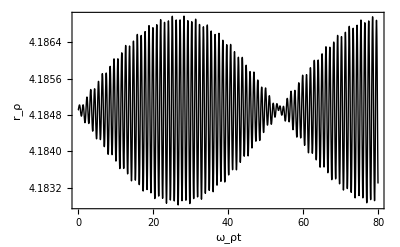

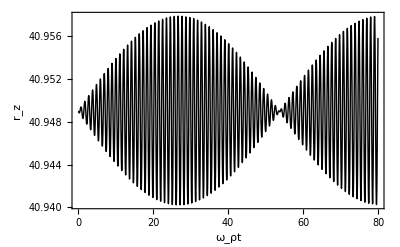

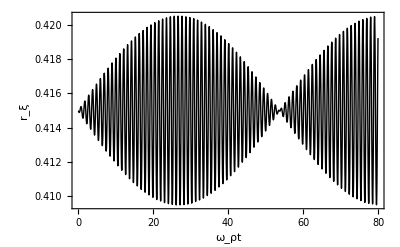

-Graphics-

Dropbox/Trabalhos/rz-vortex oscilation/l01g800d24o61-r.eps

Dropbox/Trabalhos/rz-vortex oscilation/l01g800d24o61-z.eps

Dropbox/Trabalhos/rz-vortex oscilation/l01g800d24o61-a.eps

```mathematica
L=1;
d1[α_]:=(-8/315 π (-6+21 α^2+140 α^4+105 α^6-105 α^4 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))/(8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))
d2[α_]:=((8 π (15+7 α^2 (23+35 α^2+15 α^4)-105 α^2 (1+α^2)^(5/2) ArcCoth[√(1+α^2)]))/1575)/(8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))
d3[α_]:=(8/945 π (8-18 α^2+63 α^4+420 α^6+315 α^8-315 α^6 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))/(8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))
d4[α_]:=(-1/2 π (-4/3+2 α^2-(2 α^4 ArcCoth[√(1+α^2)])/(√(1+α^2))))/(8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))
d5[α_]:=(-8/9 π (4+3 α^2-3 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))/(8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))
d6[α_]:=((8 π (48-11 α^2 (8-18 α^2+63 α^4+420 α^6+315 α^8)+3465 α^8 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))/10395)/(8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))
d7[α_]:=((16 π (√(1+α^2) (30+749 α^2+1680 α^4+945 α^6)-105 (4+9 α^2) (α+α^3)^2 ArcTanh[1/(√(1+α^2))]))/(1575 √(1+α^2)))/((8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))^2)
F1[α_]:=(d3[α]D[d3[α],α]-2d6[α]D[d1[α],α])/(4(d3[α]^2-d1[α]d6[α]))
F2[α_]:=D[d2[α],α]/(2d2[α])
F3[α_]:=(2d3[α]D[d1[α],α]-d1[α]D[d3[α],α])/(4(d3[α]^2-d1[α]d6[α]))
G1[α_]:=d1[α] F1[α]+d3[α] F3[α]
G2[α_]:=d1[α](F1[α]^2+D[F1[α],α])+d3[α](4F1[α]F3[α]+D[F3[α],α])+3d6[α] F3[α]^2
G3[α_]:=2G1[α]
G4[α_]:=d4[α] L^2+L^2 d5[α]
G5[α_]:=d2[α]F2[α]
G6[α_]:=d2[α](F2[α]^2+D[F2[α],α])
G7[α_]:=2G5[α]
G8[α_]:=D[d1[α],α]F1[α]+1/2 D[d3[α],α]F3[α]
G9[α_]:=D[d2[α],α]F2[α]
G10[α_]:=D[d1[α],α](F1[α]^2+D[F1[α],α])+D[d3[α],α](1/2 D[F3[α],α]+2F1[α]F3[α])+D[d6[α],α] F3[α]^2
G11[α_]:=D[d2[α],α](F2[α]^2+D[F2[α],α])
G12[α_]:=2D[d1[α],α]F1[α]+D[d3[α],α]F3[α]
G13[α_]:=2G9[α]
G14[α_]:=D[d4[α],α] L^2+L^2 D[d5[α],α]


γ[t_]:=γ0+δγ Cos[Ω t]

eqρ=d1[α0]ρ0==G4[α0]/ρ0^3+(4π γ0 d7[α0])/(ρ0^3 z0);
eqz=d2[α0] λ^2 z0==(2π γ0 d7[α0])/(ρ0^2 z0^2);
eqα=D[d1[α0],α0] ρ0^2+D[d2[α0],α0] λ^2 z0^2+G14[α0]/ρ0^2+(4π γ0 D[d7[α0],α0])/(ρ0^2 z0)==0;

eq1=d1[a](D[r[t],t,t]+ex r[t])+G1[a]r[t]D[α[t],t,t]+G2[a]r[t] D[α[t],t]^2+G3[a]D[r[t],t]D[α[t],t]-G4[a]/r[t]^3-(4d7[a]π γ[t])/(r[t]^3 z[t])==0/.a->α[t];
eq2=d2[a](D[z[t],t,t]+ex λ^2 z[t])+G5[a]z[t]D[α[t],t,t]+G6[a]z[t] D[α[t],t]^2+G7[a]D[z[t],t]D[α[t],t]-(2d7[a]π γ[t])/(r[t]^2 z[t]^2)==0/.a->α[t];
eq3=D[d1[a],a]r[t](D[r[t],t,t]+ex r[t])+D[d2[a],a]z[t](D[z[t],t,t]+ex λ^2 z[t])+(G8[a] r[t]^2+G9[a] z[t]^2)D[α[t],t,t]+(G10[a] r[t]^2+G11[a] z[t]^2)D[α[t],t]^2+G12[a] r[t]D[r[t],t]D[α[t],t]+G13[a]z[t]D[z[t],t]D[α[t],t]+G14[a]/r[t]^2+(4D[d7[a],a]π γ[t])/(r[t]^2 z[t])==0/.a->α[t];
ex=1;
γ0=800;
λ=0.1;
Ω=6
δγ=0.4;
L=1;

ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}]

se=NDSolve[{eq1,eq2,eq3,r[0]==Evaluate[ρ0/.ss],z[0]==Evaluate[z0/.ss],α[0]==Evaluate[α0/.ss],D[r[t],t]==0/.t->0,D[z[t],t]==0/.t->0,D[α[t],t]==0/.t->0},{r[t],z[t],α[t]},{t,0,150},MaxSteps->100000]

t0=80;

f1=Plot[{Evaluate[r[t]/.se]},{t,0,t0},Frame->True,Axes->False,FrameLabel->{"ω_ρt","r_ρ"},LabelStyle->{Medium},PlotRange->All,RotateLabel->False,PlotStyle->{Black}]
f2=Plot[{Evaluate[z[t]/.se]},{t,0,t0},Frame->True,Axes->False,FrameLabel->{"ω_ρt","r_z"},LabelStyle->{Medium},PlotRange->All,RotateLabel->False,PlotStyle->{Black}]
f3=Plot[{Evaluate[α[t]/.se]*Evaluate[r[t]/.se]},{t,0,t0},Frame->True,Axes->False,FrameLabel->{"ω_ρt","r_ξ"},LabelStyle->{Medium},PlotRange->All,RotateLabel->False,PlotStyle->{Black}]

t=Table[t,{t,0,1000,1/10}];

lr=r[t]/.se;

lz=z[t]/.se;

lrr =lr[[1]];

Df=Df=Abs[Fourier[lrr]]^2;

f4=ListPlot[Table[{N[i((2π)/1000)],Df[[i]]},{i,1,10000}],PlotRange->{{5.6,6.6},{0,0.003}},Joined->True,Axes->False,Frame->True,FrameLabel->{"ϖ","Amplitude"},LabelStyle->{Medium}]


Export["Dropbox/Trabalhos/rz-vortex oscilation/l01g800d24o61-r.eps",f1]
Export["Dropbox/Trabalhos/rz-vortex oscilation/l01g800d24o61-z.eps",f2]
Export["Dropbox/Trabalhos/rz-vortex oscilation/l01g800d24o61-a.eps",f3]

ClearAll[λ,ss,se]

ClearAll[ex,vp,d1,d2,d3,d4,d5,d6,F1,F2,F3,G1,G2,G3,G4,G5,G6,G7,G8,G9,G10,G11,G12,G13,G14,ss,se,λ,L,γ,γ0,δγ,eqρ, eqz,eqα,eq1,eq2,eq3,Ω,d7,f1,f2,f3,f4,lr,t,lrr,lz,lzz,Df,t0]
```

```mathematica
N[956((2π)/1000)]
N[975((2π)/1000)]
6.211-1/2 0.159
```

6.00673

6.12611

6.1315

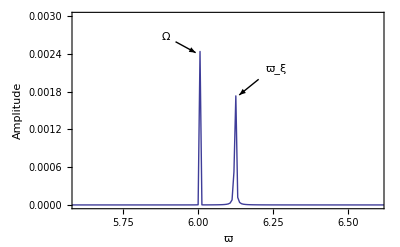
```mathematica
Export["Dropbox/Trabalhos/rz-vortex oscilation/fslm.eps",-Graphics-]
```

Dropbox/Trabalhos/rz-vortex oscilation/fslm.eps

### Gráfico dos Modos

```mathematica
Needs["PlotLegends`"]
```

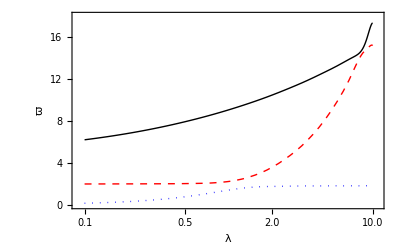

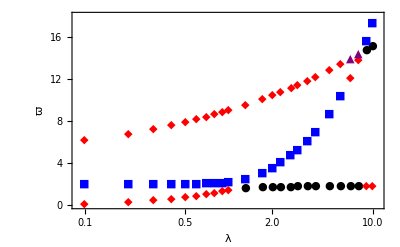

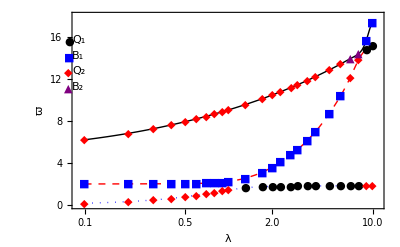

Dropbox/Trabalhos/rz-vortex oscilation/modosXlambda.eps

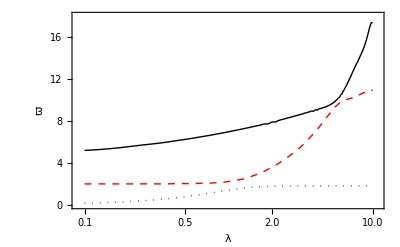

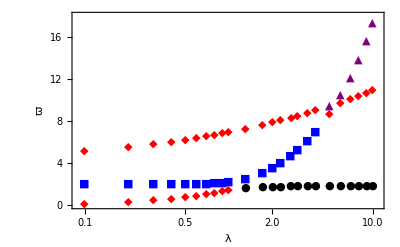

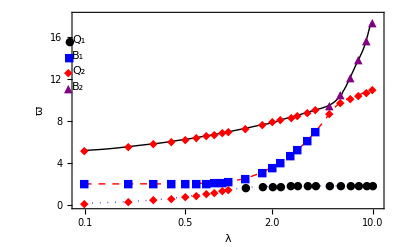

Dropbox/Trabalhos/rz-vortex oscilation/modosXlambda2.eps

```mathematica
QM1={{1.3,1.626},{1.7,1.733},{2,1.766},{2.3,1.784},{2.7,1.787},{3,1.804},{3.5,1.811},{4,1.815},{5,1.819},{6,1.822},{7,1.823},{8,1.824},{9,14.793},{10,15.191}};
BM1={{0.1,2.001},{0.2,2.005},{0.3,2.011},{0.4,2.021},{0.5,2.035},{0.6,2.054},{0.7,2.080},{0.8,2.117},{0.9,2.166},{1,2.231},{1.3,2.534},{1.7,3.108},{2,3.588},{2.3,4.083},{2.7,4.756},{3,5.265},{3.5,6.119},{4,6.976},{5,8.697},{6,10.420},{9,15.628},{10,17.347}};
QM2={{0.1,6.211},{0.1,0.159},{0.2,6.817},{0.2,0.318},{0.3,7.266},{0.3,0.474},{0.4,0.629},{0.5,0.780},{0.6,0.927},{0.7,1.067},{0.8,1.198},{0.9,1.318},{1,1.421},{0.4,7.629},{0.5,7.938},{0.6,8.209},{0.7,8.451},{0.8,8.671},{0.9,8.874},{1,9.062},{1.3,9.558},{1.7,10.111},{2,10.47},{2.3,10.793},{2.7,11.182},{3,11.448},{3.5,11.854},{4,12.222},{5,12.872},{6,13.438},{7,12.144},{8,13.853},{9,1.825},{10,1.825}};
BM2={{7,13.945},{8,14.420}};
ωz={{0.1,0.159},{0.2,0.318},{0.3,0.474},{0.4,0.629},{0.5,0.780},{0.6,0.927},{0.7,1.067},{0.8,1.198},{0.9,1.318},{1,1.421},{1.3,1.626},{1.7,1.733},{2,1.766},{2.3,1.784},{2.7,1.787},{3,1.804},{3.5,1.811},{4,1.815},{5,1.819},{6,1.822},{7,1.823},{8,1.824},{9,1.825},{10,1.825}};
ωρ={{0.1,2.001},{0.2,2.005},{0.3,2.011},{0.4,2.021},{0.5,2.035},{0.6,2.054},{0.7,2.080},{0.8,2.117},{0.9,2.166},{1,2.231},{1.3,2.534},{1.7,3.108},{2,3.588},{2.3,4.083},{2.7,4.756},{3,5.265},{3.5,6.119},{4,6.976},{5,8.697},{6,10.420},{7,12.144},{8,13.853},{9,14.793},{10,15.191}};
ωξ={{0.1,6.211},{0.2,6.817},{0.3,7.266},{0.4,7.629},{0.5,7.938},{0.6,8.209},{0.7,8.451},{0.8,8.671},{0.9,8.874},{1,9.062},{1.3,9.558},{1.7,10.111},{2,10.47},{2.3,10.793},{2.7,11.182},{3,11.448},{3.5,11.854},{4,12.222},{5,12.872},{6,13.438},{7,13.945},{8,14.420},{9,15.628},{10,17.347}};
fz=Fit[ωz,{1,x,x^2,x^3,x^4,x^6,x^7,x^8,x^9,x^10,x^11,ⅇ^(-x^2),Cos[x],Cos[x^2]},x];
fρ=Fit[ωρ,{1,x,x^2,x^3,x^4,x^6,x^7,x^8,x^9,x^10,x^11,Cos[π x],Cos[2 π x],Cos[3 π x],Cos[4 π x],Cos[5 π x],Cos[6π x],Cos[7π x],Cos[8π x]},x];
fξ=Fit[ωξ,{1,x,x^2,x^3,x^4,x^6,x^7,x^8,x^9,x^10,x^11,ⅇ^(-x^2),Cos[π x],x^-x},x];
f1=LogLinearPlot[{fz,fρ,fξ},{x,0.1,10},PlotStyle->{{Blue,Dotted},{Red,Dashed},Black},Frame->True,Axes->False,FrameLabel->{"λ","ϖ"},RotateLabel->False,LabelStyle->{Medium},PlotRange->{{0.09,10.9},{0,18}}]
f2=ListLogLinearPlot[{QM1,BM1,QM2,BM2},PlotStyle->{Black,Blue,Red,Purple},PlotMarkers->{Automatic,Small},Frame->True,Axes->False,FrameLabel->{"λ","ϖ"},RotateLabel->False,LabelStyle->{Medium},PlotRange->{{0.09,10.9},{0,18}}]
f3=ShowLegend[Show[{f1,f2}],{{{Style["●",Black],"Q_1"},{Style["■",Blue],"B_1"},{Style["◆",Red],"Q_2"},{Style["▲",Purple],"B_2"}},LegendPosition->{-0.7,0.1},LegendSize->{0.15,0.4},LegendShadow->False}]
Export["Dropbox/Trabalhos/rz-vortex oscilation/modosXlambda.eps",f3]
ClearAll[QM1,BM1,QM2,BM2,f1,f2,f3,ωξ,ωρ,ωz,fz,fρ,fξ]

QM1={{1.3,1.636},{1.7,1.741},{2,1.773},{2.3,1.790},{2.7,1.803},{3,1.809},{3.5,1.815},{4,1.819},{5,1.823},{6,1.825},{7,1.826},{8,1.827},{9,1.827},{10,1.827}};
BM1={{0.1,2.001},{0.2,2.004},{0.3,2.010},{0.4,2.019},{0.5,2.032},{0.6,2.051},{0.7,2.076},{0.8,2.111},{0.9,2.158},{1,2.222},{1.3,2.524},{1.7,3.099},{2,3.579},{2.3,4.075},{2.7,4.747},{3,5.256},{3.5,6.108},{4,6.962}};
QM2={{0.1,0.161},{0.1,5.200},{0.2,0.319},{0.2,5.549},{0.3,0.476},{0.3,5.825},{0.4,6.053},{0.4,0.632},{0.5,0.784},{0.5,6.249},{0.6,6.423},{0.6,0.932},{0.7,6.579},{0.7,1.073},{0.8,6.721},{0.8,1.205},{0.9,6.852},{0.9,1.326},{1,6.974},{1,1.420},{1.3,7.298},{1.7,7.650},{2,7.895},{2.3,8.107},{2.7,8.363},{3,8.539},{3.5,8.808},{4,9.053},{5,8.658},{6,9.782},{7,10.149},{8,10.455},{9,10.733},{10,10.989}};
BM2={{5,9.505},{6,10.478},{7,12.169},{8,13.890},{9,15.617},{10,17.345}};
ωz={{0.1,0.161},{0.2,0.319},{0.3,0.476},{0.4,0.632},{0.5,0.784},{0.6,0.932},{0.7,1.073},{0.8,1.205},{0.9,1.326},{1,1.420},{1.3,1.636},{1.7,1.741},{2,1.773},{2.3,1.790},{2.7,1.803},{3,1.809},{3.5,1.815},{4,1.819},{5,1.823},{6,1.825},{7,1.826},{8,1.827},{9,1.827},{10,1.827}};
ωρ={{0.1,2.001},{0.2,2.004},{0.3,2.010},{0.4,2.019},{0.5,2.032},{0.6,2.051},{0.7,2.076},{0.8,2.111},{0.9,2.158},{1,2.222},{1.3,2.524},{1.7,3.099},{2,3.579},{2.3,4.075},{2.7,4.747},{3,5.256},{3.5,6.108},{4,6.962},{5,8.658},{6,9.782},{7,10.149},{8,10.455},{9,10.733},{10,10.989}};
ωξ={{0.1,5.200},{0.2,5.549},{0.3,5.825},{0.4,6.053},{0.5,6.249},{0.6,6.423},{0.7,6.579},{0.8,6.721},{0.9,6.852},{1,6.974},{1.3,7.298},{1.7,7.650},{2,7.895},{2.3,8.107},{2.7,8.363},{3,8.539},{3.5,8.808},{4,9.053},{5,9.505},{6,10.478},{7,12.169},{8,13.890},{9,15.617},{10,17.345}};
fz=Fit[ωz,{1,x,x^2,x^3,x^4,x^6,x^7,x^8,x^9,x^10,x^11,ⅇ^(-x^2),ⅇ^(-x^3),Cos[x]},x];
fρ=Fit[ωρ,{1,x,x^2,x^3,x^4,x^6,x^7,x^8,x^9,x^10,x^11,Cos[π x],Cos[2 π x],Cos[3 π x],Cos[4 π x],Cos[5 π x],Cos[6π x],Cos[7π x],Cos[8π x],Cos[9π x],Cos[10π x],Cos[11π x]},x];
fξ=Fit[ωξ,{1,x,x^2,x^3,x^4,x^6,x^7,x^8,x^9,x^10,x^11,ⅇ^(-x^2),ⅇ^(-x^3),Cos[π x],Cos[2π x],Cos[3π x],Cos[4π x],Cos[5π x],Cos[6π x],Cos[7π x],Cos[8π x],Cos[9π x],Cos[10π x]},x];
f1=LogLinearPlot[{fz,fρ,fξ},{x,0.1,10},PlotStyle->{{Blue,Dotted},{Red,Dashed},Black},Frame->True,Axes->False,FrameLabel->{"λ","ϖ"},RotateLabel->False,LabelStyle->{Medium},PlotRange->{{0.09,10.9},{0,18}}]
f2=ListLogLinearPlot[{QM1,BM1,QM2,BM2},PlotStyle->{Black,Blue,Red,Purple},PlotMarkers->{Automatic,Small},Frame->True,Axes->False,FrameLabel->{"λ","ϖ"},RotateLabel->False,LabelStyle->{Medium},PlotRange->{{0.09,10.9},{0,18}}]
f3=ShowLegend[Show[{f1,f2}],{{{Style["●",Black],"Q_1"},{Style["■",Blue],"B_1"},{Style["◆",Red],"Q_2"},{Style["▲",Purple],"B_2"}},LegendPosition->{-0.7,0.1},LegendSize->{0.15,0.4},LegendShadow->False}]
Export["Dropbox/Trabalhos/rz-vortex oscilation/modosXlambda2.eps",f3]
ClearAll[QM1,BM1,QM2,BM2,f1,f2,f3,ωξ,ωρ,ωz,fz,fρ,fξ]
```

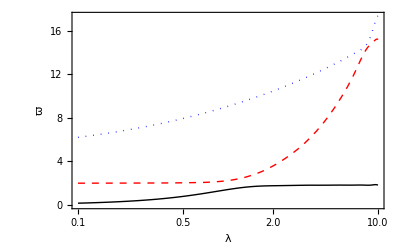

-Graphics-

Dropbox/Trabalhos/rz-vortex oscilation/modosXlambda.eps

-Graphics-

Dropbox/Trabalhos/rz-vortex oscilation/modosXlambda2.eps

```mathematica
QM1={{1.3,1.626},{1.7,1.733},{2,1.766},{2.3,1.784},{2.7,1.787},{3,1.804},{3.5,1.811},{4,1.815},{5,1.819},{6,1.822},{7,1.823},{8,1.824},{9,14.793},{10,15.191}};
BM1={{0.1,2.001},{0.2,2.005},{0.3,2.011},{0.4,2.021},{0.5,2.035},{0.6,2.054},{0.7,2.080},{0.8,2.117},{0.9,2.166},{1,2.231},{1.3,2.534},{1.7,3.108},{2,3.588},{2.3,4.083},{2.7,4.756},{3,5.265},{3.5,6.119},{4,6.976},{5,8.697},{6,10.420},{9,15.628},{10,17.347}};
QM2={{0.1,6.211},{0.1,0.159},{0.2,6.817},{0.2,0.318},{0.3,7.266},{0.3,0.474},{0.4,0.629},{0.5,0.780},{0.6,0.927},{0.7,1.067},{0.8,1.198},{0.9,1.318},{1,1.421},{0.4,7.629},{0.5,7.938},{0.6,8.209},{0.7,8.451},{0.8,8.671},{0.9,8.874},{1,9.062},{1.3,9.558},{1.7,10.111},{2,10.47},{2.3,10.793},{2.7,11.182},{3,11.448},{3.5,11.854},{4,12.222},{5,12.872},{6,13.438},{7,12.144},{8,13.853},{9,1.825},{10,1.825}};
BM2={{7,13.945},{8,14.420}};
ωz={{0.1,0.159},{0.2,0.318},{0.3,0.474},{0.4,0.629},{0.5,0.780},{0.6,0.927},{0.7,1.067},{0.8,1.198},{0.9,1.318},{1,1.421},{1.3,1.626},{1.7,1.733},{2,1.766},{2.3,1.784},{2.7,1.787},{3,1.804},{3.5,1.811},{4,1.815},{5,1.819},{6,1.822},{7,1.823},{8,1.824},{9,1.825},{10,1.825}};
ωρ={{0.1,2.001},{0.2,2.005},{0.3,2.011},{0.4,2.021},{0.5,2.035},{0.6,2.054},{0.7,2.080},{0.8,2.117},{0.9,2.166},{1,2.231},{1.3,2.534},{1.7,3.108},{2,3.588},{2.3,4.083},{2.7,4.756},{3,5.265},{3.5,6.119},{4,6.976},{5,8.697},{6,10.420},{7,12.144},{8,13.853},{9,14.793},{10,15.191}};
ωξ={{0.1,6.211},{0.2,6.817},{0.3,7.266},{0.4,7.629},{0.5,7.938},{0.6,8.209},{0.7,8.451},{0.8,8.671},{0.9,8.874},{1,9.062},{1.3,9.558},{1.7,10.111},{2,10.47},{2.3,10.793},{2.7,11.182},{3,11.448},{3.5,11.854},{4,12.222},{5,12.872},{6,13.438},{7,13.945},{8,14.420},{9,15.628},{10,17.347}};
fz=Fit[ωz,{1,x,x^2,x^3,x^4,x^6,x^7,x^8,x^9,x^10,x^11,ⅇ^(-x^2),Cos[x],Cos[x^2]},x];
fρ=Fit[ωρ,{1,x,x^2,x^3,x^4,x^6,x^7,x^8,x^9,x^10,x^11,Cos[π x],Cos[2 π x],Cos[3 π x],Cos[4 π x],Cos[5 π x],Cos[6π x],Cos[7π x],Cos[8π x]},x];
fξ=Fit[ωξ,{1,x,x^2,x^3,x^4,x^6,x^7,x^8,x^9,x^10,x^11,ⅇ^(-x^2),Cos[π x],x^-x},x];
f1=LogLinearPlot[{fz,fρ,fξ},{x,0.1,10},PlotStyle->{Black,{Red,Dashed},{Blue,Dotted}},Frame->True,Axes->False,FrameLabel->{"λ","ϖ"},RotateLabel->False,LabelStyle->{Medium}]
f2=ListLogLinearPlot[{QM1,BM1,QM2,BM2},PlotRange->{{0.09,10.9},{0,18}},Frame->True,Axes->False,FrameLabel->{"λ","ϖ"},RotateLabel->False,LabelStyle->{Medium},PlotLegend->{Subscript[Q, 1],Subscript[B, 1],Subscript[Q, 2],Subscript[B, 2]},LegendSize->{0.2,0.4},LegendShadow->{0,0},PlotStyle->{Black,Blue,Red,Purple},LegendPosition->{-0.70,0.1},PlotMarkers->{Automatic,Tiny}]
Export["Dropbox/Trabalhos/rz-vortex oscilation/modosXlambda.eps",f2]
ClearAll[QM1,BM1,QM2,BM2,f1,f2,f3,ωξ,ωρ,ωz,fz,fρ,fξ]

QM1={{1.3,1.636},{1.7,1.741},{2,1.773},{2.3,1.790},{2.7,1.803},{3,1.809},{3.5,1.815},{4,1.819},{5,1.823},{6,1.825},{7,1.826},{8,1.827},{9,1.827},{10,1.827}};
BM1={{0.1,2.001},{0.2,2.004},{0.3,2.010},{0.4,2.019},{0.5,2.032},{0.6,2.051},{0.7,2.076},{0.8,2.111},{0.9,2.158},{1,2.222},{1.3,2.524},{1.7,3.099},{2,3.579},{2.3,4.075},{2.7,4.747},{3,5.256},{3.5,6.108},{4,6.962}};
QM2={{0.1,0.161},{0.1,5.200},{0.2,0.319},{0.2,5.549},{0.3,0.476},{0.3,5.825},{0.4,6.053},{0.4,0.632},{0.5,0.784},{0.5,6.249},{0.6,6.423},{0.6,0.932},{0.7,6.579},{0.7,1.073},{0.8,6.721},{0.8,1.205},{0.9,6.852},{0.9,1.326},{1,6.974},{1,1.420},{1.3,7.298},{1.7,7.650},{2,7.895},{2.3,8.107},{2.7,8.363},{3,8.539},{3.5,8.808},{4,9.053},{5,8.658},{6,9.782},{7,10.149},{8,10.455},{9,10.733},{10,10.989}};
BM2={{5,9.505},{6,10.478},{7,12.169},{8,13.890},{9,15.617},{10,17.345}};
f2=ListLogLinearPlot[{QM1,BM1,QM2,BM2},PlotRange->{{0.09,10.9},{0,18}},Frame->True,Axes->False,FrameLabel->{"λ","ϖ"},RotateLabel->False,LabelStyle->{Medium},PlotLegend->{Subscript[Q, 1],Subscript[B, 1],Subscript[Q, 2],Subscript[B, 2]},LegendSize->{0.2,0.4},LegendShadow->{0,0},PlotStyle->{Black,Blue,Red,Purple},LegendPosition->{-0.70,0.1},PlotMarkers->{Automatic,Tiny}]
Export["Dropbox/Trabalhos/rz-vortex oscilation/modosXlambda2.eps",f2]
ClearAll[QM1,BM1,QM2,BM2,f1,f2,ωξ,ωρ,ωz]
```

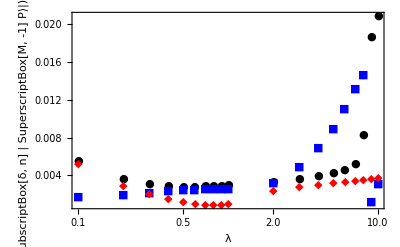

Dropbox/Trabalhos/rz-vortex oscilation/nMP.eps

```mathematica
P1={{0.1,-0.00552214},{0.2,-0.0036073},{0.3,-0.00308474},{0.4,-0.0029082},{0.5,-0.00285488},{0.6,-0.00285308},{0.7,-0.0028748},{0.8,-0.00290772},{0.9,-0.00294594},{1,-0.00298647},{2,-0.00336841},{3,-0.00367726},{4,-0.00395496},{5,-0.0042434},{6,-0.00460976},{7,-0.00527346},{8,-0.00826694},{9,-0.0186539},{10,0.0208717}};
P2={{0.1,0.00171279},{0.2,0.0020081},{0.3,0.00219541},{0.4,0.00233506},{0.5,0.00244519},{0.6,0.00253175},{0.7,0.00259482},{0.8,0.00263131},{0.9,0.00263853},{1,0.00261991},{2,0.00324532},{3,0.00495277},{4,0.00689477},{5,0.00895592},{6,0.0110906},{7,0.0132305},{8,-0.0147082},{9,0.0011916},{10,0.00312136}};
P3={{0.1,0.00519049},{0.2,0.00288942},{0.3,0.00201097},{0.4,0.00153041},{0.5,0.00122763},{0.6,0.00103029},{0.7,0.000911882},{0.8,0.000864561},{0.9,-0.000887718},{1,-0.00097917},{2,-0.00234639},{3,-0.00279346},{4,-0.00303447},{5,-0.00320642},{6,-0.00334338},{7,-0.003458876},{8,0.00355927},{9,0.00364879},{10,0.00372979}};
f3=ListLogLinearPlot[{Abs[P1],Abs[P2],Abs[P3]},PlotRange->All,Frame->True,Axes->False,FrameLabel->{"λ","(|⟨SubscriptBox[δ, n] | SuperscriptBox[M, -1] P⟩|)/(2 π δγ)"},RotateLabel->False,LabelStyle->{Medium},PlotLegend->{"n=ξ","n=ρ","n=z"},LegendSize->{0.2,0.4},LegendShadow->{0,0},PlotStyle->{Black,Blue,Red},LegendPosition->{-0.40,-0.02},PlotMarkers->{Automatic,Tiny}]
Export["Dropbox/Trabalhos/rz-vortex oscilation/nMP.eps",f3]
ClearAll[P1,P2,P3,f3]
```

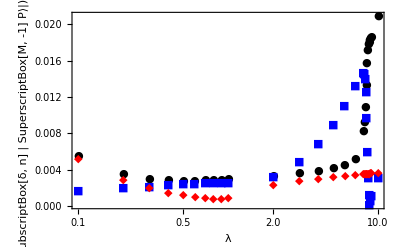

Dropbox/Trabalhos/rz-vortex oscilation/nMP2.eps

```mathematica
P1={{0.1,-0.00552214},{0.2,-0.0036073},{0.3,-0.00308474},{0.4,-0.0029082},{0.5,-0.00285488},{0.6,-0.00285308},{0.7,-0.0028748},{0.8,-0.00290772},{0.9,-0.00294594},{1,-0.00298647},{2,-0.00336841},{3,-0.00367726},{4,-0.00395496},{5,-0.0042434},{6,-0.00460976},{7,-0.00527346},{8,-0.00826694},{8.1,-0.00934358},{8.2,-0.0109632},{8.3,-0.0132964},{8.4,-0.0157939},{8.5,-0.0172477},{8.6,-0.0178064},{8.7,-0.0180727},{8.8,-0.0182711},{8.9,-0.0184602},{9,-0.0186539},{10,0.0208717}};
P2={{0.1,0.00171279},{0.2,0.0020081},{0.3,0.00219541},{0.4,0.00233506},{0.5,0.00244519},{0.6,0.00253175},{0.7,0.00259482},{0.8,0.00263131},{0.9,0.00263853},{1,0.00261991},{2,0.00324532},{3,0.00495277},{4,0.00689477},{5,0.00895592},{6,0.0110906},{7,0.0132305},{8,-0.0147082},{8.1,-0.0145229},{8.2,0.0139716},{8.3,0.0125802},{8.4,0.00968341},{8.5,-0.00597939},{8.6,-0.00312263},{8.7,-0.0013069},{8.8,-0.0001467749},{8.9,0.000635272},{9,0.0011916},{10,0.00312136}};
P3={{0.1,0.00519049},{0.2,0.00288942},{0.3,0.00201097},{0.4,0.00153041},{0.5,0.00122763},{0.6,0.00103029},{0.7,0.000911882},{0.8,0.000864561},{0.9,-0.000887718},{1,-0.00097917},{2,-0.00234639},{3,-0.00279346},{4,-0.00303447},{5,-0.00320642},{6,-0.00334338},{7,-0.003458876},{8,0.00355927},{8.1,0.00356867},{8.2,0.00357796},{8.3,0.00358715},{8.4,0.00359623},{8.5,0.00360522},{8.6,0.00361412},{8.7,0.00362292},{8.8,0.00363163},{8.9,0.00364025},{9,0.00364879},{10,0.00372979}};
f3=ListLogLinearPlot[{Abs[P1],Abs[P2],Abs[P3]},PlotRange->All,Frame->True,Axes->False,FrameLabel->{"λ","(|⟨SubscriptBox[δ, n] | SuperscriptBox[M, -1] P⟩|)/(2 π δγ)"},RotateLabel->False,LabelStyle->{Medium},PlotLegend->{"n=ξ","n=ρ","n=z"},LegendSize->{0.2,0.4},LegendShadow->{0,0},PlotStyle->{Black,Blue,Red},LegendPosition->{-0.40,-0.02},PlotMarkers->{Automatic,Tiny}]
Export["Dropbox/Trabalhos/rz-vortex oscilation/nMP2.eps",f3]
ClearAll[P1,P2,P3,f3]
```

## Expansão livre

### ℓ=1

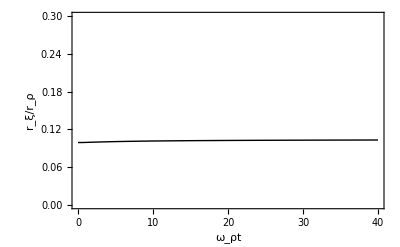

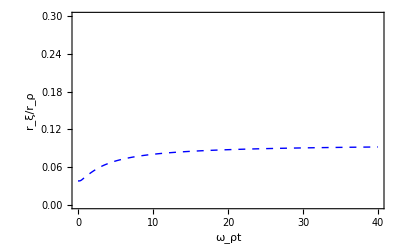

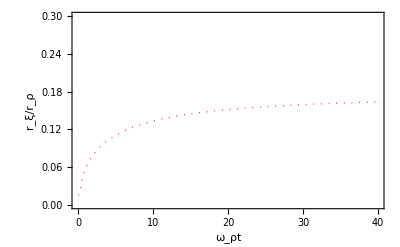

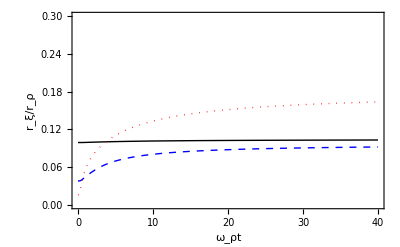

Dropbox/Trabalhos/rz-vortex oscilation/vel-r.eps

```mathematica
L=1;
d1[α_]:=(-8/315 π (-6+21 α^2+140 α^4+105 α^6-105 α^4 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))/(8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))
d2[α_]:=((8 π (15+7 α^2 (23+35 α^2+15 α^4)-105 α^2 (1+α^2)^(5/2) ArcCoth[√(1+α^2)]))/1575)/(8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))
d3[α_]:=(8/945 π (8-18 α^2+63 α^4+420 α^6+315 α^8-315 α^6 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))/(8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))
d4[α_]:=(-1/2 π (-4/3+2 α^2-(2 α^4 ArcCoth[√(1+α^2)])/(√(1+α^2))))/(8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))
d5[α_]:=(-8/9 π (4+3 α^2-3 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))/(8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))
d6[α_]:=((8 π (48-11 α^2 (8-18 α^2+63 α^4+420 α^6+315 α^8)+3465 α^8 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))/10395)/(8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))
d7[α_]:=((16 π (√(1+α^2) (30+749 α^2+1680 α^4+945 α^6)-105 (4+9 α^2) (α+α^3)^2 ArcTanh[1/(√(1+α^2))]))/(1575 √(1+α^2)))/((8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))^2)
F1[α_]:=(d3[α]D[d3[α],α]-2d6[α]D[d1[α],α])/(4(d3[α]^2-d1[α]d6[α]))
F2[α_]:=D[d2[α],α]/(2d2[α])
F3[α_]:=(2d3[α]D[d1[α],α]-d1[α]D[d3[α],α])/(4(d3[α]^2-d1[α]d6[α]))
G1[α_]:=d1[α] F1[α]+d3[α] F3[α]
G2[α_]:=d1[α](F1[α]^2+D[F1[α],α])+d3[α](4F1[α]F3[α]+D[F3[α],α])+3d6[α] F3[α]^2
G3[α_]:=2G1[α]
G4[α_]:=d4[α] L^2+L^2 d5[α]
G5[α_]:=d2[α]F2[α]
G6[α_]:=d2[α](F2[α]^2+D[F2[α],α])
G7[α_]:=2G5[α]
G8[α_]:=D[d1[α],α]F1[α]+1/2 D[d3[α],α]F3[α]
G9[α_]:=D[d2[α],α]F2[α]
G10[α_]:=D[d1[α],α](F1[α]^2+D[F1[α],α])+D[d3[α],α](1/2 D[F3[α],α]+2F1[α]F3[α])+D[d6[α],α] F3[α]^2
G11[α_]:=D[d2[α],α](F2[α]^2+D[F2[α],α])
G12[α_]:=2D[d1[α],α]F1[α]+D[d3[α],α]F3[α]
G13[α_]:=2G9[α]
G14[α_]:=D[d4[α],α] L^2+L^2 D[d5[α],α]

eqρ=d1[α0]ρ0==G4[α0]/ρ0^3+(4π γ d7[α0])/(ρ0^3 z0);
eqz=d2[α0] λ^2 z0==(2π γ d7[α0])/(ρ0^2 z0^2);
eqα=D[d1[α0],α0] ρ0^2+D[d2[α0],α0] λ^2 z0^2+G14[α0]/ρ0^2+(4π γ D[d7[α0],α0])/(ρ0^2 z0)==0;

eq1=d1[a](D[r[t],t,t]+ex r[t])+G1[a]r[t]D[α[t],t,t]+G2[a]r[t] D[α[t],t]^2+G3[a]D[r[t],t]D[α[t],t]-G4[a]/r[t]^3-(4π d7[a]γ)/(r[t]^3 z[t])==0/.a->α[t];
eq2=d2[a](D[z[t],t,t]+ex λ^2 z[t])+G5[a]z[t]D[α[t],t,t]+G6[a]z[t] D[α[t],t]^2+G7[a]D[z[t],t]D[α[t],t]-(2π d7[a]γ)/(r[t]^2 z[t]^2)==0/.a->α[t];
eq3=D[d1[a],a]r[t](D[r[t],t,t]+ex r[t])+D[d2[a],a]z[t](D[z[t],t,t]+ex λ^2 z[t])+(G8[a] r[t]^2+G9[a] z[t]^2)D[α[t],t,t]+(G10[a] r[t]^2+G11[a] z[t]^2)D[α[t],t]^2+G12[a] r[t]D[r[t],t]D[α[t],t]+G13[a]z[t]D[z[t],t]D[α[t],t]+G14[a]/r[t]^2+(4π D[d7[a],a]γ)/(r[t]^2 z[t])==0/.a->α[t];
γ=800;
ex=0;

ClearAll[λ,ss,se]

λ=0.1;

ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}];

se=NDSolve[{eq1,eq2,eq3,r[0]==Evaluate[ρ0/.ss],z[0]==Evaluate[z0/.ss],α[0]==Evaluate[α0/.ss],D[r[t],t]==0/.t->0,D[z[t],t]==0/.t->0,D[α[t],t]==0/.t->0},{r[t],z[t],α[t]},{t,0,40}];

f1=Plot[Evaluate[α[t]/.se],{t,0,40},Frame->True,Axes->False,FrameLabel->{"ω_ρt","r_ξ/r_ρ"},PlotRange->{0,0.3},LabelStyle->{Medium},RotateLabel->False,PlotStyle->{Black}]


ClearAll[λ,ss,se]

λ=1;

ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}];

se=NDSolve[{eq1,eq2,eq3,r[0]==Evaluate[ρ0/.ss],z[0]==Evaluate[z0/.ss],α[0]==Evaluate[α0/.ss],D[r[t],t]==0/.t->0,D[z[t],t]==0/.t->0,D[α[t],t]==0/.t->0},{r[t],z[t],α[t]},{t,0,40}];

f2=Plot[Evaluate[α[t]/.se],{t,0,40},Frame->True,Axes->False,FrameLabel->{"ω_ρt","r_ξ/r_ρ"},PlotRange->{0,0.3},LabelStyle->{Medium},RotateLabel->False,PlotStyle->{Directive[Blue,Dashed]}]


ClearAll[λ,ss,se]

λ=8;

ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}];

se=NDSolve[{eq1,eq2,eq3,r[0]==Evaluate[ρ0/.ss],z[0]==Evaluate[z0/.ss],α[0]==Evaluate[α0/.ss],D[r[t],t]==0/.t->0,D[z[t],t]==0/.t->0,D[α[t],t]==0/.t->0},{r[t],z[t],α[t]},{t,0,40}];


f3=Plot[Evaluate[α[t]/.se],{t,0,40},Frame->True,Axes->False,FrameLabel->{"ω_ρt","r_ξ/r_ρ"},PlotRange->{0,0.3},LabelStyle->{Medium},RotateLabel->False,PlotStyle->{Directive[Red,Dotted]}]

g1=Show[ {f1,f2,f3}]

ClearAll[λ,L,γ]

Export["Dropbox/Trabalhos/rz-vortex oscilation/vel-r.eps",g1]

ClearAll[d1,d2,d3,d4,d5,d6,d7,F1,F2,F3,G1,G2,G3,G4,G5,G6,G7,G8,G9,G10,G11,G12,G13,G14,eq1,eq2,eq3,eqρ,eqz,eqα,λ,γ,se,ss,L,ex,vp,f1,f2,f3,g1,d7,g2,f4,f5,f6]
```

#### Energia

Contribuição de cada fração energética durante a expanção livre.
E=∫ℰⅆ^3 r=E_kin+E_int
E_kin=E_r+E_z+E_v
No caso de um Ansatz TF, o temor cinético será apenas a contribuição do vórtice.

```mathematica
Needs["PlotLegends`"]
```

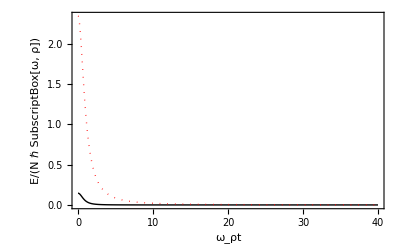

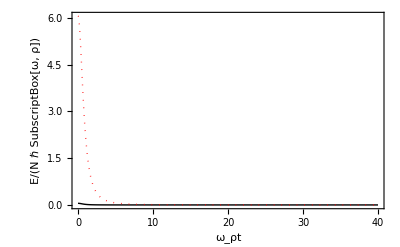

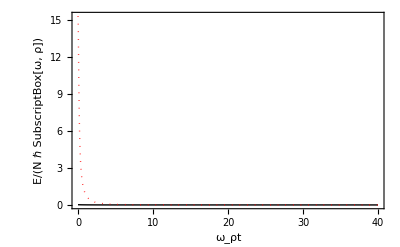

Dropbox/Trabalhos/rz-vortex oscilation/energy-01.eps

Dropbox/Trabalhos/rz-vortex oscilation/energy-1.eps

Dropbox/Trabalhos/rz-vortex oscilation/energy-10.eps

```mathematica
L=1;
d1[α_]:=(-8/315 π (-6+21 α^2+140 α^4+105 α^6-105 α^4 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))/(8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))
d2[α_]:=((8 π (15+7 α^2 (23+35 α^2+15 α^4)-105 α^2 (1+α^2)^(5/2) ArcCoth[√(1+α^2)]))/1575)/(8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))
d3[α_]:=(8/945 π (8-18 α^2+63 α^4+420 α^6+315 α^8-315 α^6 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))/(8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))
d4[α_]:=(-1/2 π (-4/3+2 α^2-(2 α^4 ArcCoth[√(1+α^2)])/(√(1+α^2))))/(8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))
d5[α_]:=(-8/9 π (4+3 α^2-3 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))/(8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))
d6[α_]:=((8 π (48-11 α^2 (8-18 α^2+63 α^4+420 α^6+315 α^8)+3465 α^8 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))/10395)/(8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))
d7[α_]:=((16 π (√(1+α^2) (30+749 α^2+1680 α^4+945 α^6)-105 (4+9 α^2) (α+α^3)^2 ArcTanh[1/(√(1+α^2))]))/(1575 √(1+α^2)))/((8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))^2)
F1[α_]:=(d3[α]D[d3[α],α]-2d6[α]D[d1[α],α])/(4(d3[α]^2-d1[α]d6[α]))
F2[α_]:=D[d2[α],α]/(2d2[α])
F3[α_]:=(2d3[α]D[d1[α],α]-d1[α]D[d3[α],α])/(4(d3[α]^2-d1[α]d6[α]))
G1[α_]:=d1[α] F1[α]+d3[α] F3[α]
G2[α_]:=d1[α](F1[α]^2+D[F1[α],α])+d3[α](4F1[α]F3[α]+D[F3[α],α])+3d6[α] F3[α]^2
G3[α_]:=2G1[α]
G4[α_]:=d4[α] L^2+L^2 d5[α]
G5[α_]:=d2[α]F2[α]
G6[α_]:=d2[α](F2[α]^2+D[F2[α],α])
G7[α_]:=2G5[α]
G8[α_]:=D[d1[α],α]F1[α]+1/2 D[d3[α],α]F3[α]
G9[α_]:=D[d2[α],α]F2[α]
G10[α_]:=D[d1[α],α](F1[α]^2+D[F1[α],α])+D[d3[α],α](1/2 D[F3[α],α]+2F1[α]F3[α])+D[d6[α],α] F3[α]^2
G11[α_]:=D[d2[α],α](F2[α]^2+D[F2[α],α])
G12[α_]:=2D[d1[α],α]F1[α]+D[d3[α],α]F3[α]
G13[α_]:=2G9[α]
G14[α_]:=D[d4[α],α] L^2+L^2 D[d5[α],α]

eqρ=d1[α0]ρ0==G4[α0]/ρ0^3+(4π γ d7[α0])/(ρ0^3 z0);
eqz=d2[α0] λ^2 z0==(2π γ d7[α0])/(ρ0^2 z0^2);
eqα=D[d1[α0],α0] ρ0^2+D[d2[α0],α0] λ^2 z0^2+G14[α0]/ρ0^2+(4π γ D[d7[α0],α0])/(ρ0^2 z0)==0;

eq1=d1[a](D[r[t],t,t]+ex r[t])+G1[a]r[t]D[α[t],t,t]+G2[a]r[t] D[α[t],t]^2+G3[a]D[r[t],t]D[α[t],t]-G4[a]/r[t]^3-(4π d7[a]γ)/(r[t]^3 z[t])==0/.a->α[t];
eq2=d2[a](D[z[t],t,t]+ex λ^2 z[t])+G5[a]z[t]D[α[t],t,t]+G6[a]z[t] D[α[t],t]^2+G7[a]D[z[t],t]D[α[t],t]-(2π d7[a]γ)/(r[t]^2 z[t]^2)==0/.a->α[t];
eq3=D[d1[a],a]r[t](D[r[t],t,t]+ex r[t])+D[d2[a],a]z[t](D[z[t],t,t]+ex λ^2 z[t])+(G8[a] r[t]^2+G9[a] z[t]^2)D[α[t],t,t]+(G10[a] r[t]^2+G11[a] z[t]^2)D[α[t],t]^2+G12[a] r[t]D[r[t],t]D[α[t],t]+G13[a]z[t]D[z[t],t]D[α[t],t]+G14[a]/r[t]^2+(4π D[d7[a],a]γ)/(r[t]^2 z[t])==0/.a->α[t];
Eint[r_,z_,α_]:=(2π γ d7[α])/(r^2 z)
Ev[r_,α_]:=L^2/r^3(d4[α]+d5[α])

γ=800;
ex=0;

ClearAll[λ,ss,se]

λ=0.1;

ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}];

se=NDSolve[{eq1,eq2,eq3,r[0]==Evaluate[ρ0/.ss],z[0]==Evaluate[z0/.ss],α[0]==Evaluate[α0/.ss],D[r[t],t]==0/.t->0,D[z[t],t]==0/.t->0,D[α[t],t]==0/.t->0},{r[t],z[t],α[t]},{t,0,40}];

f1=Plot[{Ev[Evaluate[r[t]/.se],Evaluate[α[t]/.se]],Eint[Evaluate[r[t]/.se],Evaluate[z[t]/.se],Evaluate[α[t]/.se]]},{t,0,40},Frame->True,Axes->False,FrameLabel->{"ω_ρt","E/(N ℏ SubscriptBox[ω, ρ])"},PlotRange->All,LabelStyle->{Medium},RotateLabel->False,PlotStyle->{Black,Directive[Red,Dotted]},PlotLegend->{"E_v","E_int"},LegendSize->{0.2,0.2},LegendShadow->{0,0},LegendPosition->{0.65,0.3}]


ClearAll[λ,ss,se]

λ=1;

ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}];

se=NDSolve[{eq1,eq2,eq3,r[0]==Evaluate[ρ0/.ss],z[0]==Evaluate[z0/.ss],α[0]==Evaluate[α0/.ss],D[r[t],t]==0/.t->0,D[z[t],t]==0/.t->0,D[α[t],t]==0/.t->0},{r[t],z[t],α[t]},{t,0,40}];

f2=Plot[{Ev[Evaluate[r[t]/.se],Evaluate[α[t]/.se]],Eint[Evaluate[r[t]/.se],Evaluate[z[t]/.se],Evaluate[α[t]/.se]]},{t,0,40},Frame->True,Axes->False,FrameLabel->{"ω_ρt","E/(N ℏ SubscriptBox[ω, ρ])"},PlotRange->All,LabelStyle->{Medium},RotateLabel->False,PlotStyle->{Black,Directive[Red,Dotted]},PlotLegend->{"E_v","E_int"},LegendSize->{0.2,0.2},LegendShadow->{0,0},LegendPosition->{0.65,0.3}]



ClearAll[λ,ss,se]

λ=10;

ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}];

se=NDSolve[{eq1,eq2,eq3,r[0]==Evaluate[ρ0/.ss],z[0]==Evaluate[z0/.ss],α[0]==Evaluate[α0/.ss],D[r[t],t]==0/.t->0,D[z[t],t]==0/.t->0,D[α[t],t]==0/.t->0},{r[t],z[t],α[t]},{t,0,40}];

f3=Plot[{Ev[Evaluate[r[t]/.se],Evaluate[α[t]/.se]],Eint[Evaluate[r[t]/.se],Evaluate[z[t]/.se],Evaluate[α[t]/.se]]},{t,0,40},Frame->True,Axes->False,FrameLabel->{"ω_ρt","E/(N ℏ SubscriptBox[ω, ρ])"},PlotRange->All,LabelStyle->{Medium},RotateLabel->False,PlotStyle->{Black,Directive[Red,Dotted]},PlotLegend->{"E_v","E_int"},LegendSize->{0.2,0.2},LegendShadow->{0,0},LegendPosition->{0.65,0.3}]

Export["Dropbox/Trabalhos/rz-vortex oscilation/energy-01.eps",f1]
Export["Dropbox/Trabalhos/rz-vortex oscilation/energy-1.eps",f2]
Export["Dropbox/Trabalhos/rz-vortex oscilation/energy-10.eps",f3]

ClearAll[Ev,Eint,se,ss,d1,d2,d3,d4,d5,d6,d7,F1,F2,F3,G1,G2,G3,G4,G5,G6,G7,G8,G9,G10,G11,G12,G13,G14,λ,γ,L,ex,eqρ,eqz,eqα,eq1,eq2,eq3,f1,f2,f3]
```

### ℓ=2

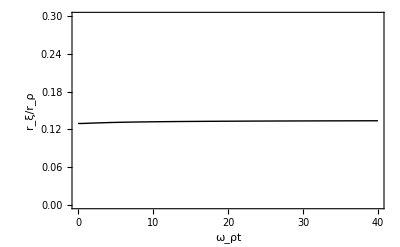

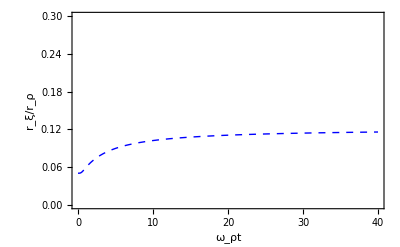

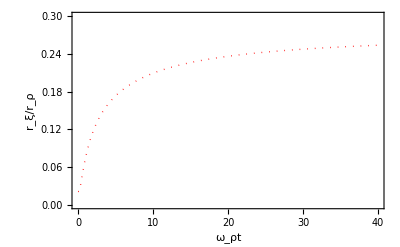

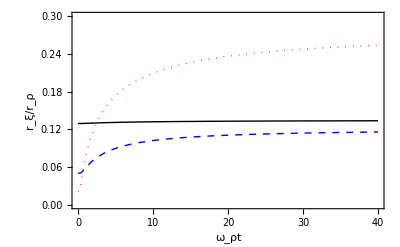

Dropbox/Trabalhos/rz-vortex oscilation/vel-r2.eps

```mathematica
L=2;
d1[α_]:=(-(2 π (2 √(1+α^2) (-4+7 α^2 (4+45 (α^2+α^4)))-210 α^4 (2+5 α^2+3 α^4) ArcCoth[√(1+α^2)]))/(105 √(1+α^2)))/(-(4 π (-√(1+α^2) (6+95 α^2+105 α^4)+15 α^2 (1+α^2) (4+7 α^2) ArcCoth[√(1+α^2)]))/(45 √(1+α^2)))
d2[α_]:=(-(4 π (-30-7 α^2 (107+240 α^2+135 α^4)+105 α^2 (1+α^2)^(3/2) (4+9 α^2) ArcCoth[√(1+α^2)]))/1575)/(-(4 π (-√(1+α^2) (6+95 α^2+105 α^4)+15 α^2 (1+α^2) (4+7 α^2) ArcCoth[√(1+α^2)]))/(45 √(1+α^2)))
d3[α_]:=(-(2 π (-2 √(1+α^2) (16-72 α^2+378 α^4+3675 α^6+3465 α^8)+630 α^6 (1+α^2) (8+11 α^2) ArcCoth[√(1+α^2)]))/(945 √(1+α^2)))/(-(4 π (-√(1+α^2) (6+95 α^2+105 α^4)+15 α^2 (1+α^2) (4+7 α^2) ArcCoth[√(1+α^2)]))/(45 √(1+α^2)))
d4[α_]:=(-(π (√(1+α^2) (-4+8 α^2+15 α^4)-3 α^4 (6+5 α^2) ArcCoth[√(1+α^2)]))/(18 (1+α^2)^(3/2)))/(-(4 π (-√(1+α^2) (6+95 α^2+105 α^4)+15 α^2 (1+α^2) (4+7 α^2) ArcCoth[√(1+α^2)]))/(45 √(1+α^2)))
d5[α_]:=(-(π (4 √(1+α^2) (11+15 α^2)-3 (2+7 α^2+5 α^4) Log[(2+α^2+2 √(1+α^2))/((-1+√(1+α^2))^2)]))/(9 √(1+α^2)))/(-(4 π (-√(1+α^2) (6+95 α^2+105 α^4)+15 α^2 (1+α^2) (4+7 α^2) ArcCoth[√(1+α^2)]))/(45 √(1+α^2)))
d6[α_]:=(-(4 π (√(1+α^2) (-96+352 α^2-1188 α^4+5544 α^6+49665 α^8+45045 α^10)-3465 α^8 (10+23 α^2+13 α^4) ArcTanh[1/(√(1+α^2))]))/(10395 √(1+α^2)))/(-(4 π (-√(1+α^2) (6+95 α^2+105 α^4)+15 α^2 (1+α^2) (4+7 α^2) ArcCoth[√(1+α^2)]))/(45 √(1+α^2)))
d7[α_]:=((2 π (√(1+α^2) (80+4648 α^2+17710 α^4+15015 α^6)-35 α^2 (64+432 α^2+792 α^4+429 α^6) ArcTanh[1/(√(1+α^2))]))/(525 √(1+α^2)))/((-(4 π (-√(1+α^2) (6+95 α^2+105 α^4)+15 α^2 (1+α^2) (4+7 α^2) ArcCoth[√(1+α^2)]))/(45 √(1+α^2)))^2)
F1[α_]:=(d3[α]D[d3[α],α]-2d6[α]D[d1[α],α])/(4(d3[α]^2-d1[α]d6[α]))
F2[α_]:=D[d2[α],α]/(2d2[α])
F3[α_]:=(2d3[α]D[d1[α],α]-d1[α]D[d3[α],α])/(4(d3[α]^2-d1[α]d6[α]))
G1[α_]:=d1[α] F1[α]+d3[α] F3[α]
G2[α_]:=d1[α](F1[α]^2+D[F1[α],α])+d3[α](4F1[α]F3[α]+D[F3[α],α])+3d6[α] F3[α]^2
G3[α_]:=2G1[α]
G4[α_]:=d4[α] L^2+L^2 d5[α]
G5[α_]:=d2[α]F2[α]
G6[α_]:=d2[α](F2[α]^2+D[F2[α],α])
G7[α_]:=2G5[α]
G8[α_]:=D[d1[α],α]F1[α]+1/2 D[d3[α],α]F3[α]
G9[α_]:=D[d2[α],α]F2[α]
G10[α_]:=D[d1[α],α](F1[α]^2+D[F1[α],α])+D[d3[α],α](1/2 D[F3[α],α]+2F1[α]F3[α])+D[d6[α],α] F3[α]^2
G11[α_]:=D[d2[α],α](F2[α]^2+D[F2[α],α])
G12[α_]:=2D[d1[α],α]F1[α]+D[d3[α],α]F3[α]
G13[α_]:=2G9[α]
G14[α_]:=D[d4[α],α] L^2+L^2 D[d5[α],α]

eqρ=d1[α0]ρ0==G4[α0]/ρ0^3+(4π γ d7[α0])/(ρ0^3 z0);
eqz=d2[α0] λ^2 z0==(2π γ d7[α0])/(ρ0^2 z0^2);
eqα=D[d1[α0],α0] ρ0^2+D[d2[α0],α0] λ^2 z0^2+G14[α0]/ρ0^2+(4π γ D[d7[α0],α0])/(ρ0^2 z0)==0;

eq1=d1[a](D[r[t],t,t]+ex r[t])+G1[a]r[t]D[α[t],t,t]+G2[a]r[t] D[α[t],t]^2+G3[a]D[r[t],t]D[α[t],t]-G4[a]/r[t]^3-(4π d7[a]γ)/(r[t]^3 z[t])==0/.a->α[t];
eq2=d2[a](D[z[t],t,t]+ex λ^2 z[t])+G5[a]z[t]D[α[t],t,t]+G6[a]z[t] D[α[t],t]^2+G7[a]D[z[t],t]D[α[t],t]-(2π d7[a]γ)/(r[t]^2 z[t]^2)==0/.a->α[t];
eq3=D[d1[a],a]r[t](D[r[t],t,t]+ex r[t])+D[d2[a],a]z[t](D[z[t],t,t]+ex λ^2 z[t])+(G8[a] r[t]^2+G9[a] z[t]^2)D[α[t],t,t]+(G10[a] r[t]^2+G11[a] z[t]^2)D[α[t],t]^2+G12[a] r[t]D[r[t],t]D[α[t],t]+G13[a]z[t]D[z[t],t]D[α[t],t]+G14[a]/r[t]^2+(4π D[d7[a],a]γ)/(r[t]^2 z[t])==0/.a->α[t];
γ=800;
L=2;
ex=0;

ClearAll[λ,ss,se]

λ=0.1;

ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}];

se=NDSolve[{eq1,eq2,eq3,r[0]==Evaluate[ρ0/.ss],z[0]==Evaluate[z0/.ss],α[0]==Evaluate[α0/.ss],D[r[t],t]==0/.t->0,D[z[t],t]==0/.t->0,D[α[t],t]==0/.t->0},{r[t],z[t],α[t]},{t,0,40}];

f4=Plot[Evaluate[α[t]/.se],{t,0,40},Frame->True,Axes->False,FrameLabel->{"ω_ρt","r_ξ/r_ρ"},PlotRange->{0,0.3},RotateLabel->False,LabelStyle->{Medium},PlotStyle->{Black}]


ClearAll[λ,ss,se]

λ=1;

ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}];

se=NDSolve[{eq1,eq2,eq3,r[0]==Evaluate[ρ0/.ss],z[0]==Evaluate[z0/.ss],α[0]==Evaluate[α0/.ss],D[r[t],t]==0/.t->0,D[z[t],t]==0/.t->0,D[α[t],t]==0/.t->0},{r[t],z[t],α[t]},{t,0,40}];

f5=Plot[Evaluate[α[t]/.se],{t,0,40},Frame->True,Axes->False,FrameLabel->{"ω_ρt","r_ξ/r_ρ"},LabelStyle->{Medium},PlotRange->{0,0.3},RotateLabel->False,PlotStyle->{Directive[Blue,Dashed]}]


ClearAll[λ,ss,se]

λ=8;

ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}];

se=NDSolve[{eq1,eq2,eq3,r[0]==Evaluate[ρ0/.ss],z[0]==Evaluate[z0/.ss],α[0]==Evaluate[α0/.ss],D[r[t],t]==0/.t->0,D[z[t],t]==0/.t->0,D[α[t],t]==0/.t->0},{r[t],z[t],α[t]},{t,0,40}];


f6=Plot[Evaluate[α[t]/.se],{t,0,40},Frame->True,Axes->False,FrameLabel->{"ω_ρt","r_ξ/r_ρ"},LabelStyle->{Medium},PlotRange->{0,0.3},RotateLabel->False,PlotStyle->{Directive[Red,Dotted]}]

g2=Show[f4,f5,f6]

Export["Dropbox/Trabalhos/rz-vortex oscilation/vel-r2.eps",g2]

ClearAll[d1,d2,d3,d4,d5,d6,d7,F1,F2,F3,G1,G2,G3,G4,G5,G6,G7,G8,G9,G10,G11,G12,G13,G14,eq1,eq2,eq3,eqρ,eqz,eqα,λ,γ,se,ss,L,ex,vp,f1,f2,f3,g1,d7,g2,f4,f5,f6]
```

### Comparação com a simulação númerica.

{ρ0→6.4219,z0→7.10582,α0→0.03983}

{{r[t]→InterpolatingFunction[{{0.,40.}},<>][t],z[t]→InterpolatingFunction[{{0.,40.}},<>][t],α[t]→InterpolatingFunction[{{0.,40.}},<>][t]}}

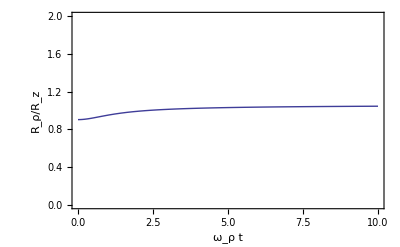

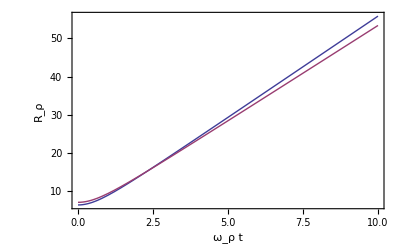

{ρ0→6.55743,z0→6.53227,α0→0.0381328}

{{r[t]→InterpolatingFunction[{{0.,40.}},<>][t],z[t]→InterpolatingFunction[{{0.,40.}},<>][t],α[t]→InterpolatingFunction[{{0.,40.}},<>][t]}}

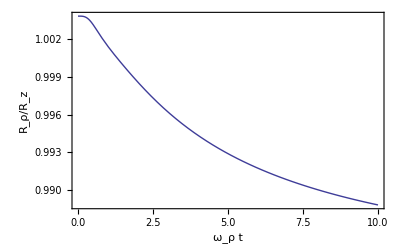

-Graphics-

Dropbox/Trabalhos/rz-vortex oscilation/nume01.eps

Dropbox/Trabalhos/rz-vortex oscilation/nume1.eps

```mathematica
L=1;
d1[α_]:=(-8/315 π (-6+21 α^2+140 α^4+105 α^6-105 α^4 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))/(8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))
d2[α_]:=((8 π (15+7 α^2 (23+35 α^2+15 α^4)-105 α^2 (1+α^2)^(5/2) ArcCoth[√(1+α^2)]))/1575)/(8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))
d3[α_]:=(8/945 π (8-18 α^2+63 α^4+420 α^6+315 α^8-315 α^6 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))/(8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))
d4[α_]:=(-1/2 π (-4/3+2 α^2-(2 α^4 ArcCoth[√(1+α^2)])/(√(1+α^2))))/(8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))
d5[α_]:=(-8/9 π (4+3 α^2-3 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))/(8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))
d6[α_]:=((8 π (48-11 α^2 (8-18 α^2+63 α^4+420 α^6+315 α^8)+3465 α^8 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))/10395)/(8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))
d7[α_]:=((16 π (√(1+α^2) (30+749 α^2+1680 α^4+945 α^6)-105 (4+9 α^2) (α+α^3)^2 ArcTanh[1/(√(1+α^2))]))/(1575 √(1+α^2)))/((8/45 π (3+20 α^2+15 α^4-15 α^2 (1+α^2)^(3/2) ArcCoth[√(1+α^2)]))^2)
F1[α_]:=(d3[α]D[d3[α],α]-2d6[α]D[d1[α],α])/(4(d3[α]^2-d1[α]d6[α]))
F2[α_]:=D[d2[α],α]/(2d2[α])
F3[α_]:=(2d3[α]D[d1[α],α]-d1[α]D[d3[α],α])/(4(d3[α]^2-d1[α]d6[α]))
G1[α_]:=d1[α] F1[α]+d3[α] F3[α]
G2[α_]:=d1[α](F1[α]^2+D[F1[α],α])+d3[α](4F1[α]F3[α]+D[F3[α],α])+3d6[α] F3[α]^2
G3[α_]:=2G1[α]
G4[α_]:=d4[α] L^2+L^2 d5[α]
G5[α_]:=d2[α]F2[α]
G6[α_]:=d2[α](F2[α]^2+D[F2[α],α])
G7[α_]:=2G5[α]
G8[α_]:=D[d1[α],α]F1[α]+1/2 D[d3[α],α]F3[α]
G9[α_]:=D[d2[α],α]F2[α]
G10[α_]:=D[d1[α],α](F1[α]^2+D[F1[α],α])+D[d3[α],α](1/2 D[F3[α],α]+2F1[α]F3[α])+D[d6[α],α] F3[α]^2
G11[α_]:=D[d2[α],α](F2[α]^2+D[F2[α],α])
G12[α_]:=2D[d1[α],α]F1[α]+D[d3[α],α]F3[α]
G13[α_]:=2G9[α]
G14[α_]:=D[d4[α],α] L^2+L^2 D[d5[α],α]

eqρ=d1[α0]ρ0==G4[α0]/ρ0^3+(4π γ d7[α0])/(ρ0^3 z0);
eqz=d2[α0] λ^2 z0==(2π γ d7[α0])/(ρ0^2 z0^2);
eqα=D[d1[α0],α0] ρ0^2+D[d2[α0],α0] λ^2 z0^2+G14[α0]/ρ0^2+(4π γ D[d7[α0],α0])/(ρ0^2 z0)==0;

eq1=d1[a](D[r[t],t,t]+ex r[t])+G1[a]r[t]D[α[t],t,t]+G2[a]r[t] D[α[t],t]^2+G3[a]D[r[t],t]D[α[t],t]-G4[a]/r[t]^3-(4π d7[a]γ)/(r[t]^3 z[t])==0/.a->α[t];
eq2=d2[a](D[z[t],t,t]+ex λ^2 z[t])+G5[a]z[t]D[α[t],t,t]+G6[a]z[t] D[α[t],t]^2+G7[a]D[z[t],t]D[α[t],t]-(2π d7[a]γ)/(r[t]^2 z[t]^2)==0/.a->α[t];
eq3=D[d1[a],a]r[t](D[r[t],t,t]+ex r[t])+D[d2[a],a]z[t](D[z[t],t,t]+ex λ^2 z[t])+(G8[a] r[t]^2+G9[a] z[t]^2)D[α[t],t,t]+(G10[a] r[t]^2+G11[a] z[t]^2)D[α[t],t]^2+G12[a] r[t]D[r[t],t]D[α[t],t]+G13[a]z[t]D[z[t],t]D[α[t],t]+G14[a]/r[t]^2+(4π D[d7[a],a]γ)/(r[t]^2 z[t])==0/.a->α[t];

(*n11=ListPlot[{Table[{(i-1)*0.5,Import["Dropbox/Trabalhos/rz-vortex oscilation/R-l1-lam00.dat","Table"][[i,2]]/Import["Dropbox/Trabalhos/rz-vortex oscilation/Z-l1-lam00.dat","Table"][[i,2]]},{i,1,21,1}]},PlotStyle->{Black},PlotRange->{0,1.2},Frame->True,Axes->False,FrameLabel->{"ω_ρ t","R_ρ/R_z"},RotateLabel->False]


n101=ListPlot[{Table[{(i-1)*0.5,Import["Dropbox/Trabalhos/rz-vortex oscilation/R-l1-lam01.dat","Table"][[i,2]]/Import["Dropbox/Trabalhos/rz-vortex oscilation/Z-l1-lam01.dat","Table"][[i,2]]},{i,1,21,1}]},PlotStyle->{Black},Frame->True,Axes->False,FrameLabel->{"ω_ρ t","R_ρ/R_z"},PlotRange->{0.0,1.2},RotateLabel->False]
n21=ListPlot[{Table[{(i-1)*0.5,Import["Dropbox/Trabalhos/rz-vortex oscilation/R-l2-lam00.dat","Table"][[i,2]]/Import["Dropbox/Trabalhos/rz-vortex oscilation/Z-l2-lam00.dat","Table"][[i,2]]},{i,1,21,1}]},PlotStyle->{Black},PlotRange->{0,1.2},Frame->True,Axes->False,FrameLabel->{"ω_ρ t",Subscript[r, ρ]/Subscript[r, z]},RotateLabel->False]
n201=ListPlot[{Table[{(i-1)*0.5,Import["Dropbox/Trabalhos/rz-vortex oscilation/R-l2-lam01.dat","Table"][[i,2]]/Import["Dropbox/Trabalhos/rz-vortex oscilation/Z-l2-lam01.dat","Table"][[i,2]]},{i,1,21,1}]},PlotStyle->{Black},Frame->True,Axes->False,FrameLabel->{"ω_ρ t",Subscript[r, ρ]/Subscript[r, z]},PlotRange->{0.0,1.2},RotateLabel->False]*)

λ=0.9;
γ=800;
ex=0;

ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}]

se=NDSolve[{eq1,eq2,eq3,r[0]==Evaluate[ρ0/.ss],z[0]==Evaluate[z0/.ss],α[0]==Evaluate[α0/.ss],D[r[t],t]==0/.t->0,D[z[t],t]==0/.t->0,D[α[t],t]==0/.t->0},{r[t],z[t],α[t]},{t,0,40}]


fe101=Plot[Evaluate[r[t]/.se]/Evaluate[z[t]/.se],{t,0,10},Frame->True,Axes->False,FrameLabel->{"ω_ρ t","R_ρ/R_z"},PlotRange->{0,2},RotateLabel->False]

Plot[{Evaluate[r[t]/.se],Evaluate[z[t]/.se]},{t,0,10},Frame->True,Axes->False,FrameLabel->{"ω_ρ t","R_ρ"},PlotRange->All,RotateLabel->False]

ClearAll[ss,se,λ,L]
λ=1;
L=1;
ss=FindRoot[{eqρ,eqz,eqα},{ρ0,1},{z0,1},{α0,0.001}]

se=NDSolve[{eq1,eq2,eq3,r[0]==Evaluate[ρ0/.ss],z[0]==Evaluate[z0/.ss],α[0]==Evaluate[α0/.ss],D[r[t],t]==0/.t->0,D[z[t],t]==0/.t->0,D[α[t],t]==0/.t->0},{r[t],z[t],α[t]},{t,0,40}]

fe11=Plot[Evaluate[r[t]/.se]/Evaluate[z[t]/.se],{t,0,10},Frame->True,RotateLabel->False,Axes->False,FrameLabel->{"ω_ρ t","R_ρ/R_z"},PlotRange->All]

Plot[{Evaluate[r[t]/.se],Evaluate[z[t]/.se]},{t,0,10},Frame->True,RotateLabel->False,Axes->False,FrameLabel->{"ω_ρ t","R"},PlotRange->{0,1.2}]

ClearAll[ss,se,L,λ,d1,d2,d3,d4,d5,d6,F1,F2,F3,G1,G2,G3,G4,G5,G6,G7,G8,G9,G10,G11,G12,G13,G14,eq1,eq2,eq3,eqρ,eqz,eqα]


Export["Dropbox/Trabalhos/rz-vortex oscilation/nume01.eps",g1]
Export["Dropbox/Trabalhos/rz-vortex oscilation/nume1.eps",g2]

ClearAll[d1,d2,d3,d4,d5,d6,d7,F1,F2,F3,G1,G2,G3,G4,G5,G6,G7,G8,G9,G10,G11,G12,G13,G14,eq1,eq2,eq3,eqρ,eqz,eqα,λ,γ,se,ss,L,ex,fe101,fe11,fe21,fe201,n11,n101,g1,g2,g3,fα01,fα1,fα10,n21,n201]
```

## Hidrodinâmica

Outra aproximação para encontrar os modos coletivos de um condensado é reescrevendo a EGP no referencial de rotação em termos da densidade e da fase, e assim usar a aproximação de TF para obter as equações hidrodinâmicas para  estas quantidades. Desta maneira, as equações linearizadas à pequenas flutuações em torno do equilibrio são:
∂/(∂t)δn+(ℓ/ρ^2-Ω)∂/(∂ϕ)δn+∇·(n_0∇δS)=0
∂/(∂t)δS+(ℓ/ρ^2-Ω)∂/(∂ϕ)δS+g δn=0
----------------------------------------------------
∂/(∂t)δn+(ℓ/ρ^2-Ω)∂/(∂ϕ)δn+∇n_0∇δS+n_0∇^2 δS=0
∂/(∂t)δS+(ℓ/ρ^2-Ω)∂/(∂ϕ)δS+g δn=0
Fazendo δn∝ⅇ^(ⅈ (m ϕ -ω t)), δS∝ⅇ^(ⅈ (m ϕ -ω t))
-ⅈ [ω - m(ℓ/ρ^2-Ω)]δn+m^2/ρ^2 n_0 δS+∇n_0∇δS+n_0∇_(ρ,z)^2 δS=0
-ⅈ ω δS+ⅈ m(ℓ/ρ^2-Ω)δS+g δn=0
Podemos reduzir estas duas equações a apenas uma, já que g δn=ⅈ (ω+m Ω+m ℓ/ρ^2)δS.
[ω -m (ℓ/ρ^2-Ω)]^2 δS+m^2/ρ^2 g n_0 δS+g∇n_0∇δS+g n_0∇_(ρ,z)^2 δS=0
--------------------------------------------------------
[(ω +m Ω+(m ℓ)/ρ^2)^2+m^2/ρ^2 g n_0]δS+g∇n_0∇δS+g n_0∇_(ρ,z)^2 δS=0